## INTRO

💡 This is a program for χ^2 fitting, using SN1a data.
💡 SN data are taken from http://supernova.lbl.gov/Union/
💡 
💡
💡

## PRE

### Settings

Include the packages needed.

```mathematica
Needs["ErrorBarPlots`"]
<<PhysicalConstants`
```

```mathematica
Needs["PlotLegends`"]
```

Set work directory. Modify it to your own directory before runing this program. DATA folder are placed in this directory. DATA folder should contain the SN data files.

```mathematica
SetDirectory["E:\\Nutshare\\Store\\Projects\\DataFitting"];
```

### Conventions, parameters, etc

Line element: ds^2=-dt^2+a[t]^2(dr^2/(1-k r^2)+r^2(dθ^2+Sin[θ]^2 dϕ^2))

Ωm0: matter fraction
Ωd0: dark energy/cosmological constant fraction
Ωr0: radiation fraction

Ωm0w: matter fraction given by WMAP
Ωd0w: dark energy/cosmological constant fraction given by WMAP
Ωr0w: radiation fraction given WMAP

```mathematica
Ωm0w=0.27;
Ωd0w=0.73;
Ωr0w =8.09*10^-5;
```

### Basic Equations in LCDM

H0: Hubble constant in unit of km/s/Mpc
c: speed of light

```mathematica
H0w=71;
c=SpeedOfLight*Second/(1000Meter)
gra=GravitationalConstant
```

149896229/500

(6.67428×10^-11 Meter^2 Newton)/Kilogram^2

## LCDM Model

### Basic Definations

hubble[Ωm0_,Ωd0_,Ωk0_,z_]: Hubble functions in LCDM.
H[z]: an example of hubble function with given parameters.

```mathematica
hubble[Ωm0_,Ωd0_,Ωk0_,z_]:=H0w √(Ωm0(1+z)^3+Ωd0+Ωk0(1+z)^2);
H[z_]=hubble[Ωm0w,Ωd0w,0,z];
```

q[Ωm0_,Ωd0_,Ωk0_,z_]:Deceleration parameter. DEF: q[Ωm0_,Ωd0_,Ωk0_,z_]=-1/H[z]D[D[a[t],t],t]/D[a[t],t]

```mathematica
q[Ωm0_,Ωd0_,Ωk0_,z_]=-1+(1+z)/hubble[Ωm0,Ωd0,Ωk0,z] D[hubble[Ωm0,Ωd0,Ωk0,z],z];
```

```mathematica
q[Ωm0,Ωd0,Ωk0,0]
```

-1+(2 Ωk0+3 Ωm0)/(2 (Ωd0+Ωk0+Ωm0))

```mathematica
-1+(2 Ωk0+3 Ωm0)/(2 (Ωd0+Ωk0+Ωm0))
```

-1+(2 Ωk0+3 Ωm0)/(2 (Ωd0+Ωk0+Ωm0))

```mathematica
Limit[q[Ωm0,Ωd0,Ωk0,z],z->Infinity]
```

1/2

(General) Friedmann equations are

(3(a[t]'+k))/a[t]^2=8 π G ρ
2(a[t]'')/a[t]+(a[t]'+k)/a[t]^2=-8π G p

Since “zt” will be used as a parameter in most cases, we define “ztr” as a name for transition redshift, “ztrr” for transition redshift with a parameter r.
ztr[Ωm0_,Ωd0_,z_]: Transition redshift in LCDM with Ωk0 not zero with full parameters
ztrr[r_,z_]: with r=Ωm0/Ωd0

```mathematica
ztr[Ωm0_,Ωd0_]=(2 Ωd0/Ωm0)^(1/3)-1;
ztrr[r_]=(2/r)^(1/3)-1;
```

Regard “zt” as a paramter, solve out Ωd0 and Ωk0=1-Ωm0-Ωd0

Ωd0=1/2 Ωm0(1+zt)^3
Ωk0=1-Ωm0-1/2 Ωm0(1+zt)^3

### Transition redshift, deceleration parameter, theoretically.

#### Deceleration parameter

Deceleration parameter can be ploted with respect to redshift z.
Using flat FRW model. That is Ωk0=0.

```mathematica
pldec[Ωm0v_,color_]:=Plot[q[Ωm0v,1-Ωm0v,0,z],{z,-1,10},PlotRange->{{-1.05,10},{-1.05,0.55}},PlotStyle->color,AxesOrigin->{-1,0},AxesLabel->{z,q}]
```

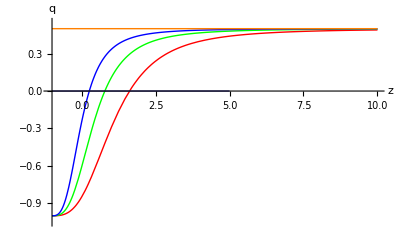

```mathematica
Show[{pldec[0.1,Red],pldec[0.26,Green],pldec[0.5,Blue],pldec[1,Orange],Plot[0,{z,-1,5},PlotStyle->Thick]}]
```

```mathematica
Manipulate[pldec[Ωm0v,{Orange,Thick}],{{Ωm0v,0.26,"Matter Fraction"},0,1,Appearance->"Open"},SaveDefinitions->True]
```

Plot deceleration parameter with respect to r. This is not related to Ωk0, i.e., the curvature of the spacetime won’t affect this result.

```mathematica
plztr[color_]:=Plot[ztr[Ωm0,1-Ωm0],{Ωm0,0,1},PlotRange->{{0,1},{-1,4}},PlotStyle->color,AxesOrigin->{0,-1}]
```

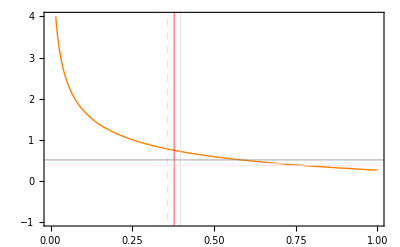

```mathematica
pldecrr=Plot[ztrr[r],{r,0,1},PlotRange->{{0,1},{-1,4}},PlotStyle->{Thick,Orange},AxesOrigin->{0,-1},Frame->True,GridLines->{{{0.358,Dashed},{0.378,Directive[Red]},0.398},{{0.376,LightRed},{0.426,LightBlue},{0.508,Gray}}}]
```

In a flat universe, Ωk0=0. Then Ωd0=1-Ωm0.

```mathematica
pldecr=Show[Plot[ztr[Ωm0,1-Ωm0],{Ωm0,0,1},PlotRange->{{0,1},{-1,4}},PlotStyle->{Thick,Orange},AxesOrigin->{0,-1},Frame->True,GridLines->{{{0.044,Dashed},{0.261,Red},{0.274,Green},{0.287,Gray}},{{0.376,LightRed},{0.426,LightBlue},{0.508,Gray}}}],Graphics[{Gray,Rectangle[Scaled[{0.261,.2752}],Scaled[{0.287,.3016}]]},Frame->True]]
```

-Graphics-

## Interacting Models

### Take the form Q_c=ξ H ρ_c.

Hubble function without curvature

```mathematica
hubbleICC[H0_,Ωd0_,Ωm0_,w_,ξ_,z_]:=H0 √(Ωm+Ωd);
```

### δ is constant + EoS w is constant

#### Definations

Fraction energy density

```mathematica
ΩmICC[Ωm0_,ξ_,z_]:=Ωm0 (1+z)^(3-ξ)
```

```mathematica
ΩdICC[Ωm0_,Ωd0_,w_,ξ_,z_]:=Ωd0 (1+z)^(3(1+w))-ξ/(ξ+3w) Ωm0 (1+z)^(3(1+w))((1+z)^(-ξ-3w)-1)
```

```mathematica
(* 
(* These are manipulates that we can used to check the behavior of Energy fraction of different species.*)
Manipulate[Plot[ΩmICC[Ωm0,ξ,z],{z,-0.5,10}],{Ωm0,0.01,0.99},{ξ,-0.1,0.1}]
Manipulate[Plot[ΩdICC[Ωm0,1-Ωm0,w,ξ,z],{z,-0.5,10}],{Ωm0,0.01,0.99},{w,-1.2,-0.8},{ξ,-0.1,0.1}]
*)
```

Hubble function

```mathematica
hubbleICC[H0ICC_,Ωm0ICC_,Ωd0ICC_,wICC_,ξICC_,z_]=H0ICC √(ΩmICC[Ωm0ICC,ξICC,z]+ΩdICC[Ωm0ICC,Ωd0ICC,wICC,ξICC,z])
```

H0ICC √((1+z)^(3 (1+wICC)) Ωd0ICC+(1+z)^(3-ξICC) Ωm0ICC-((1+z)^(3 (1+wICC)) (-1+(1+z)^(-3 wICC-ξICC)) ξICC Ωm0ICC)/(3 wICC+ξICC))

Deceleration parameter

```mathematica
qICC[H0ICC_,Ωm0ICC_,Ωd0ICC_,wICC_,ξICC_,z_]=-1+(1+z)/hubbleICC[H0ICC,Ωm0ICC,Ωd0ICC,wICC,ξICC,z] D[hubbleICC[H0ICC,Ωm0ICC,Ωd0ICC,wICC,ξICC,z],z];
```

```mathematica
qICC[H0ICC,Ωm0ICC,Ωd0ICC,wICC,ξICC,z]//FullSimplify
```

(-3 wICC (-1+ξICC) Ωm0ICC+(1+3 wICC) (1+z)^(3 wICC+ξICC) (3 wICC Ωd0ICC+ξICC (Ωd0ICC+Ωm0ICC)))/(6 wICC Ωm0ICC+2 (1+z)^(3 wICC+ξICC) (3 wICC Ωd0ICC+ξICC (Ωd0ICC+Ωm0ICC)))

```mathematica
Limit[qICC[H0ICC,Ωm0ICC,Ωd0ICC,wICC,ξICC,z]//FullSimplify,z->Infinity,Assumptions->(3 wICC+ξICC)<0]
```

(1-ξICC)/2

At z-> Infinity limit, qIIC->(1-ξ)/2, with 3 wICC+ξICC<0. This is different from LCDM model.

#### Plots, showcase, manipulate toys

```mathematica
pldecICC[Ωm0ICC_,wICC_,ξICC_,color_]:=Plot[qICC[H0w,Ωm0ICC,1-Ωm0ICC,wICC,ξICC,z],{z,-1,10},PlotRange->{{-1.05,10},{-1.05,1}},PlotStyle->color,AxesOrigin->{-1,0},AxesLabel->{z,q}];
```

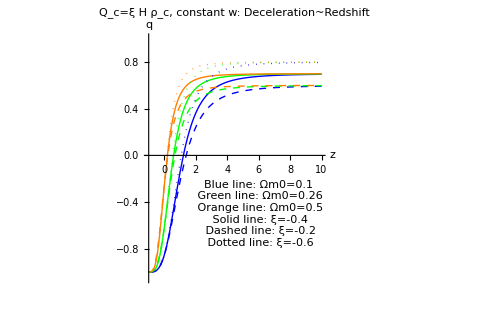

```mathematica
pldecICCShowSum=Show[{pldecICC[0.1,-1,-0.4,Blue],pldecICC[0.26,-1,-0.4,Green],pldecICC[0.5,-1,-0.4,Orange],pldecICC[0.1,-1,-0.2,Directive[Blue,Dashed]],pldecICC[0.26,-1,-0.2,Directive[Green,Dashed]],pldecICC[0.5,-1,-0.2,Directive[Orange,Dashed]],pldecICC[0.1,-1,-0.6,Directive[Blue,Dotted]],pldecICC[0.26,-1,-0.6,Directive[Green,Dotted]],pldecICC[0.5,-1,-0.6,Directive[Orange,Dotted]]},Epilog->Inset[Framed[Style["Blue line: Ωm0=0.1\n Green line: Ωm0=0.26\n Orange line: Ωm0=0.5\n Solid line: ξ=-0.4\n Dashed line: ξ=-0.2\n Dotted line: ξ=-0.6",10],Background->LightYellow],{6,-0.5}],PlotLabel->"Q_c=ξ H ρ_c, constant w: Deceleration~Redshift",ImageSize->500]
```

z->Infinity is a degenerate limit. For constant ξ and constant w models, this limit is determined by the interaction strength ξ . This might be useful if more complicated models are investigated and no large deviations are shown. [Nota]

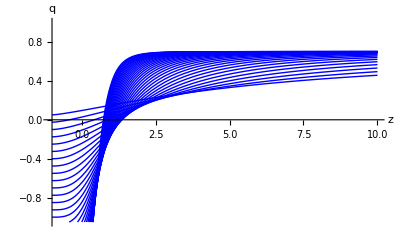
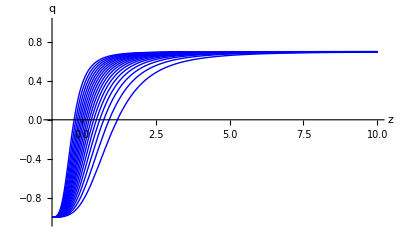
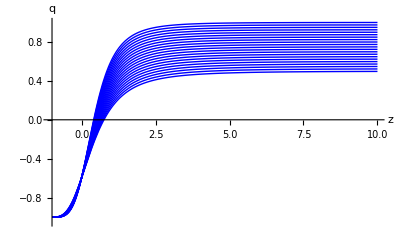
Q_c=ξ H ρ_c with constant ξ and w |  | 
Varying EoS | Varying Ωm0 | Varying ξ
-Graphics- | -Graphics- | -Graphics-

```mathematica
varyingICCShowSum=Grid[{{"Q_c=ξ H ρ_c with constant ξ and w",SpanFromLeft},{"Varying EoS","Varying Ωm0","Varying ξ"},{Show[Table[pldecICC[0.1,wICC,-0.4,Blue],{wICC,-2,-0.3,0.05}]],Show[Table[pldecICC[Ωm0ICC,-1,-0.4,Blue],{Ωm0ICC,0.1,0.9,0.05}]],Show[Table[pldecICC[0.27,-1,ξICC,Blue],{ξICC,-1,0,0.05}]]}},Frame->All,Background->{{None},{LightGreen,LightGray,None}},Alignment->Center,ItemSize->13]
```

Interaction ξ changes the limit, i.e., what value will it be at z->Infinity. EoS changes the the whole shape. Matter fraction also changes how fast q varies, but just in a small time scale.

Use movable slides to check how do the parameters affect the deceleration parameter. Just a toy.

```mathematica
pldecICCManSum=Manipulate[Show[{pldecICC[Ωm0ICC,wICC,ξICC,Orange],pldec[Ωm0ICC,{Pink,Thick}]},PlotLabel->"Q_c=ξ H ρ_c, constant w: Deceleration Parameter ~ Redshift"],{{Ωm0ICC,0.26,"Matter Fraction"},0,1,Appearance->"Open"},{{ξICC,-0.4,"Interaction"},-1,0,Appearance->"Open"},{{wICC,-1,"Equation of State"},-1.5,-0.5,Appearance->"Open"},Delimiter,Style["Pink is the deceleration parameter for LCDM.",Medium],Style["Orange is for interacting model with Q=ξ H ρ_m",Medium],ControlPlacement->{Right,Right,Right},SaveDefinitions->True]
```

#### Transition redshift definations and equations.

Find out the expression for transition redshift

```mathematica
(3wICC+1)ΩdICC[Ωm0ICC,Ωd0ICC,wICC,ξICC,z]+ΩmICC[Ωm0ICC,ξICC,z]==0//Simplify
```

(1+z)^(3-ξICC) Ωm0ICC+(1+3 wICC) (1+z)^(3+3 wICC) (Ωd0ICC+((1-(1+z)^(-3 wICC-ξICC)) ξICC Ωm0ICC)/(3 wICC+ξICC))==0

```mathematica
ztrICC[Ωm0ICC_,Ωd0ICC_,wICC_,ξICC_]=-1+((-ξICC/(ξICC+3wICC)(1+3wICC)+1)/((1+3wICC)(-ξICC/(ξICC+3wICC)Ωm0ICC-Ωd0ICC))Ωm0ICC)^(1/(ξICC+3wICC))
```

-1+(((1-((1+3 wICC) ξICC)/(3 wICC+ξICC)) Ωm0ICC)/((1+3 wICC) (-Ωd0ICC-(ξICC Ωm0ICC)/(3 wICC+ξICC))))^(1/(3 wICC+ξICC))

The first solution is trivil. So the second one is taken.

Define rICC=Ωm0ICC/Ωd0ICC

```mathematica
ztrrICC[rICC_,wICC_,ξICC_]=-1+((-ξICC/(ξICC+3wICC)(1+3wICC)+1)/((1+3wICC)(-ξICC/(ξICC+3wICC)rICC-1))rICC)^(1/(3 wICC+ξICC));
```

#### Visualiztion of transition redshift

Check the behavior of this transition redshift.

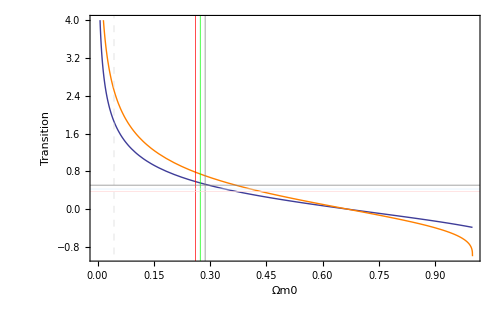

```mathematica
pldecrICC=Plot[{ztrICC[Ωm0ICC,1-Ωm0ICC,-1,-0.4],ztr[Ωm0ICC,1-Ωm0ICC]},{Ωm0ICC,0,1},FrameLabel->{"Ωm0","Transition"},PlotRange->{{0,1},{-1,4}},PlotStyle->{Thick,Orange},AxesOrigin->{0,-1},Frame->True,PlotRangeClipping->False,GridLines->{{{0.044,Dashed},{0.261,Red},{0.274,Green},{0.287,Gray}},{{0.376,LightRed},{0.426,LightBlue},{0.508,Gray}}},PlotLegend->{"Q=-0.4 H ρ_c","LCDM"},LegendPosition->{0.0,-0.05},LegendShadow->None,ImageSize->500]
```

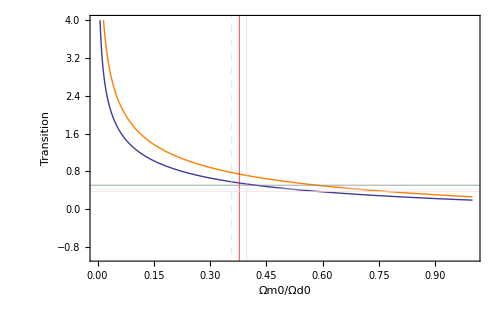

```mathematica
pldecrrICC=Plot[{ztrrICC[rICC,-1,-0.4],ztrr[rICC]},{rICC,0,1},PlotRange->{{0,1},{-1,4}},PlotStyle->{Thick,Orange},AxesOrigin->{0,-1},Frame->True,FrameLabel->{"Ωm0/Ωd0","Transition"},GridLines->{{{0.358,Dashed},{0.378,Directive[Red]},0.398},{{0.376,LightRed},{0.426,LightBlue},{0.508,Gray}}},PlotLegend->{"Q=-0.4 H ρ_c","LCDM"},LegendPosition->{0.0,-0.05},LegendShadow->None,ImageSize->500]
```

```mathematica
plztrICC[wICC_,ξICC_,color_]:=Plot[ztrICC[Ωm0ICC,1-Ωm0ICC,wICC,ξICC],{Ωm0ICC,0,1},PlotRange->{{0,1},{-1,4}},PlotStyle->color,AxesOrigin->{0,-1},Frame->True];
```

```mathematica
Show[plztrICC[-1,-0.02,Orange],Graphics[{Gray,Rectangle[Scaled[{0.261,.2752}],Scaled[{0.287,.3016}]]},Frame->True],FrameLabel->{"Ωm0","Transition"},GridLines->{{},{{0,Dashed}}}]
```

-Graphics-

The following figure:

Orange for w=-1
Blue for w=-0.9

line: ξ=0.2
Dashed: ξ=0.1
Dotted: ξ=-0.1
DotDashed: ξ=-0.2

Pink line:w=-1, ξ=0

```mathematica
plztrvsΩm0ICCSum=Grid[{{Show[{plztrICC[-1,0.2,Orange],plztrICC[-1,0.1,{Orange,Dashed}],plztrICC[-1,-0.1,{Orange,Dotted}],plztrICC[-1,-0.2,{Orange,DotDashed}],Plot[ztr[Ωm0ICC,1-Ωm0ICC],{Ωm0ICC,0,1},PlotRange->{{0,1},{-1,4}},PlotStyle->Pink,AxesOrigin->{0,-1}]},Graphics[{Gray,Rectangle[Scaled[{0.261,.2752}],Scaled[{0.287,.3016}]]},Frame->True],FrameLabel->{"Ωm0","Transition"},GridLines->{{},{{0,Dashed}}},Epilog->Inset[Framed[Style["Solid: ξ=0.2; Dashed: ξ=0.1\n Dotted: ξ=-0.1; DotDashed: ξ=-0.2\n Pink line:w=-1, ξ=0",10],Background->LightGreen,FrameStyle->None],{0.3,3.5},{Left,Top}],PlotLabel->"Q_c=ξ H ρ_c, for w=-1: Transition~Redshift",ImageSize->400],
Show[{plztrICC[-0.7,0.2,Blue],plztrICC[-0.7,0.1,{Blue,Dashed}],plztrICC[-0.7,-0.1,{Blue,Dotted}],plztrICC[-0.7,-0.2,{Blue,DotDashed}],Plot[ztr[Ωm0ICC,1-Ωm0ICC],{Ωm0ICC,0,1},PlotRange->{{0,1},{-1,4}},PlotStyle->Pink,AxesOrigin->{0,-1}]},Graphics[{Gray,Rectangle[Scaled[{0.261,.2752}],Scaled[{0.287,.3016}]]},Frame->True],FrameLabel->{"Ωm0","Transition"},GridLines->{{},{{0,Dashed}}},Epilog->Inset[Framed[Style["Solid: ξ=0.2; Dashed: ξ=0.1\n Dotted: ξ=-0.1; DotDashed: ξ=-0.2\n Pink line:w=-1, ξ=0",10],Background->LightGreen,FrameStyle->None],{0.3,3.5},{Left,Top}],PlotLabel->"Q_c=ξ H ρ_c, for w=-0.9: Transition~Redshift",ImageSize->400]
}}]
```

-Graphics-

```mathematica
plztrICCManSum=Manipulate[Show[{plztrICC[wICC,ξICC,{Orange,DotDashed}],Plot[ztr[Ωm0ICC,1-Ωm0ICC],{Ωm0ICC,0,1},PlotRange->{{0,1},{-1,4}},PlotStyle->Pink,AxesOrigin->{0,-1}]},Graphics[{Gray,Rectangle[Scaled[{0.261,.2752}],Scaled[{0.287,.3016}]]},Frame->True],FrameLabel->{"Ωm0","Transition"},GridLines->{{},{{0,Dashed}}},PlotLabel->"Q_c=ξ H ρ_c, constant w: Transition ~ Ωm0"],{{ξICC,-0.4,"Interaction"},-1,1,Appearance->"Open"},{{wICC,-1.02,"Equation of state"},-2,-0.3,Appearance->"Open"},Delimiter,Style["Pink is the transition redshift vs Ωm0 for LCDM.",Medium],Style["Orange DotDashed line is interacting model,",Medium],Style["for Q=ξ H ρ_m with constant w, \n where ξ and w are both constants",Medium],ControlPlacement->{Right,Right},SaveDefinitions->True]
```

#### Find out the allowed region of coupling constant.

To find out the region of ξ, set w=-1 and Ωd0=1-Ωm0. Let the ztr-Ωm0 line cross points (0.287,0.508) and (0.261, 0.376).

```mathematica
ztrICC[0.287,1-0.287,-1,ξICC1]==0.508
```

-1+0.1435^(1/(-3+ξICC1)) (-(1+(2 ξICC1)/(-3+ξICC1))/(-0.713-(0.287 ξICC1)/(-3+ξICC1)))^(1/(-3+ξICC1))==0.508

```mathematica
ξICCffunc[Ωm0ICC_,Ωd0ICC_,wICC_,data_]:=ξICC/.FindRoot[ztrICC[Ωm0ICC,Ωd0ICC,wICC,ξICC]==data,{ξICC,-0.6}]
```

```mathematica
ξICCf2[Ωm0ICC_,Ωd0ICC_,wICC_]:=ξICC/.FindRoot[ztrICC[Ωm0ICC,Ωd0ICC,wICC,ξICC]==0.508,{ξICC,-0.6}]
```

```mathematica
ξICCf1[Ωm0ICC_,Ωd0ICC_,wICC_]:=ξICC/.FindRoot[ztrICC[Ωm0ICC,Ωd0ICC,wICC,ξICC]==0.376,{ξICC,-0.6}]
```

Cross the Center of best fit. (0.274,0.426)

```mathematica
ξICCfc[Ωm0ICC_,Ωd0ICC_,wICC_]:=ξICC/.FindRoot[ztrICC[Ωm0ICC,Ωd0ICC,wICC,ξICC]==0.426,{ξICC,-0.6}]
```

According to the data of transition redshift.

```mathematica
ξICCf2[wICC_]:=ξICCffunc[0.287,1-0.287,wICC,0.508]
```

```mathematica
ξICCf1[wICC_]:=ξICCffunc[0.261,1-0.261,wICC,0.376]
```

```mathematica
ξICCfc[wICC_]:=ξICCffunc[0.274,1-0.274,wICC,0.426]
```

```mathematica
numPlot[ss1_,{s_,c_,e_},ee_,{start_,end_}]:=Graphics[{Orange,Thickness[.01],Text[Style[ss1,Large,Orange],{s,0}],Text[Style["|",Large,Orange],{c,0}],Text[Style[ee,Large,Orange],{e,0}],Line[{{s,0},{e,0}}],Text[{Dynamic[s],Dynamic[c],Dynamic[e]},{c,0.5}]},Axes->{True,False},AxesStyle->Directive[Thin,Black,12],PlotRange->{{start,end},{0,0}},AspectRatio->0.3]
```

```mathematica
fitξICCManSum=Manipulate[numPlot["(",{ξICCf1[wICC],ξICCfc[wICC],ξICCf2[wICC]},")",{-1.5,1}],{{wICC,-1,"Equation of State"},-3,-0.47,Appearance->"Open"},Delimiter,Style["This is the fitting result from transition redshift data,\n for Q_c=ξ H ρ_c with w and ξ constant",Bold],Delimiter,"The parenthesis shows the upper and lower value \n while the verticle line show the center value.",Style["\n The three numbers are left value, center value, right value respectively."],Delimiter,Delimiter,Style["Slide to see how do the two parameters affect the coupling constant results."],ControlPlacement->{Bottom,Bottom},SaveDefinitions->True]
```

Explicit report of ξ~Ωm0 result.

```mathematica
per=0.05;
tabξICCSum=Grid[{{"For Ωm0∈0.274"(1±per) Style["Table of ξ for different Ωm0~Transition combination",Bold],SpanFromLeft,SpanFromLeft},{Style["Ωm0Transition",Small,Bold],0.426,0.376,0.508},{0.274(1-per),ξICCffunc[0.274(1-per),1-0.274(1-per)-0,-1,0.426],ξICCffunc[0.274(1-per),1-0.274(1-per)-0,-1,0.376],ξICCffunc[0.274(1-per),1-0.274(1-per)-0,-1,0.508]},
{0.274,ξICCffunc[0.274,1-0.274-0,-1,0.426],ξICCffunc[0.274,1-0.274-0,-1,0.376],ξICCffunc[0.274,1-0.274-0,-1,0.508]},
{0.274(1+per),ξICCffunc[0.274(1+per),1-0.274(1+per)-0,-1,0.426],ξICCffunc[0.274(1+per),1-0.274(1+per)-0,-1,0.376],ξICCffunc[0.274(1+per),1-0.274(1+per)-0,-1,0.508]}},Frame->All,Background->{{LightGray,None},{LightGreen,LightGray,None}},Alignment->Center,ItemSize->8]
```

For Ωm0∈0.274 (1±0.05) Table of ξ for different Ωm0~Transition combination |  |  | 
Ωm0Transition | 0.426 | 0.376 | 0.508
0.2603 | -0.994339 | -1.28571 | -0.641508
0.274 | -0.877755 | -1.15303 | -0.544482
0.2877 | -0.767582 | -1.02756 | -0.452892

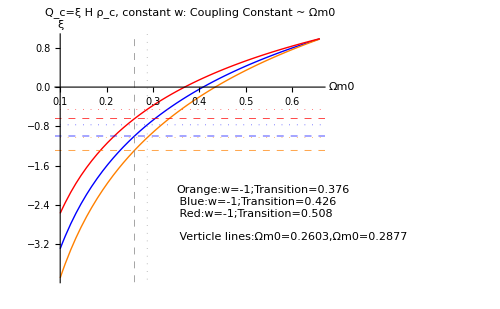

```mathematica
pltξvΩm0ICCSum=Plot[{ξICCffunc[Ωm0ICC,1-Ωm0ICC-0,-1,0.426],ξICCffunc[Ωm0ICC,1-Ωm0ICC-0,-1,0.376],ξICCffunc[Ωm0ICC,1-Ωm0ICC-0,-1,0.508]},{Ωm0ICC,0.1,0.66},PlotStyle->{Blue,Orange,Red},AxesLabel->{"Ωm0","ξ"},GridLines->{{{0.2603,Directive[Gray,Dashed]},{0.2877,Directive[Gray,Dotted]}},{{-1.2857,Directive[Orange,Dashed]},{-0.9943,Directive[Blue,Dashed]},{-0.6415,Directive[Red,Dashed]},{-1.0276,Directive[Orange,Dotted]},{-0.7676,Directive[Blue,Dotted]},{-0.4529,Directive[Red,Dotted]}}},Epilog->Inset[Framed[Style["Orange:w=-1;Transition=0.376\n Blue:w=-1;Transition=0.426\n Red:w=-1;Transition=0.508\n \n Verticle lines:Ωm0=0.2603,Ωm0=0.2877",11],Background->LightGreen,FrameStyle->None],{0.35,-2},{Left,Top}],PlotLabel->"Q_c=ξ H ρ_c, constant w: Coupling Constant ~ Ωm0",ImageSize->500]
```

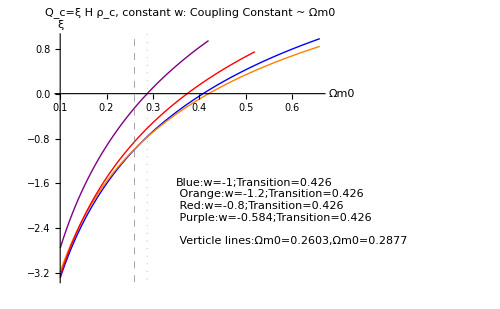

```mathematica
pltξvΩm0ICCSum2=Show[{Plot[{ξICCffunc[Ωm0ICC,1-Ωm0ICC-0,-1,0.426],ξICCffunc[Ωm0ICC,1-Ωm0ICC-0,-1.2,0.426]},{Ωm0ICC,0.1,0.66},PlotStyle->{Blue,Orange},AxesLabel->{"Ωm0","ξ"}],Plot[ξICCffunc[Ωm0ICC,1-Ωm0ICC-0,-0.8,0.426],{Ωm0ICC,0.1,0.52},PlotStyle->Red,AxesLabel->{"Ωm0","ξ"}],Plot[ξICCffunc[Ωm0ICC,1-Ωm0ICC-0,eosICC1/.FindRoot[{ξICCffunc[0.2877,1-0.2877-0,eosICC1,0.426]==0},{eosICC1,-0.5}],0.426],{Ωm0ICC,0.1,0.42},PlotStyle->Purple,AxesLabel->{"Ωm0","ξ"}]},GridLines->{{{0.2603,Directive[Gray,Dashed]},{0.2877,Directive[Gray,Dotted]}},{}},Epilog->Inset[Framed[Style["Blue:w=-1;Transition=0.426\n Orange:w=-1.2;Transition=0.426\n Red:w=-0.8;Transition=0.426\n Purple:w=-0.584;Transition=0.426\n \n Verticle lines:Ωm0=0.2603,Ωm0=0.2877",11],Background->LightGreen,FrameStyle->None],{0.35,-1.5},{Left,Top}],PlotLabel->"Q_c=ξ H ρ_c, constant w: Coupling Constant ~ Ωm0",ImageSize->500]//Quiet
```

Different plot ranges are chosen because for very large Ωm0, it is impossible to choose a parameter so that the transition redshift is

```mathematica
tabξvΩm0ICCSum21=Grid[{{"Q_c=ξ H ρ_c, constant w: ξ when transition redshift is 0.426",SpanFromLeft},{"⋱","w=-0.45064","w=-0.45063"},{"Ωm0=0.2603",ξICCffunc[0.2603,1-0.2603-0,-0.45064,0.426],ξICCffunc[0.2603,1-0.2603-0,-0.45063,0.426]}},Frame->All,Background->{{LightGray,None},{LightGreen,LightGray,None}},ItemSize->13]//Quiet
tabξvΩm0ICCSum22=Grid[{{"Q_c=ξ H ρ_c, constant w:EoS value when ξ=0",SpanFromLeft},{"⋱","Transition 0.426"},{"Ωm0=0.2877",eosICC1/.FindRoot[{ξICCffunc[0.2877,1-0.2877-0,eosICC1,0.426]==0},{eosICC1,-0.5}]}},Frame->All,ItemSize->13,Background->{{LightGray,None},{LightGreen,LightGray,None}}]//Quiet
```

Q_c=ξ H ρ_c, constant w: ξ when transition redshift is 0.426 |  | 
⋱ | w=-0.45064 | w=-0.45063
Ωm0=0.2603 | 0.999886 | -3.64749

Q_c=ξ H ρ_c, constant w:EoS value when ξ=0 | 
⋱ | Transition 0.426
Ωm0=0.2877 | -0.58406

So we give the result that w∈(-0.58406, -0.45064) if we constrain Ωm0=0.2603 and transition redshift 0.426.

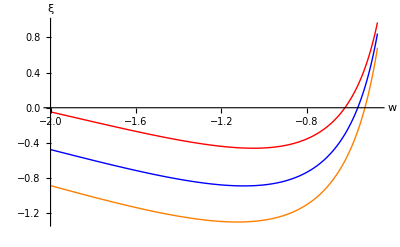

```mathematica
pltξvwICC=Plot[{ξICCfc[wICC],ξICCf1[wICC],ξICCf2[wICC]},{wICC,-2,-0.47},PlotStyle->{Blue,Orange,Red},AxesLabel->{"w","ξ"}]
```

Choose the values from Reference 3. w = -1.087 ± 0.096,

```mathematica
ξvwExamICC={Block[{wICC=-1.087-0.096},{wICC,ξICCfc[wICC],ξICCf1[wICC],ξICCf2[wICC]}],Block[{wICC=-1.087},{wICC,ξICCfc[wICC],ξICCf1[wICC],ξICCf2[wICC]}],Block[{wICC=-1.087+0.096},{wICC,ξICCfc[wICC],ξICCf1[wICC],ξICCf2[wICC]}]}
```

{{-1.183,-0.881565,-1.29687,-0.443589},{-1.087,-0.88948,-1.29859,-0.459135},{-0.991,-0.875238,-1.27522,-0.456176}}

```mathematica
tabξvwExamICC=Grid[Prepend[Prepend[ξvwExamICC,{"w","Center","Lower","Upper"}],{"ξ results for Q_c=ξ H ρ_c (Fitting data: Data From, 2)",SpanFromLeft}],Frame->All,Background->{{LightGray,None},{LightGreen,LightGray,None}},Alignment->Center,ItemSize->8]
```

ξ results for Q_c=ξ H ρ_c (Fitting data: Data From, 2) |  |  | 
w | Center | Lower | Upper
-1.183 | -0.881565 | -1.29687 | -0.443589
-1.087 | -0.88948 | -1.29859 | -0.459135
-0.991 | -0.875238 | -1.27522 | -0.456176

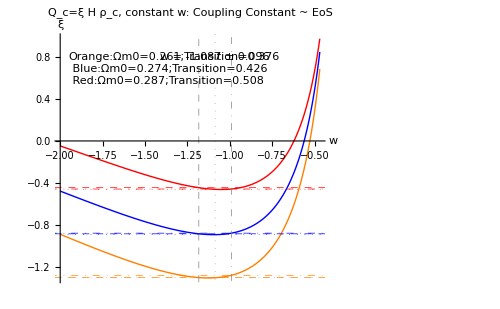

```mathematica
pltξvwExamICC=Show[pltξvwICC,GridLines->{{{ξvwExamICC[[1,1]],Directive[Gray,Dashed]},{ξvwExamICC[[2,1]],Directive[Gray,Dotted]},{ξvwExamICC[[3,1]],Directive[Gray,DotDashed]}},{{ξvwExamICC[[1,3]],Directive[Orange,Dashed]},{ξvwExamICC[[1,2]],Directive[Blue,Dashed]},{ξvwExamICC[[1,4]],Directive[Red,Dashed]},{ξvwExamICC[[2,3]],Directive[Orange,Dotted]},{ξvwExamICC[[2,2]],Directive[Blue,Dotted]},{ξvwExamICC[[2,4]],Directive[Red,Dotted]},{ξvwExamICC[[3,3]],Directive[Orange,DotDashed]},{ξvwExamICC[[3,2]],Directive[Blue,DotDashed]},{ξvwExamICC[[3,4]],Directive[Red,DotDashed]}}},Epilog->{Inset[Framed[Style["w = -1.087 ± 0.096",10],Background->LightBlue,FrameStyle->None],{-1.087,0.8},{0,Top}],Inset[Framed[Style["Orange:Ωm0=0.261;Transition=0.376\n Blue:Ωm0=0.274;Transition=0.426\n Red:Ωm0=0.287;Transition=0.508",11],Background->LightGreen,FrameStyle->None],{-1.95,0.84},{Left,Top}]},PlotLabel->"Q_c=ξ H ρ_c, constant w: Coupling Constant ~ EoS",ImageSize->500]
```

Or more casually, use w=-1±0.05

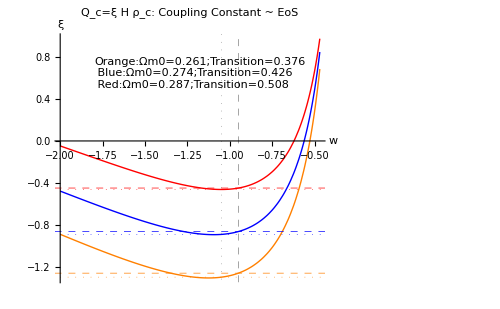

```mathematica
pltξvwExam1ICC=Show[pltξvwICC,GridLines->{{{-0.95,Directive[Gray,Dashed]},{-1.05,Directive[Gray,Dotted]}},{{-1.255,Directive[Orange,Dashed]},{-0.860,Directive[Blue,Dashed]},{-0.447,Directive[Red,Dashed]},{-1.293,Directive[Orange,Dotted]},{-0.887,Directive[Blue,Dotted]},{-0.461,Directive[Red,Dotted]}}},Epilog->Inset[Framed[Style["Orange:Ωm0=0.261;Transition=0.376\n Blue:Ωm0=0.274;Transition=0.426\n Red:Ωm0=0.287;Transition=0.508",11],Background->LightGreen,FrameStyle->None],{-1.8,0.8},{Left,Top}],PlotLabel->"Q_c=ξ H ρ_c: Coupling Constant ~ EoS"]
```

Now we assume we do not have the observed Ωm0 data, how do this Ωm0 change the result. In other words, if the observed Ωm0 data float around some value, then how is the fitting result? We also consider the curvature.

```mathematica
fitξ2ICCManSum=Manipulate[numPlot["(",{ξICCffunc[Ωm0ICC,1-Ωm0ICC-Ωk0ICC,wICC,0.376],ξICCffunc[Ωm0ICC,1-Ωm0ICC-Ωk0ICC,wICC,0.426],ξICCffunc[Ωm0ICC,1-Ωm0ICC-Ωk0ICC,wICC,0.508]},")",{-2.5,1}],{{Ωm0ICC,0.274,"Matter Fraction"},0.1,0.66,Appearance->"Open"},{{Ωk0ICC,0,"Curvature"},-0.1,0.1,Appearance->"Open"},{{wICC,-1,"Equation of State"},-2,-0.47,Appearance->"Open"},Delimiter,Style["Model: Q_c=ξ H ρ_c, constant w, constant ξ",Bold,Medium],Delimiter,Style["This is the fitting result of ξ from only transition redshift data.\n without the knowledge of Ωm0. "],Delimiter,Style["Slide to check how do EoS change this curve."],ControlPlacement->{Right},SaveDefinitions->True]
```

```mathematica
{tmpe/.FindRoot[ztrICC[tmpe,1-tmpe,-1,0.1]==0,{tmpe,0.1}],tmpe/.FindRoot[ztrICC[tmpe,1-tmpe,-1,0.1]==0,{tmpe,0.2}]}
```

{0.666667,0.666667}

```mathematica
pltξvΩm0ICCManSum=Manipulate[Plot[{ξICCffunc[Ωm0ICC,1-Ωm0ICC-Ωk0ICC,wICC,0.426],ξICCffunc[Ωm0ICC,1-Ωm0ICC-Ωk0ICC,wICC,0.376],ξICCffunc[Ωm0ICC,1-Ωm0ICC-Ωk0ICC,wICC,0.508]},{Ωm0ICC,0.1,(tmpe/.FindRoot[ztrICC[tmpe,1-tmpe-Ωk0ICC,wICC,0.1]==0,{tmpe,0.1}])-0.001},PlotStyle->{Blue,Orange,Red},AxesLabel->{"Ωm0","ξ"},PlotLabel->"Q_c=ξ H ρ_c: Coupling Constant ~ Ωm0"],{{Ωk0ICC,0,"Curvature"},-0.1,0.1,Appearance->"Open"},{{wICC,-1,"Equation of State"},-2,-0.47,Appearance->"Open"},Delimiter,Style["Blue line is the center of ξ\n The other lines are the upper and lower value"],Delimiter,Style["Slide to check how do matter change this curve."],ControlPlacement->{Right},SaveDefinitions->True]
```

To summarize, taken the case that the universe is flat, and choose the parameters to be {w=-1}, the region for interaction constant ξ should be (-0.46, -1.28) with a center at -0.88, i.e., -0.88_-0.40^(+0.42) .

```mathematica
ztrrICC[0.358,-1,ξICC]==0.376
```

-1+0.179^(1/(-3+ξICC)) (-(1+(2 ξICC)/(-3+ξICC))/(-1-(0.358 ξICC)/(-3+ξICC)))^(1/(-3+ξICC))==0.376

```mathematica
ξICCrffunc[rICC_,wICC_,data_]:=ξICC/.FindRoot[ztrrICC[rICC,wICC,ξICC]==data,{ξICC,-0.6}]
```

```mathematica
ξICCrf2[wICC_]:=ξICCrffunc[0.398, wICC, 0.508]
```

```mathematica
ξICCrf1[wICC_]:=ξICCrffunc[0.358, wICC, 0.376]
```

Center

```mathematica
ξICCrfc[wICC_]:=ξICCrffunc[0.378, wICC, 0.426]
```

A example is ( w=-1 )

```mathematica
{ξICCrf1[-1],ξICCrfc[-1],ξICCrf2[-1]}
```

{-1.25282,-0.875189,-0.472561}

To summarize, taken the case that the universe is flat, and choose the parameters to be {w=-1}, the region for interation cosntant ξ should be (-1.25, -0.47) with a center at -0.88, i.e., -0.88_-0.37^(+0.41) .

Or more detailed

```mathematica
tabξFinaltICC=Grid[Prepend[MapThread[Prepend,{Prepend[{{Item[ξICCrffunc[0.358,-1,0.376],Background->LightPurple],ξICCrffunc[0.358,-1,0.426],ξICCrffunc[0.358,-1,0.508]},{ξICCrffunc[0.378,-1,0.376],Item[ξICCrffunc[0.378,-1,0.426],Background->LightPurple],ξICCrffunc[0.378,-1,0.508]},{ξICCrffunc[0.398,-1,0.376],ξICCrffunc[0.398,-1,0.426],Item[ξICCrffunc[0.398,-1,0.508],Background->LightPurple]}},{"z_t=0.376","z_t=0.426","z_t=0.508"}],{Style["Ωm0/Ωd0⋱Transition",Small],"r=0.358","r=0.378","r=0.398"}}],{"Q_c=ξ H ρ_c, constant ξ, constant w=-1: Results for ξ",SpanFromLeft}],Background->{{LightGray,None},{LightGreen,LightGray,None}},Frame->All,ItemSize->8]
```

Q_c=ξ H ρ_c, constant ξ, constant w=-1: Results for ξ |  |  | 
Ωm0/Ωd0⋱Transition | z_t=0.376 | z_t=0.426 | z_t=0.508
r=0.358 | -1.25282 | -0.965436 | -0.617444
r=0.378 | -1.15011 | -0.875189 | -0.542347
r=0.398 | -1.05453 | -0.791252 | -0.472561

This is a bit different from the result we got from Ωm0~ transition redshift plane. One possible reason is the second method doesn’t assume a flat universe, while the first one supposes the universe is flat.

In arXiv:0801.4233, a CPL parameterization of EoS and three-year WMAP data, SN Ia data, BAO gives a result of ξ~-0.02

#### Check consistancy

The consistancy between (Transition, Ωm0) plane fitting and (Transition, Ωm0/Ωd0) plane fitting is checked.
For a flat universe, r=Ωm0/(1-Ωm0). Solve out Ωm0, we get Ωm0=r/(1+r)(this is a monotonic function). Thus if we use the constrain that r∈(0.358, 0.398) with a center value 0.378, the value of Ωm0 is

```mathematica
{0.358/(1+0.358),0.378/(1+0.378),0.398/(1+0.398)}
```

{0.263623,0.274311,0.284692}

```mathematica
{ξICCffunc[0.263623,1-0.263623,-1,0.376],ξICCffunc[0.274310595065312,1-0.274310595065312,-1,0.426],ξICCffunc[0.28469241773962806,1-0.28469241773962806,-1,0.508]}
```

{-1.25282,-0.875189,-0.472561}

This result is exactly the same as the results from (Transition, r) plane.

### δ is constant + EoS w CPL

#### Definations and functions.

CPL EoS w=w0+w1 z/(1+z)

Useful relations.

```mathematica
hubblecmpintICCPL[w0_,w1_,ξICCPL_,z_]=Integrate[Exp[-3 w1/(1+tmp)](1+tmp)^(-3(w0+w1)-ξICCPL-1),{tmp,0,z},Assumptions->{tmp∈Reals&&z∈Reals&&z>-1}]
```

-ExpIntegralE[1-3 (w0+w1)-ξICCPL,3 w1]+(1/(1+z))^(3 (w0+w1)+ξICCPL) ExpIntegralE[1-3 (w0+w1)-ξICCPL,(3 w1)/(1+z)]

```mathematica
hubblecmpintICCPLtest[w0_,w1_,ξICCPL_,z_?NumberQ]:=NIntegrate[Exp[-3 w1/(1+tmp)](1+tmp)^(-3(w0+w1)-ξICCPL-1),{tmp,0,z}]
```

```mathematica
ΩdICCPLtest[Ωd0_,Ωm0_,w0_,w1_,ξICCPL_,z_]:=Ωm0 (1+z)^(3(1+w0+w1))Exp[3 w1/(1+z)]ξICCPL hubblecmpintICCPLtest[w0,w1,ξICCPL,z]+ Ωd0 (1+z)^(3(1+w0+w1))Exp[3 w1/(1+z)-3w1]//Simplify
```

```mathematica
hubblecmpintICCPLtest[-1,0.6,-0.2,10]//Timing
```

{0.031,14.1439}

```mathematica
hubblecmpintICCPL[-1,0.6,-0.2,5]//Timing
```

{0.,4.68394+0. ⅈ}

```mathematica
Re[hubblecmpintICCPL[-1,0.6,-0.2,10]//Timing]
```

{0.,14.1439}

Fraction energy density

```mathematica
ΩmICCPL[Ωm0_,ξICCPL_,z_]:=Ωm0 (1+z)^(3-ξICCPL)
```

```mathematica
ΩdICCPL[Ωd0_,Ωm0_,w0_,w1_,ξICCPL_,z_]:=Ωm0 (1+z)^(3(1+w0+w1))Exp[3 w1/(1+z)]ξICCPL hubblecmpintICCPL[w0,w1,ξICCPL,z]+ Ωd0 (1+z)^(3(1+w0+w1))Exp[3 w1/(1+z)-3w1]//Simplify
```

Hubble function

```mathematica
hubbleICCPL[H0ICCPL_,Ωd0ICCPL_,Ωm0ICCPL_,w0ICCPL_,w1ICCPL_,ξICCPL_,z_]:=H0ICCPL√(ΩmICCPL[Ωm0ICCPL,ξICCPL,z]+ΩdICCPL[Ωd0ICCPL,Ωm0ICCPL,w0ICCPL,w1ICCPL,ξICCPL,z])
```

```mathematica
hubbleDICCPL[H0ICCPL_,Ωd0ICCPL_,Ωm0ICCPL_,w0ICCPL_,w1ICCPL_,ξICCPL_,z_]=D[hubbleICCPL[H0ICCPL,Ωd0ICCPL,Ωm0ICCPL,w0ICCPL,w1ICCPL,ξICCPL,z],z];
```

Deceleration parameter

```mathematica
qICCPL[H0ICCPL_,Ωd0ICCPL_,Ωm0ICCPL_,w0ICCPL_,w1ICCPL_,ξICCPL_,z_]:=-1+(1+z)/hubbleICCPL[H0ICCPL,Ωd0ICCPL,Ωm0ICCPL,w0ICCPL,w1ICCPL,ξICCPL,z]hubbleDICCPL[H0ICCPL,Ωd0ICCPL,Ωm0ICCPL,w0ICCPL,w1ICCPL,ξICCPL,z]
```

Check the definations and functions.

```mathematica
Re[hubbleDICCPL[H0w,Ωd0w,Ωm0w,-1,0.6,-0.02,10]]
```

188.13

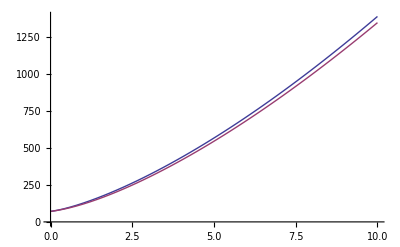

```mathematica
Plot[{hubbleICCPL[H0w,0.73,0.27,-1,0.6,-0.02,z],hubble[Ωm0w,Ωd0w,0,z]},{z,0,10}]
```

#### Equation of State

The equation of state

```mathematica
plEoSICCPLMan=Manipulate[Plot[{w0+w1 z/(1+z),-1},{z,-0.99,10},AxesLabel->{"z","w"}],{{w0,-1,"w0"},-2,0,Appearance->"Open"},{{w1,0,"w1"},-1,1,Appearance->"Open"},Delimiter,Style["This is the EoS of CPL paramterization."],ControlPlacement->{Right,Right},SaveDefinitions->True]
```

It is clear that the line is mono. Now we category it into phantom, quintessence and quintom. Limit of w at z->∞ is w0+w1.

w1>0, monotone-increasing function.

w0+w1>-1  Quintom

w0+w1=- 1 Then w0 must be -1 and w1=0.

w0+w1<-1  Phantom

w1<0, monotone-decreasing function.

w0+w1>-1  Quintessence

w0+w1=-1  Then w0 must be -1 and w1=0.

w0+w1<-1  Quintom

Thus we can draw a map of EoS on which we color out different categories.

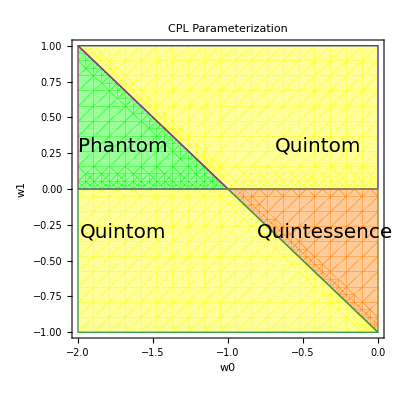

```mathematica
plEoSPhaseICCPL=RegionPlot[{w0+w1>-1&&w1>0,w0+w1<=-1&&w1>0,w0+w1>-1&&w1<0,w0+w1<=-1&&w1<0},{w0,-2,0},{w1,-1,1},PlotStyle->{Directive[Yellow,Opacity[0.4]],Directive[Green,Opacity[0.4]],Directive[Orange,Opacity[0.4]]},Epilog->{Inset[Style["Phantom",20],{-1.7,0.3},{0,0}],Inset[Style["Quintom",20],{-1.7,-0.3},{0,0}],Inset[Style["Quintom",20],{-0.4,0.3},{0,0}],Inset[Style["Quintessence",20],{-0.35,-0.3},{0,0}]},Frame->True,FrameLabel->{"w0","w1"},PlotLabel->"CPL Parameterization",ImageSize->400]
```

#### Plots, showcase, examinations

```mathematica
pldecICCPL[Ωm0ICCPL_,ξICCPL_,w0ICCPL_,w1ICCPL_,color_]:=Plot[Re[qICCPL[H0w,1-Ωm0ICCPL,Ωm0ICCPL,w0ICCPL,w1ICCPL,ξICCPL,z]],{z,-1,20},PlotRange->{{-1.05,20},{-1.05,1}},PlotStyle->color,AxesOrigin->{-1,0},AxesLabel->{z,q}];
```

Check the effects of different parameters.

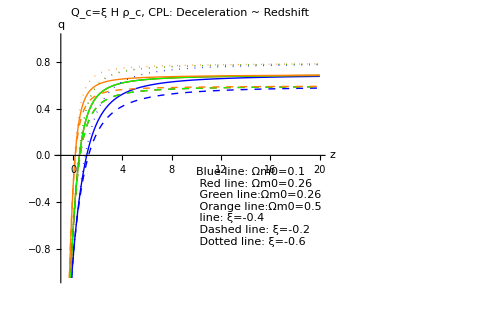

```mathematica
pldecICCPLShowSum=Show[{pldecICCPL[0.1,-0.4,-1.02,0.60,Blue],pldecICCPL[0.26,-0.4,-1.02,0.60,Red],pldecICCPL[0.26,-0.4,-1.02,0.60,Green],pldecICCPL[0.5,-0.4,-1.02,0.60,Orange],pldecICCPL[0.1,-0.2,-1.02,0.60,Directive[Blue,Dashed]],pldecICCPL[0.26,-0.2,-1.02,0.60,Directive[Red,Dashed]],pldecICCPL[0.26,-0.2,-1.02,0.60,Directive[Green,Dashed]],pldecICCPL[0.5,-0.2,-1.02,0.60,Directive[Orange,Dashed]],pldecICCPL[0.1,-0.6,-1.02,0.60,Directive[Blue,Dotted]],pldecICCPL[0.26,-0.6,-1.02,0.60,Directive[Red,Dotted]],pldecICCPL[0.26,-0.6,-1.02,0.60,Directive[Green,Dotted]],pldecICCPL[0.5,-0.6,-1.02,0.60,Directive[Orange,Dotted]]},Epilog->Inset[Framed[Style["Blue line: Ωm0=0.1\n Red line: Ωm0=0.26\n Green line:Ωm0=0.26\n Orange line:Ωm0=0.5\n line: ξ=-0.4\n Dashed line: ξ=-0.2\n Dotted line: ξ=-0.6",10],Background->LightGreen,FrameStyle->None],{10,-0.1},{Left,Top}],PlotLabel->"Q_c=ξ H ρ_c, CPL: Deceleration ~ Redshift",ImageSize->500]
```

z->Infinity is a degenerate limit. For constant ξ and constant w models, this limit is determined by the interaction strength ξ . This might be useful if more complicated models are investigated and no large deviations are shown. [Nota]

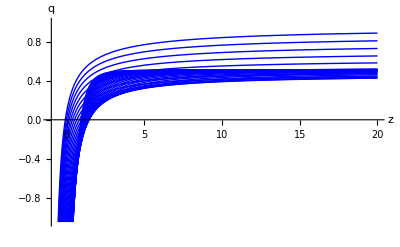
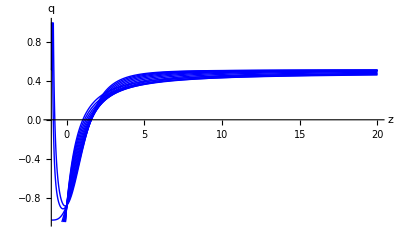
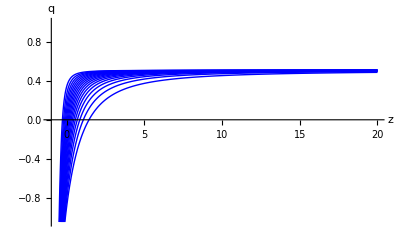
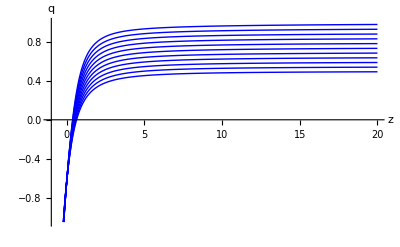
Q_c=ξ H ρ_c, CPL |  |  | 
Varying CPL w0 | Varying CPL w1 | Varying Ωm0 | Varying ξ
-Graphics- | -Graphics- | -Graphics- | -Graphics-

```mathematica
varyingICCPLShowSum=Grid[{{"Q_c=ξ H ρ_c, CPL",SpanFromLeft},{"Varying CPL w0","Varying CPL w1","Varying Ωm0","Varying ξ"},{Show[Table[pldecICCPL[0.1,-0.02,w0ICCPL,0.6,Blue],{w0ICCPL,-2,-0.3,0.05}]],Show[Table[pldecICCPL[0.1,-0.02,-1.02,w1ICCPL,Blue],{w1ICCPL,-0.2,1,0.1}]],Show[Table[pldecICCPL[Ωm0ICCPL,-0.02,-1.02,0.6,Blue],{Ωm0ICCPL,0.1,0.9,0.05}]],Show[Table[pldecICCPL[0.27,ξICCPL,-1.02,0.6,Blue],{ξICCPL,-1,0,0.1}]]}},Frame->All,Background->{{None},{LightGreen,None}}]
```

Interaction ξ changes the limit, i.e., what value will it be at z->Infinity. EoS changes the the whole shape. Matter fraction also changes how fast q varies, but just in a small time scale.

Use movable slides to check how do the parameters affect the deceleration parameter. Just a toy.

```mathematica
pldecICCPLManSum=Manipulate[Show[{pldecICCPL[Ωm0ICCPL,ξICCPL,w0ICCPL,w1ICCPL,Orange],pldec[Ωm0ICCPL,{Pink,Thick}]},PlotLabel->"Q_c=ξ H ρ_c,CPL: Deceleration ~ Redshift"],{{Ωm0ICCPL,0.26,"Matter Fraction"},0,1,Appearance->"Open"},{{ξICCPL,-0.4,"Interaction"},-1,0,Appearance->"Open"},{{w0ICCPL,-1.02,"CPL EoS w0"},-2,-0.3,Appearance->"Open"},{{w1ICCPL,0.6,"CPL EoS w1"},-0.2,1,Appearance->"Open"},Delimiter,Style["Pink is the deceleration parameter for LCDM.",Medium],Style["Orange is for interacting CPL model with Q=ξ H ρ_m",Medium],ControlPlacement->{Right,Right,Right},SaveDefinitions->True]
```

#### Transition redshift

Find out the expression for transition redshift

```mathematica
ztrICCPL[Ωm0ICCPL_,Ωd0ICCPL_,ξICCPL_,w0ICCPL_,w1ICCPL_]=Re[z/.FindRoot[(1+3(w0ICCPL+w1ICCPL z/(1+z)))ΩdICCPL[Ωd0ICCPL,Ωm0ICCPL,w0ICCPL,w1ICCPL,ξICCPL,z]+ΩmICCPL[Ωm0ICCPL,ξICCPL,z]==0,{z,3}]];
```

FindRoot::nlnum: The function value {4.^3.  - 1.\ ξICCPL\ Ωm0ICCPL + 2.71828^0.75\ w1ICCPL\ 4.^3.\ (1.  + w0ICCPL + w1ICCPL)\ (1.  + 3.\ (w0ICCPL + 0.75\ w1ICCPL))\ (2.71828^-3.\ w1ICCPL\ Ωd0ICCPL + 0.25^Times[« 2 »] + Times[« 2 »] + ξICCPL\ ξICCPL\ Ωm0ICCPL\ ExpIntegralE[1.  + Times[« 2 »] + Times[« 2 »], 0.75\ w1ICCPL] - 1.\ ξICCPL\ Ωm0ICCPL\ ExpIntegralE[1.  + Times[« 2 »] + Times[« 2 »], 3.\ w1ICCPL])}
 is not a list of numbers with dimensions {1} at {z} = {3.}.

ReplaceAll::reps: {FindRoot[(1 + 3\ Plus[« 2 »])\ ΩdICCPL[Ωd0ICCPL, Ωm0ICCPL, w0ICCPL, w1ICCPL, ξICCPL, z] + ΩmICCPL[Ωm0ICCPL, ξICCPL, z] == 0, {z, 3}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

FindRoot::nlnum: The function value {4.^3.  - 1.\ ξICCPL\ Ωm0ICCPL + 2.71828^0.75\ w1ICCPL\ 4.^3.\ (1.  + w0ICCPL + w1ICCPL)\ (1.  + 3.\ (w0ICCPL + 0.75\ w1ICCPL))\ (2.71828^-3.\ w1ICCPL\ Ωd0ICCPL + 0.25^Times[« 2 »] + Times[« 2 »] + ξICCPL\ ξICCPL\ Ωm0ICCPL\ ExpIntegralE[1.  + Times[« 2 »] + Times[« 2 »], 0.75\ w1ICCPL] - 1.\ ξICCPL\ Ωm0ICCPL\ ExpIntegralE[1.  + Times[« 2 »] + Times[« 2 »], 3.\ w1ICCPL])}
 is not a list of numbers with dimensions {1} at {z} = {3.}.

ReplaceAll::reps: {FindRoot[(1 + 3\ Plus[« 2 »])\ ΩdICCPL[Ωd0ICCPL, Ωm0ICCPL, w0ICCPL, w1ICCPL, ξICCPL, z] + ΩmICCPL[Ωm0ICCPL, ξICCPL, z] == 0, {z, 3}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

```mathematica
ztrICCPLtest2[Ωm0ICCPL_,Ωd0ICCPL_,ξICCPL_,w0ICCPL_,w1ICCPL_]=Re[z/.FindRoot[(1+3(w0ICCPL+w1ICCPL z/(1+z)))ΩdICCPL[Ωd0ICCPL,Ωm0ICCPL,w0ICCPL,w1ICCPL,ξICCPL,z]+ΩmICCPL[Ωm0ICCPL,ξICCPL,z]==0,{z,3}]];
```

FindRoot::nlnum: The function value {4.^3.  - 1.\ ξICCPL\ Ωm0ICCPL + 2.71828^0.75\ w1ICCPL\ 4.^3.\ (1.  + w0ICCPL + w1ICCPL)\ (1.  + 3.\ (w0ICCPL + 0.75\ w1ICCPL))\ (2.71828^-3.\ w1ICCPL\ Ωd0ICCPL + 0.25^Times[« 2 »] + Times[« 2 »] + ξICCPL\ ξICCPL\ Ωm0ICCPL\ ExpIntegralE[1.  + Times[« 2 »] + Times[« 2 »], 0.75\ w1ICCPL] - 1.\ ξICCPL\ Ωm0ICCPL\ ExpIntegralE[1.  + Times[« 2 »] + Times[« 2 »], 3.\ w1ICCPL])}
 is not a list of numbers with dimensions {1} at {z} = {3.}.

ReplaceAll::reps: {FindRoot[(1 + 3\ Plus[« 2 »])\ ΩdICCPL[Ωd0ICCPL, Ωm0ICCPL, w0ICCPL, w1ICCPL, ξICCPL, z] + ΩmICCPL[Ωm0ICCPL, ξICCPL, z] == 0, {z, 3}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

FindRoot::nlnum: The function value {4.^3.  - 1.\ ξICCPL\ Ωm0ICCPL + 2.71828^0.75\ w1ICCPL\ 4.^3.\ (1.  + w0ICCPL + w1ICCPL)\ (1.  + 3.\ (w0ICCPL + 0.75\ w1ICCPL))\ (2.71828^-3.\ w1ICCPL\ Ωd0ICCPL + 0.25^Times[« 2 »] + Times[« 2 »] + ξICCPL\ ξICCPL\ Ωm0ICCPL\ ExpIntegralE[1.  + Times[« 2 »] + Times[« 2 »], 0.75\ w1ICCPL] - 1.\ ξICCPL\ Ωm0ICCPL\ ExpIntegralE[1.  + Times[« 2 »] + Times[« 2 »], 3.\ w1ICCPL])}
 is not a list of numbers with dimensions {1} at {z} = {3.}.

ReplaceAll::reps: {FindRoot[(1 + 3\ Plus[« 2 »])\ ΩdICCPL[Ωd0ICCPL, Ωm0ICCPL, w0ICCPL, w1ICCPL, ξICCPL, z] + ΩmICCPL[Ωm0ICCPL, ξICCPL, z] == 0, {z, 3}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

The following is just used for test.

```mathematica
ztrICCPLtest[Ωm0ICCPL_,Ωd0ICCPL_,ξICCPL_,w0ICCPL_,w1ICCPL_]:=z/.FindRoot[(1+3(w0ICCPL+w1ICCPL z/(1+z)))ΩdICCPLtest[Ωd0ICCPL,Ωm0ICCPL,w0ICCPL,w1ICCPL,ξICCPL,z]+ΩmICCPL[Ωm0ICCPL,ξICCPL,z]==0,{z,3}]
ztrICCPLtest[0.274,1-0.274,-0.02,-1,0.6]
ztrICCPLtest[0.1,1-0.1,-0.1,-0.9,-0.05]
ztrICCPL[0.1,1-0.1,-0.1,-0.9,-0.05]
ztrICCPLtest2[0.1,1-0.1,-0.1,-0.9,-0.05]
plottestfunctiontemp[Ωm0ICCPL_,Ωd0ICCPL_,ξICCPL_,w0ICCPL_,w1ICCPL_,z_]:=(1+3(w0ICCPL+w1ICCPL z/(1+z)))ΩdICCPLtest[Ωd0ICCPL,Ωm0ICCPL,w0ICCPL,w1ICCPL,ξICCPL,z]+ΩmICCPL[Ωm0ICCPL,ξICCPL,z]
```

0.600079

1.59781

1.59781

1.59781

```mathematica
(*
(*This is a test of how well are the findroot results.*)
Plot[{plottestfunctiontemp[temp,1-temp,-0.1,-0.9,-0.05,ztrICCPLtest2[temp,1-temp,-0.1,-0.9,-0.05]],plottestfunctiontemp[temp,1-temp,-0.1,-0.9,-0.05,ztrICCPLtest[temp,1-temp,-0.1,-0.9,-0.05]],plottestfunctiontemp[temp,1-temp,-0.1,-0.9,-0.05,ztrICCPL[temp,1-temp,-0.1,-0.9,-0.05]]},{temp,0,1},PlotStyle->{Red,Orange,Blue}]
*)
```

Define rICC=Ωm0ICC/Ωd0ICC

```mathematica
ΩmrICCPL[rICCPL_,ξICCPL_,z_]=rICCPL (1+z)^(3-ξICCPL);
```

```mathematica
ΩdrICCPL[rICCPL_,w0ICCPL_,w1ICCPL_,ξICCPL_,z_]=rICCPL (1+z)^(3(1+w0ICCPL+w1ICCPL))Exp[3 w1ICCPL/(1+z)]ξICCPL hubblecmpintICCPL[w0ICCPL,w1ICCPL,ξICCPL,z]+ (1+z)^(3(1+w0ICCPL+w1ICCPL))Exp[3 w1ICCPL/(1+z)-3w1ICCPL]//Simplify;
```

```mathematica
ztrrICCPL[rICCPL_,ξICCPL_,w0ICCPL_,w1ICCPL_]=Re[z/.FindRoot[(1+3(w0ICCPL+w1ICCPL z/(1+z)))ΩdrICCPL[rICCPL,w0ICCPL,w1ICCPL,ξICCPL,z]+ΩmrICCPL[rICCPL,ξICCPL,z]==0,{z,3}]];
```

FindRoot::nlnum: The function value {4.^3.  - 1.\ ξICCPL\ rICCPL + 2.71828^0.75\ w1ICCPL\ 4.^3.\ (1.  + w0ICCPL + w1ICCPL)\ (1.  + 3.\ (w0ICCPL + 0.75\ w1ICCPL))\ (2.71828^-3.\ w1ICCPL + 0.25^Times[« 2 »] + Times[« 2 »] + ξICCPL\ rICCPL\ ξICCPL\ ExpIntegralE[1.  + Times[« 2 »] + Times[« 2 »], 0.75\ w1ICCPL] - 1.\ rICCPL\ ξICCPL\ ExpIntegralE[1.  + Times[« 2 »] + Times[« 2 »], 3.\ w1ICCPL])}
 is not a list of numbers with dimensions {1} at {z} = {3.}.

ReplaceAll::reps: {FindRoot[(1 + 3\ Plus[« 2 »])\ ΩdrICCPL[rICCPL, w0ICCPL, w1ICCPL, ξICCPL, z] + ΩmrICCPL[rICCPL, ξICCPL, z] == 0, {z, 3}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

FindRoot::nlnum: The function value {4.^3.  - 1.\ ξICCPL\ rICCPL + 2.71828^0.75\ w1ICCPL\ 4.^3.\ (1.  + w0ICCPL + w1ICCPL)\ (1.  + 3.\ (w0ICCPL + 0.75\ w1ICCPL))\ (2.71828^-3.\ w1ICCPL + 0.25^Times[« 2 »] + Times[« 2 »] + ξICCPL\ rICCPL\ ξICCPL\ ExpIntegralE[1.  + Times[« 2 »] + Times[« 2 »], 0.75\ w1ICCPL] - 1.\ rICCPL\ ξICCPL\ ExpIntegralE[1.  + Times[« 2 »] + Times[« 2 »], 3.\ w1ICCPL])}
 is not a list of numbers with dimensions {1} at {z} = {3.}.

ReplaceAll::reps: {FindRoot[(1 + 3\ Plus[« 2 »])\ ΩdrICCPL[rICCPL, w0ICCPL, w1ICCPL, ξICCPL, z] + ΩmrICCPL[rICCPL, ξICCPL, z] == 0, {z, 3}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Test this.

```mathematica
ztrrICCPL[0.5,-0.02,-1,0.6]
ztrrICCPL[0.5,0,-1,0.6]
```

0.46757

0.474097

#### Visualization of transition redshift.

Check the behavior of this transition redshift.

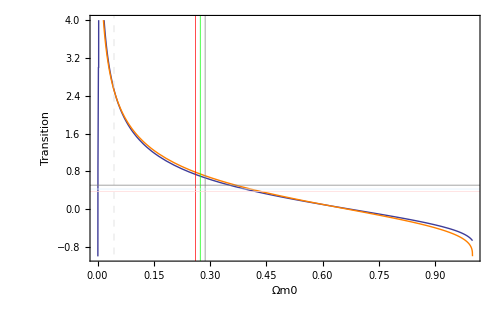

```mathematica
pldecΩm0ICCPL=Plot[{ztrICCPL[Ωm0ICCPL,1-Ωm0ICCPL,-0.02,-1.02,0.2],ztr[Ωm0ICCPL,1-Ωm0ICCPL]},{Ωm0ICCPL,0,1},PlotRange->{{0,1},{-1,4}},PlotStyle->{Thick,Orange},AxesOrigin->{0,-1},Frame->True,GridLines->{{{0.044,Dashed},{0.261,Red},{0.274,Green},{0.287,Gray}},{{0.376,LightRed},{0.426,LightBlue},{0.508,Gray}}},PlotLegend->{"Q=-0.02 H ρ_c","LCDM"},LegendPosition->{0.0,-0.05},LegendShadow->None,ImageSize->500,FrameLabel->{"Ωm0","Transition"}]
```

```mathematica
plztrICCPL[ξICCPL_,w0ICCPL_,w1ICCPL_,color_,{ranges_:0,rangee_:1}]:=Plot[ztrICCPL[Ωm0ICCPL,1-Ωm0ICCPL,ξICCPL,w0ICCPL,w1ICCPL],{Ωm0ICCPL,0,1},PlotRange->{{ranges,rangee},{-1,4}},PlotStyle->color,AxesOrigin->{0,-1},Frame->True,FrameLabel->{"Ωm0","Transtion"}];
```

```mathematica
plztrICCPLManSum=Manipulate[Show[{plztrICCPL[ξICCPL,w0ICCPL,w1ICCPL,Orange,{0,1}],Plot[ztr[Ωm0ICCPL,1-Ωm0ICCPL],{Ωm0ICCPL,0,1},PlotRange->{{0,1},{-1,4}},PlotStyle->Pink,AxesOrigin->{0,-1}]},Graphics[{Gray,Rectangle[Scaled[{0.261,.2752}],Scaled[{0.287,.3016}]]},Frame->True],GridLines->{{},{{0,Dashed}}},FrameLabel->{"Ωm0","Transition"},PlotLabel->"Q_c=ξ H ρ_c, CPL: Transition ~ Ωm0"],{{ξICCPL,-0.4,"Interaction"},-1,0,Appearance->"Open"},{{w0ICCPL,-1.02,"CPL EoS w0"},-2,-0.3,Appearance->"Open"},{{w1ICCPL,0.6,"CPL EoS w1"},-0.2,1,Appearance->"Open"},Delimiter,Style["Orange is for interacting CPL model with Q=ξ H ρ_m",Medium],ControlPlacement->{Right,Right,Right},SaveDefinitions->True]
```

```mathematica
plztrExamICCPLSum=Grid[{{Show[{plztrICCPL[-0.1,-1,0.6,Orange,{0,1}],plztrICCPL[-0.3,-1,0.6,{Blue,Dashed},{0,1}],plztrICCPL[-0.6,-1,0.6,{Green,Dotted},{0,1}],Plot[ztr[Ωm0ICCPL,1-Ωm0ICCPL],{Ωm0ICCPL,0,1},PlotRange->{{0,1},{-1,4}},PlotStyle->Pink,AxesOrigin->{0,-1}]},Graphics[{Gray,Rectangle[Scaled[{0.261,.2752}],Scaled[{0.287,.3016}]]},Frame->True],GridLines->{{},{{0,Dashed}}},Epilog->Inset[Framed[Style["Orange: w0=-1,w1=0.6,ξ=-0.1\n Blue dashed:w0=-1,w1=0.6,ξ=-0.3\n Green dotted:w0=-1,w1=0.6,ξ=-0.6\n Pink: LCDM",10],Background->LightGreen,FrameStyle->None],{0.3,3.5},{Left,Top}],FrameLabel->{"Ωm0","Transition"},PlotLabel->"Q_c=ξ H ρ_c, CPL: Transition ~ Ωm0",ImageSize->400],Show[{plztrICCPL[-0.3,-1,0.1,Red,{0,1}],plztrICCPL[-0.3,-1,0.4,{Purple,Dotted},{0,1}],plztrICCPL[-0.3,-1,0.8,{Magenta,Dashed},{0,1}],Plot[ztr[Ωm0ICCPL,1-Ωm0ICCPL],{Ωm0ICCPL,0,1},PlotRange->{{0,1},{-1,4}},PlotStyle->Pink,AxesOrigin->{0,-1}]},Graphics[{Gray,Rectangle[Scaled[{0.261,.2752}],Scaled[{0.287,.3016}]]},Frame->True],GridLines->{{},{{0,Dashed}}},Epilog->Inset[Framed[Style["Red: w0=-1,w1=0.1,ξ=-0.3\n Magenta dashed:w0=-1,w1=0.8,ξ=-0.3\n Purple dotted:w0=-1,w1=0.4,ξ=-0.3\n Pink: LCDM",10],Background->LightGreen,FrameStyle->None],{0.3,3.5},{Left,Top}],FrameLabel->{"Ωm0","Transition"},PlotLabel->"Q_c=ξ H ρ_c, CPL: Transition ~ Ωm0",ImageSize->400]}}]
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

-Graphics-

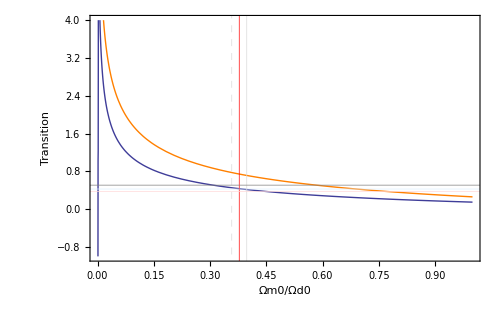

```mathematica
pldecrICCPL=Plot[{ztrrICCPL[rICCPL,-0.6,-1.02,0.6],ztrr[rICCPL]},{rICCPL,0,1},PlotRange->{{0,1},{-1,4}},PlotStyle->{Thick,Orange},AxesOrigin->{0,-1},Frame->True,GridLines->{{{0.358,Dashed},{0.378,Directive[Red]},0.398},{{0.376,LightRed},{0.426,LightBlue},{0.508,Gray}}},PlotLegend->{"CPL,Q=-0.6 H ρ_c","LCDM"},LegendPosition->{0.0,-0.05},LegendShadow->None,ImageSize->500,FrameLabel->{"Ωm0/Ωd0","Transition"}]
```

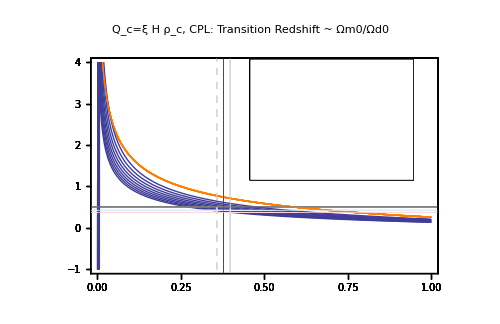

```mathematica
pltransrICCPLDense=Show[Table[Plot[{ztrrICCPL[rICCPL,ξICCPL,-1.02,0.6],ztrr[rICCPL]},{rICCPL,0,1},PlotRange->{{0,1},{-1,4}},PlotStyle->{Thick,Orange},AxesOrigin->{0,-1},Frame->True,GridLines->{{{0.358,Dashed},{0.378,Directive[Red]},0.398},{{0.376,LightRed},{0.426,LightBlue},{0.508,Gray}}},PlotLegend->{"CPL,Q=ξ H ρ_c,\n with ξ∈(-0.8,0) step=0.1","LCDM"},LegendPosition->{0.0,-0.05},LegendShadow->None],{ξICCPL,-0.8,0,0.1}],ImageSize->500,FrameLabel->{"Ωm0/Ωd0","Transition"},PlotLabel->"Q_c=ξ H ρ_c, CPL: Transition Redshift ~ Ωm0/Ωd0",ImageSize->500]
```

#### Find out allowed region of interactions.

To find out the region of ξ, set w=-1 and Ωd0=1-Ωm0. Let the ztr-Ωm0 line cross points (0.287,0.508) and (0.261, 0.376).

```mathematica
Off[FindRoot::nlnum]
Off[ReplaceAll::reps]
ztrICCPL[Ωm0ICCPL,Ωd0ICCPL,ξICCPL,w0ICCPL,w1ICCPL]
On[FindRoot::nlnum]
On[ReplaceAll::reps]
```

Re[z/.FindRoot[(1+3 (w0ICCPL+(w1ICCPL z)/(1+z))) ΩdICCPL[Ωd0ICCPL,Ωm0ICCPL,w0ICCPL,w1ICCPL,ξICCPL,z]+ΩmICCPL[Ωm0ICCPL,ξICCPL,z]==0,{z,3}]]

```mathematica
(* ztrICCPL[0.287,1-0.287,ξICCPL1,-1.02,0.6]==0.508 *)
```

```mathematica
ξICCPLffunc[Ωm0ICCPL_,Ωd0ICCPL_,w0ICCPL_,w1ICCPL_,data_]:=ξICCPL/.FindRoot[ztrICCPL[Ωm0ICCPL,Ωd0ICCPL,ξICCPL,w0ICCPL,w1ICCPL]==data,{ξICCPL,-0.6}]
```

```mathematica
ξICCPLf2[Ωm0ICCPL_,Ωd0ICCPL_,w0ICCPL_,w1ICCPL_]:=ξICCPL/.FindRoot[ztrICCPL[Ωm0ICCPL,Ωd0ICCPL,ξICCPL,w0ICCPL,w1ICCPL]==0.508,{ξICCPL,-0.6}]
```

```mathematica
ξICCPLf1[Ωm0ICCPL_,Ωd0ICCPL_,w0ICCPL_,w1ICCPL_]:=ξICCPL/.FindRoot[ztrICCPL[Ωm0ICCPL,Ωd0ICCPL,ξICCPL,w0ICCPL,w1ICCPL]==0.376,{ξICCPL,-0.6}]
```

Cross the Center of best fit. (0.274,0.426)

```mathematica
ξICCPLfc[Ωm0ICCPL_,Ωd0ICCPL_,w0ICCPL_,w1ICCPL_]:=ξICCPL/.FindRoot[ztrICCPL[Ωm0ICCPL,Ωd0ICCPL,ξICCPL,w0ICCPL,w1ICCPL]==0.426,{ξICCPL,-0.6}]
```

According to the data of transition redshift.

```mathematica
ξICCPLf2[w0ICCPL_,w1ICCPL_]:=ξICCPLffunc[0.287,1-0.287,w0ICCPL,w1ICCPL,0.508]
```

```mathematica
ξICCPLf1[w0ICCPL_,w1ICCPL_]:=ξICCPLffunc[0.261,1-0.261,w0ICCPL,w1ICCPL,0.376]
```

```mathematica
ξICCPLfc[w0ICCPL_,w1ICCPL_]:=ξICCPLffunc[0.274,1-0.274,w0ICCPL,w1ICCPL,0.426]
```

An example

```mathematica
Off[FindRoot::nlnum]
Off[ReplaceAll::reps]
{ξICCPLf1[-1.02,0.6],ξICCPLfc[-1.02,0.6],ξICCPLf2[-1.02,0.6]}
On[FindRoot::nlnum]
On[ReplaceAll::reps]
```

{-1.03882,-0.635668,-0.213119}

To summarize, taken the case that the universe is flat, and choose the parameters to be {w0=-1.02,w1=0.6}, the region for interaction constant ξ should be (-1.04,-0.21) with a center at -0.64, i.e., -0.64_-0.40^(+0.42) .

```mathematica
ξICCPLrffunc[rICCPL_,w0ICCPL_,w1ICCPL_,data_]:=ξICCPL/.FindRoot[ztrrICCPL[rICCPL,ξICCPL,w0ICCPL,w1ICCPL]==data,{ξICCPL,-0.6}]
```

```mathematica
ξICCPLrf2[rICCPL_,w0ICCPL_,w1ICCPL_]:=ξICCPL/.FindRoot[ztrrICCPL[rICCPL,ξICCPL,w0ICCPL,w1ICCPL]==0.508,{ξICCPL,-0.6}]
```

```mathematica
ξICCPLrf1[rICCPL_,w0ICCPL_,w1ICCPL_]:=ξICCPL/.FindRoot[ztrrICCPL[rICCPL,ξICCPL,w0ICCPL,w1ICCPL]==0.376,{ξICCPL,-0.6}]
```

Cross the Center of best fit. (0.358,0.426)

```mathematica
ξICCPLrfc[rICCPL_,w0ICCPL_,w1ICCPL_]:=ξICCPL/.FindRoot[ztrrICCPL[rICCPL,ξICCPL,w0ICCPL,w1ICCPL]==0.426,{ξICCPL,-0.6}]
```

According to the data of transition redshift.

```mathematica
ξICCPLrf2[w0ICCPL_,w1ICCPL_]:=ξICCPLrffunc[0.398,w0ICCPL,w1ICCPL,0.508]
```

```mathematica
ξICCPLrf1[w0ICCPL_,w1ICCPL_]:=ξICCPLrffunc[0.358,w0ICCPL,w1ICCPL,0.376]
```

```mathematica
ξICCPLrfc[w0ICCPL_,w1ICCPL_]:=ξICCPLrffunc[0.378,w0ICCPL,w1ICCPL,0.426]
```

An example

```mathematica
Off[FindRoot::nlnum]
Off[ReplaceAll::reps]
{ξICCPLrf1[-1.02,0.6],ξICCPLrfc[-1.02,0.6],ξICCPLrf2[-1.02,0.6]}
On[FindRoot::nlnum]
On[ReplaceAll::reps]
```

{-1.01249,-0.633048,-0.228688}

To summarize, taken the case that the universe is flat, and choose the parameters to be  {w0=-1.02,w1=0.6}, the region for interation cosntant ξ should be (-1.01, -0.23) with a center at -0.63, i.e., -0.63_-0.38^(+0.40) .

In arXiv:0801.4233, a CPL parameterization of EoS and three-year WMAP data, SN Ia data, BAO gives a result of ξ~-0.02 
We can see from

```mathematica
Off[FindRoot::nlnum]
Off[ReplaceAll::reps]
fitξICCPLManSum=Manipulate[Grid[{{numPlot["(",{ξICCPLf1[w0ICCPL,w1ICCPL],ξICCPLfc[w0ICCPL,w1ICCPL],ξICCPLf2[w0ICCPL,w1ICCPL]},")",{-1.5,1}],Plot[w0ICCPL+w1ICCPL temp/(temp+1),{temp,-0.9,10}]}}],{{w0ICCPL,-1.02,"Equation of State w0"},-2,-0.47,Appearance->"Open"},{{w1ICCPL,0.6,"Equation of State w1"},-1,1,Appearance->"Open"},Delimiter,Style["This is the fitting result from transition redshift data.",Bold],Delimiter,"The parenthesis shows the upper and lower value \n while the verticle line show the center value.",Style["\n The three numbers are left value, center value, right value respectively."],Delimiter,Delimiter,Style["Slide to see how do the two parameters affect the coupling constant results."],ControlPlacement->{Bottom,Bottom},SaveDefinitions->True]
```

FindRoot::nlnum: The function value {0.261\ 4.^3.  - 1.\ ξICCPL - 12.4244\ (0.122156  + 0.261\ 0.25^-1.26 + ξICCPL\ ξICCPL\ ExpIntegralE[2.26  + Times[« 2 »], 0.45] - 0.261\ ξICCPL\ ExpIntegralE[2.26  + Times[« 2 »], 1.8])}
 is not a list of numbers with dimensions {1} at {z} = {3.}.

ReplaceAll::reps: {FindRoot[(1 + 3\ Plus[« 2 »])\ ΩdICCPL[0.739, 0.261, -1.02, 0.6, ξICCPL, z] + ΩmICCPL[0.261, ξICCPL, z] == 0, {z, 3}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

FindRoot::nlnum: The function value {0.274\ 4.^3.  - 1.\ ξICCPL - 12.4244\ (0.120007  + 0.274\ 0.25^-1.26 + ξICCPL\ ξICCPL\ ExpIntegralE[2.26  + Times[« 2 »], 0.45] - 0.274\ ξICCPL\ ExpIntegralE[2.26  + Times[« 2 »], 1.8])}
 is not a list of numbers with dimensions {1} at {z} = {3.}.

ReplaceAll::reps: {FindRoot[(1 + 3\ Plus[« 2 »])\ ΩdICCPL[0.726, 0.274, -1.02, 0.6, ξICCPL, z] + ΩmICCPL[0.274, ξICCPL, z] == 0, {z, 3}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

FindRoot::nlnum: The function value {0.287\ 4.^3.  - 1.\ ξICCPL - 12.4244\ (0.117858  + 0.287\ 0.25^-1.26 + ξICCPL\ ξICCPL\ ExpIntegralE[2.26  + Times[« 2 »], 0.45] - 0.287\ ξICCPL\ ExpIntegralE[2.26  + Times[« 2 »], 1.8])}
 is not a list of numbers with dimensions {1} at {z} = {3.}.

General::stop: Further output of FindRoot :: nlnum will be suppressed during this calculation.

ReplaceAll::reps: {FindRoot[(1 + 3\ Plus[« 2 »])\ ΩdICCPL[0.713, 0.287, -1.02, 0.6, ξICCPL, z] + ΩmICCPL[0.287, ξICCPL, z] == 0, {z, 3}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

FindRoot::nlnum: The function value {0.261\ 4.^3.  - 1.\ ξICCPL - 12.4244\ (0.122156  + 0.261\ 0.25^-1.26 + ξICCPL\ ξICCPL\ ExpIntegralE[2.26  + Times[« 2 »], 0.45] - 0.261\ ξICCPL\ ExpIntegralE[2.26  + Times[« 2 »], 1.8])}
 is not a list of numbers with dimensions {1} at {z} = {3.}.

ReplaceAll::reps: {FindRoot[(1 + 3\ Plus[« 2 »])\ ΩdICCPL[0.739, 0.261, -1.02, 0.6, ξICCPL, z] + ΩmICCPL[0.261, ξICCPL, z] == 0, {z, 3}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

FindRoot::nlnum: The function value {0.274\ 4.^3.  - 1.\ ξICCPL - 12.4244\ (0.120007  + 0.274\ 0.25^-1.26 + ξICCPL\ ξICCPL\ ExpIntegralE[2.26  + Times[« 2 »], 0.45] - 0.274\ ξICCPL\ ExpIntegralE[2.26  + Times[« 2 »], 1.8])}
 is not a list of numbers with dimensions {1} at {z} = {3.}.

ReplaceAll::reps: {FindRoot[(1 + 3\ Plus[« 2 »])\ ΩdICCPL[0.726, 0.274, -1.02, 0.6, ξICCPL, z] + ΩmICCPL[0.274, ξICCPL, z] == 0, {z, 3}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

FindRoot::nlnum: The function value {0.287\ 4.^3.  - 1.\ ξICCPL - 12.4244\ (0.117858  + 0.287\ 0.25^-1.26 + ξICCPL\ ξICCPL\ ExpIntegralE[2.26  + Times[« 2 »], 0.45] - 0.287\ ξICCPL\ ExpIntegralE[2.26  + Times[« 2 »], 1.8])}
 is not a list of numbers with dimensions {1} at {z} = {3.}.

General::stop: Further output of FindRoot :: nlnum will be suppressed during this calculation.

ReplaceAll::reps: {FindRoot[(1 + 3\ Plus[« 2 »])\ ΩdICCPL[0.713, 0.287, -1.02, 0.6, ξICCPL, z] + ΩmICCPL[0.287, ξICCPL, z] == 0, {z, 3}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

FindRoot::nlnum: The function value {0.261\ 4.^3.  - 1.\ ξICCPL - 12.4244\ (0.122156  + 0.261\ 0.25^-1.26 + ξICCPL\ ξICCPL\ ExpIntegralE[2.26  + Times[« 2 »], 0.45] - 0.261\ ξICCPL\ ExpIntegralE[2.26  + Times[« 2 »], 1.8])}
 is not a list of numbers with dimensions {1} at {z} = {3.}.

ReplaceAll::reps: {FindRoot[(1 + 3\ Plus[« 2 »])\ ΩdICCPL[0.739, 0.261, -1.02, 0.6, ξICCPL, z] + ΩmICCPL[0.261, ξICCPL, z] == 0, {z, 3}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

FindRoot::nlnum: The function value {0.274\ 4.^3.  - 1.\ ξICCPL - 12.4244\ (0.120007  + 0.274\ 0.25^-1.26 + ξICCPL\ ξICCPL\ ExpIntegralE[2.26  + Times[« 2 »], 0.45] - 0.274\ ξICCPL\ ExpIntegralE[2.26  + Times[« 2 »], 1.8])}
 is not a list of numbers with dimensions {1} at {z} = {3.}.

ReplaceAll::reps: {FindRoot[(1 + 3\ Plus[« 2 »])\ ΩdICCPL[0.726, 0.274, -1.02, 0.6, ξICCPL, z] + ΩmICCPL[0.274, ξICCPL, z] == 0, {z, 3}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

FindRoot::nlnum: The function value {0.287\ 4.^3.  - 1.\ ξICCPL - 12.4244\ (0.117858  + 0.287\ 0.25^-1.26 + ξICCPL\ ξICCPL\ ExpIntegralE[2.26  + Times[« 2 »], 0.45] - 0.287\ ξICCPL\ ExpIntegralE[2.26  + Times[« 2 »], 1.8])}
 is not a list of numbers with dimensions {1} at {z} = {3.}.

General::stop: Further output of FindRoot :: nlnum will be suppressed during this calculation.

ReplaceAll::reps: {FindRoot[(1 + 3\ Plus[« 2 »])\ ΩdICCPL[0.713, 0.287, -1.02, 0.6, ξICCPL, z] + ΩmICCPL[0.287, ξICCPL, z] == 0, {z, 3}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

```mathematica
(*
On[FindRoot::nlnum]
On[ReplaceAll::reps]
*)
```

#### Quintom Case

The transition redshift. Six groups of parameters.
(-1, 0.1)  (-1, 0.2)  (-0.9,0.1)
(-1, -0.1)  (-1, -0.2)  (-1.1,-0.1)
In two plots, 
(-1, 0.1)  (-1, 0.2)  (-1, -0.1)  (-1, -0.2) 
(-1, 0.1)   (-0.9,0.1)  (-1, -0.1)   (-1.1,-0.1)

```mathematica
pltICCPLEoSfunc[w0ICCPL_,w1ICCPL_,color_]:=Plot[{w0ICCPL+w1ICCPL z/(1+z)},{z,-0.99,10},PlotStyle->color,AxesLabel->{"z","w"}];
```

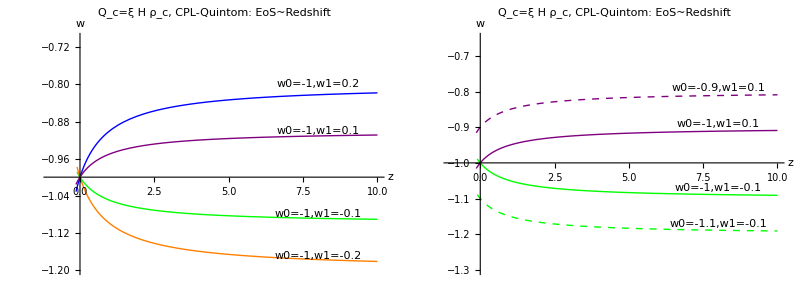

```mathematica
plEoSICCPLQuintomSum=Grid[{{Show[pltICCPLEoSfunc[-1,0.2,Blue],pltICCPLEoSfunc[-1,0.1,Purple],pltICCPLEoSfunc[-1,-0.1,Green],pltICCPLEoSfunc[-1,-0.2,Orange],PlotRange->{{-0.99,10},{-1.2,-0.7}},AxesOrigin->{0,-1},ImageSize->400,PlotLabel->"Q_c=ξ H ρ_c, CPL-Quintom: EoS~Redshift",Epilog->{Inset[Framed[Style["w0=-1,w1=0.2",10,Blue],Background->None,FrameStyle->None],{8,-0.80},{0,0}],Inset[Framed[Style["w0=-1,w1=0.1",10,Purple],Background->None,FrameStyle->None],{8,-0.9},{0,0}],Inset[Framed[Style["w0=-1,w1=-0.1",10,Green],Background->None,FrameStyle->None],{8,-1.08},{0,0}],Inset[Framed[Style["w0=-1,w1=-0.2",10,Orange],Background->None,FrameStyle->None],{8,-1.17},{0,0}]}],Show[pltICCPLEoSfunc[-1,0.1,Purple],pltICCPLEoSfunc[-0.9,0.1,{Purple,Dashed}],pltICCPLEoSfunc[-1,-0.1,Green],pltICCPLEoSfunc[-1.1,-0.1,{Green,Dashed}],PlotRange->{{-1,10},{-1.3,-0.65}},AxesOrigin->{0,-1},ImageSize->400,PlotLabel->"Q_c=ξ H ρ_c, CPL-Quintom: EoS~Redshift",Epilog->{Inset[Framed[Style["w0=-0.9,w1=0.1",10,Purple],Background->None,FrameStyle->None],{8,-0.79},{0,0}],Inset[Framed[Style["w0=-1,w1=0.1",10,Bold,Purple],Background->None,FrameStyle->None],{8,-0.89},{0,0}],Inset[Framed[Style["w0=-1,w1=-0.1",10,Bold,Green],Background->None,FrameStyle->None],{8,-1.07},{0,0}],Inset[Framed[Style["w0=-1.1,w1=-0.1",10,Green],Background->None,FrameStyle->None],{8,-1.17},{0,0}]}]}}]
```

“Purple line:(-1,0.1)─ Blue line: (-1,0.2) Green line:(-1,-0.1)\n─ Pink line:LCDM”
“Purple Dashed:(-0.9,0.1)  Green Dashed:(-1.1,0.1)”

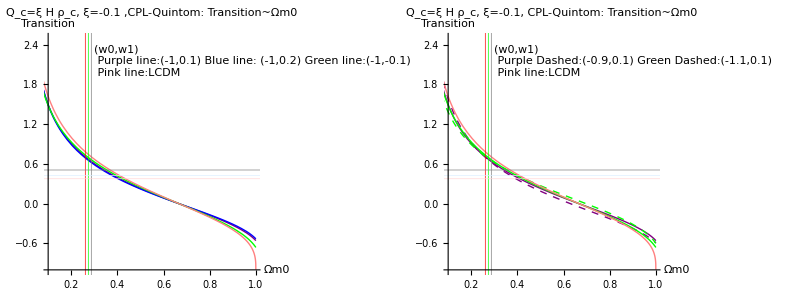

```mathematica
plztrICCPLQuintomSum=Grid[{{Show[{plztrICCPL[-0.1,-1,0.1,Purple,{0.1,1}],plztrICCPL[-0.1,-1,0.2,Blue,{0.1,1}],plztrICCPL[-0.1,-1,-0.1,Green,{0.1,1}],Plot[ztr[Ωm0ICCPL,1-Ωm0ICCPL],{Ωm0ICCPL,0,1},PlotRange->{{0.1,1},{-1,3}},PlotStyle->Pink,AxesOrigin->{0.1,-1}]},GridLines->{{{0.261,Red},{0.274,Green},{0.287,Gray}},{{0.376,LightRed},{0.426,LightBlue},{0.508,Gray}}},AxesOrigin->{0.1,-1},PlotRange->{{0.1,1},{-1,2.5}},Frame->False,AxesLabel->{"Ωm0","Transition"},PlotLabel->"Q_c=ξ H ρ_c, ξ=-0.1 ,CPL-Quintom: Transition~Ωm0",Epilog->Inset[Framed[Style["(w0,w1)\n Purple line:(-1,0.1) Blue line: (-1,0.2) Green line:(-1,-0.1)\n Pink line:LCDM",10],Background->None,FrameStyle->None],{0.3,2.4},{Left,Top}],ImageSize->400],Show[{plztrICCPL[-0.1,-1,0.1,Purple,{0.1,1}],plztrICCPL[-0.1,-0.9,0.1,{Purple,Dashed},{0.1,1}],plztrICCPL[-0.1,-1,-0.1,Green,{0.1,1}],plztrICCPL[-0.1,-1.1,-0.1,{Green,Dashed},{0.1,1}],Plot[ztr[Ωm0ICCPL,1-Ωm0ICCPL],{Ωm0ICCPL,0,1},PlotRange->{{0.1,1},{-1,3}},PlotStyle->Pink,AxesOrigin->{0.1,-1}]},GridLines->{{{0.261,Red},{0.274,Green},{0.287,Gray}},{{0.376,LightRed},{0.426,LightBlue},{0.508,Gray}}},AxesOrigin->{0.1,-1},PlotRange->{{0.1,1},{-1,2.5}},Frame->False,AxesLabel->{"Ωm0","Transition"},PlotLabel->"Q_c=ξ H ρ_c, ξ=-0.1, CPL-Quintom: Transition~Ωm0",Epilog->Inset[Framed[Style["(w0,w1)\n Purple Dashed:(-0.9,0.1) Green Dashed:(-1.1,0.1)\n Pink line:LCDM",10],Background->None,FrameStyle->None],{0.3,2.4},{Left,Top}],ImageSize->400]}}]//Quiet
```

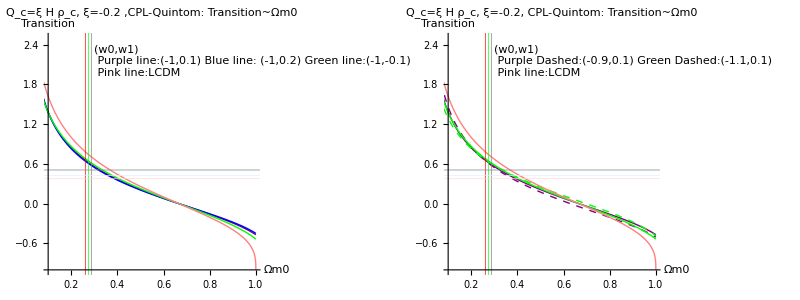

```mathematica
plztrICCPLQuintomSum02=Grid[{{Show[{plztrICCPL[-0.2,-1,0.1,Purple,{0.1,1}],plztrICCPL[-0.2,-1,0.2,Blue,{0.1,1}],plztrICCPL[-0.2,-1,-0.1,Green,{0.1,1}],Plot[ztr[Ωm0ICCPL,1-Ωm0ICCPL],{Ωm0ICCPL,0,1},PlotRange->{{0.1,1},{-1,3}},PlotStyle->Pink,AxesOrigin->{0.1,-1}]},GridLines->{{{0.261,Red},{0.274,Green},{0.287,Gray}},{{0.376,LightRed},{0.426,LightBlue},{0.508,Gray}}},AxesOrigin->{0.1,-1},PlotRange->{{0.1,1},{-1,2.5}},Frame->False,AxesLabel->{"Ωm0","Transition"},PlotLabel->"Q_c=ξ H ρ_c, ξ=-0.2 ,CPL-Quintom: Transition~Ωm0",Epilog->Inset[Framed[Style["(w0,w1)\n Purple line:(-1,0.1) Blue line: (-1,0.2) Green line:(-1,-0.1)\n Pink line:LCDM",10],Background->None,FrameStyle->None],{0.3,2.4},{Left,Top}],ImageSize->400],Show[{plztrICCPL[-0.2,-1,0.1,Purple,{0.1,1}],plztrICCPL[-0.2,-0.9,0.1,{Purple,Dashed},{0.1,1}],plztrICCPL[-0.2,-1,-0.1,Green,{0.1,1}],plztrICCPL[-0.2,-1.1,-0.1,{Green,Dashed},{0.1,1}],Plot[ztr[Ωm0ICCPL,1-Ωm0ICCPL],{Ωm0ICCPL,0,1},PlotRange->{{0.1,1},{-1,3}},PlotStyle->Pink,AxesOrigin->{0.1,-1}]},GridLines->{{{0.261,Red},{0.274,Green},{0.287,Gray}},{{0.376,LightRed},{0.426,LightBlue},{0.508,Gray}}},AxesOrigin->{0.1,-1},PlotRange->{{0.1,1},{-1,2.5}},Frame->False,AxesLabel->{"Ωm0","Transition"},PlotLabel->"Q_c=ξ H ρ_c, ξ=-0.2, CPL-Quintom: Transition~Ωm0",Epilog->Inset[Framed[Style["(w0,w1)\n Purple Dashed:(-0.9,0.1) Green Dashed:(-1.1,0.1)\n Pink line:LCDM",10],Background->None,FrameStyle->None],{0.3,2.4},{Left,Top}],ImageSize->400]}}]//Quiet
```

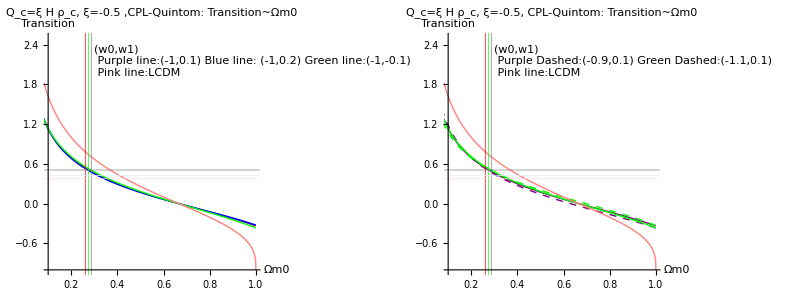

```mathematica
plztrICCPLQuintomSum05=Grid[{{Show[{plztrICCPL[-0.5,-1,0.1,Purple,{0.1,1}],plztrICCPL[-0.5,-1,0.2,Blue,{0.1,1}],plztrICCPL[-0.5,-1,-0.1,Green,{0.1,1}],Plot[ztr[Ωm0ICCPL,1-Ωm0ICCPL],{Ωm0ICCPL,0,1},PlotRange->{{0.1,1},{-1,3}},PlotStyle->Pink,AxesOrigin->{0.1,-1}]},GridLines->{{{0.261,Red},{0.274,Green},{0.287,Gray}},{{0.376,LightRed},{0.426,LightBlue},{0.508,Gray}}},AxesOrigin->{0.1,-1},PlotRange->{{0.1,1},{-1,2.5}},Frame->False,AxesLabel->{"Ωm0","Transition"},PlotLabel->"Q_c=ξ H ρ_c, ξ=-0.5 ,CPL-Quintom: Transition~Ωm0",Epilog->Inset[Framed[Style["(w0,w1)\n Purple line:(-1,0.1) Blue line: (-1,0.2) Green line:(-1,-0.1)\n Pink line:LCDM",10],Background->None,FrameStyle->None],{0.3,2.4},{Left,Top}],ImageSize->400],Show[{plztrICCPL[-0.5,-1,0.1,Purple,{0.1,1}],plztrICCPL[-0.5,-0.9,0.1,{Purple,Dashed},{0.1,1}],plztrICCPL[-0.5,-1,-0.1,Green,{0.1,1}],plztrICCPL[-0.5,-1.1,-0.1,{Green,Dashed},{0.1,1}],Plot[ztr[Ωm0ICCPL,1-Ωm0ICCPL],{Ωm0ICCPL,0,1},PlotRange->{{0.1,1},{-1,3}},PlotStyle->Pink,AxesOrigin->{0.1,-1}]},GridLines->{{{0.261,Red},{0.274,Green},{0.287,Gray}},{{0.376,LightRed},{0.426,LightBlue},{0.508,Gray}}},AxesOrigin->{0.1,-1},PlotRange->{{0.1,1},{-1,2.5}},Frame->False,AxesLabel->{"Ωm0","Transition"},PlotLabel->"Q_c=ξ H ρ_c, ξ=-0.5, CPL-Quintom: Transition~Ωm0",Epilog->Inset[Framed[Style["(w0,w1)\n Purple Dashed:(-0.9,0.1) Green Dashed:(-1.1,0.1)\n Pink line:LCDM",10],Background->None,FrameStyle->None],{0.3,2.4},{Left,Top}],ImageSize->400]}}]//Quiet
```

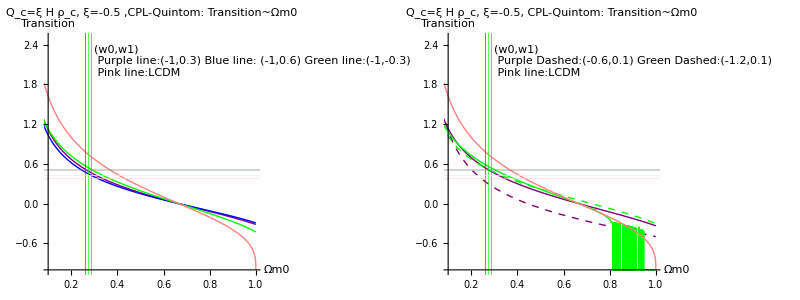

```mathematica
plztrICCPLQQTest5=Grid[{{Show[{plztrICCPL[-0.5,-1,0.3,Purple,{0.1,1}],plztrICCPL[-0.5,-1,0.6,Blue,{0.1,1}],plztrICCPL[-0.5,-1,-0.3,Green,{0.1,1}],Plot[ztr[Ωm0ICCPL,1-Ωm0ICCPL],{Ωm0ICCPL,0,1},PlotRange->{{0.1,1},{-1,3}},PlotStyle->Pink,AxesOrigin->{0.1,-1}]},GridLines->{{{0.261,Red},{0.274,Green},{0.287,Gray}},{{0.376,LightRed},{0.426,LightBlue},{0.508,Gray}}},AxesOrigin->{0.1,-1},PlotRange->{{0.1,1},{-1,2.5}},Frame->False,AxesLabel->{"Ωm0","Transition"},PlotLabel->"Q_c=ξ H ρ_c, ξ=-0.5 ,CPL-Quintom: Transition~Ωm0",Epilog->Inset[Framed[Style["(w0,w1)\n Purple line:(-1,0.3) Blue line: (-1,0.6) Green line:(-1,-0.3)\n Pink line:LCDM",10],Background->None,FrameStyle->None],{0.3,2.4},{Left,Top}],ImageSize->400],Show[{plztrICCPL[-0.5,-1,0.1,Purple,{0.1,1}],plztrICCPL[-0.5,-0.6,0.1,{Purple,Dashed},{0.1,1}],plztrICCPL[-0.5,-1,-0.8,Green,{0.1,1}],plztrICCPL[-0.5,-1.2,-0.1,{Green,Dashed},{0.1,1}],Plot[ztr[Ωm0ICCPL,1-Ωm0ICCPL],{Ωm0ICCPL,0,1},PlotRange->{{0.1,1},{-1,3}},PlotStyle->Pink,AxesOrigin->{0.1,-1}]},GridLines->{{{0.261,Red},{0.274,Green},{0.287,Gray}},{{0.376,LightRed},{0.426,LightBlue},{0.508,Gray}}},AxesOrigin->{0.1,-1},PlotRange->{{0.1,1},{-1,2.5}},Frame->False,AxesLabel->{"Ωm0","Transition"},PlotLabel->"Q_c=ξ H ρ_c, ξ=-0.5, CPL-Quintom: Transition~Ωm0",Epilog->Inset[Framed[Style["(w0,w1)\n Purple Dashed:(-0.6,0.1) Green Dashed:(-1.2,0.1)\n Pink line:LCDM",10],Background->None,FrameStyle->None],{0.3,2.4},{Left,Top}],ImageSize->400]}}]//Quiet
```

As for the effect of EoS, we can split it to w0 effect and w1 effect.

First construct the plot function.

```mathematica
(*
pltξvw0ICCPL[w1ICCPL_,w0ICCPLs_,w0ICCPLe_]:=Plot[{ξICCPLfc[w0ICCPL,w1ICCPL],ξICCPLf1[w0ICCPL,w1ICCPL],ξICCPLf2[w0ICCPL,w1ICCPL]},{w0ICCPL,w0ICCPLs,w0ICCPLe}]
*)
```

Choose the values from Reference 3. w0 = -1.087 ± 0.096,

```mathematica
ξvwExamICCPLQuintom={Block[{w0ICCPL=-1,w1ICCPL=-0.1},{{w0ICCPL,w1ICCPL},ξICCPLfc[w0ICCPL,w1ICCPL],ξICCPLf1[w0ICCPL,w1ICCPL],ξICCPLf2[w0ICCPL,w1ICCPL]}],Block[{w0ICCPL=-1,w1ICCPL=0},{{w0ICCPL,w1ICCPL},ξICCPLfc[w0ICCPL,w1ICCPL],ξICCPLf1[w0ICCPL,w1ICCPL],ξICCPLf2[w0ICCPL,w1ICCPL]}],Block[{w0ICCPL=-1,w1ICCPL=0.1},{{w0ICCPL,w1ICCPL},ξICCPLfc[w0ICCPL,w1ICCPL],ξICCPLf1[w0ICCPL,w1ICCPL],ξICCPLf2[w0ICCPL,w1ICCPL]}],Block[{w0ICCPL=-0.9,w1ICCPL=0.1},{{w0ICCPL,w1ICCPL},ξICCPLfc[w0ICCPL,w1ICCPL],ξICCPLf1[w0ICCPL,w1ICCPL],ξICCPLf2[w0ICCPL,w1ICCPL]}],Block[{w0ICCPL=-1.1,w1ICCPL=-0.1},{{w0ICCPL,w1ICCPL},ξICCPLfc[w0ICCPL,w1ICCPL],ξICCPLf1[w0ICCPL,w1ICCPL],ξICCPLf2[w0ICCPL,w1ICCPL]}]}
```

{{{-1,-0.1},-0.907284,-1.3096,-0.484861},{{-1,0},-0.877755,-1.27874,-0.457448},{{-1,0.1},-0.844859,-1.24477,-0.426298},{{-0.9,0.1},-0.785036,-1.17144,-0.383258},{{-1.1,-0.1},-0.910565,-1.3218,-0.477189}}

```mathematica
tabξvwExamICCPLQuintom=Grid[Prepend[Prepend[ξvwExamICCPLQuintom,{"{w0,w1}","Center","Lower","Upper"}],{"ξ results for Q_c=ξ H ρ_d, CPL,Quintom.",SpanFromLeft}],Frame->All,Background->{{LightGray,None},{LightGreen,LightGray,None}},Alignment->Center,ItemSize->8]
```

ξ results for Q_c=ξ H ρ_d, CPL,Quintom. |  |  | 
{w0,w1} | Center | Lower | Upper
{-1,-0.1} | -0.907284 | -1.3096 | -0.484861
{-1,0} | -0.877755 | -1.27874 | -0.457448
{-1,0.1} | -0.844859 | -1.24477 | -0.426298
{-0.9,0.1} | -0.785036 | -1.17144 | -0.383258
{-1.1,-0.1} | -0.910565 | -1.3218 | -0.477189

```mathematica
(*
pltξvwExamICCPL=Show[pltξvwICCPL[????????],GridLines->{{{ξvwExamICC[[1,1]],Directive[Gray,Dashed]},{ξvwExamICC[[2,1]],Directive[Gray,Dotted]},{ξvwExamICC[[3,1]],Directive[Gray,DotDashed]}},{{ξvwExamICC[[1,3]],Directive[Orange,Dashed]},{ξvwExamICC[[1,2]],Directive[Blue,Dashed]},{ξvwExamICC[[1,4]],Directive[Red,Dashed]},{ξvwExamICC[[2,3]],Directive[Orange,Dotted]},{ξvwExamICC[[2,2]],Directive[Blue,Dotted]},{ξvwExamICC[[2,4]],Directive[Red,Dotted]},{ξvwExamICC[[3,3]],Directive[Orange,DotDashed]},{ξvwExamICC[[3,2]],Directive[Blue,DotDashed]},{ξvwExamICC[[3,4]],Directive[Red,DotDashed]}}},Epilog->{Inset[Framed[Style["w = -1.087 ± 0.096",10],Background->LightBlue,FrameStyle->None],{-1.087,0.8},{0,Top}],Inset[Framed[Style["Orange:Ωm0=0.261;Transition=0.376\n Blue:Ωm0=0.274;Transition=0.426\n Red:Ωm0=0.287;Transition=0.508",11],Background->LightGreen,FrameStyle->None],{-1.95,0.84},{Left,Top}]},ImageSize->500]
*)
```

```mathematica
pltfitξICCPLfunc[w0ICCPL_,w1ICCPL_]:=Grid[{{numPlot["(",{ξICCPLf1[w0ICCPL,w1ICCPL],ξICCPLfc[w0ICCPL,w1ICCPL],ξICCPLf2[w0ICCPL,w1ICCPL]},")",{-2,1}]},{Plot[w0ICCPL+w1ICCPL temp/(temp+1),{temp,-0.9,10},Epilog->Inset[Framed[Style[{w0ICCPL,w1ICCPL},10],Background->LightYellow],{Center,Center},{Center,Center}]]}}];
```

```mathematica
pltfitξICCPLQuintomSum=Grid[{{pltfitξICCPLfunc[-1,0.1],pltfitξICCPLfunc[-1,0.2],pltfitξICCPLfunc[-1,-0.1]},{pltfitξICCPLfunc[-0.9,0.1],pltfitξICCPLfunc[-1.1,-0.1]}}]
```

-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- |

```mathematica
pltfitξvΩm0QuintomSum[w0ICCPL_,w1ICCPL_,color_,{Ωm0start_,Ωm0end_}]:=Plot[ξICCPLffunc[Ωm0ICCPL,1-Ωm0ICCPL,w0ICCPL,w1ICCPL,0.426],{Ωm0ICCPL,Ωm0start,Ωm0end},PlotStyle->color,AxesLabel->{"Ωm0","ξ"}];
```

Check sigularities. Why is that?

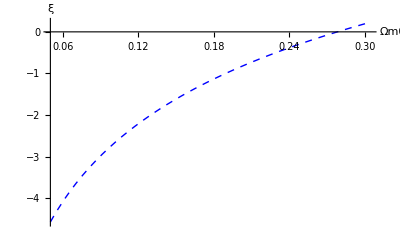

```mathematica
pltfitξvΩm0QuintomSum[-0.5,-0.2,{Blue,Dashed},{0.05,0.304}]//Quiet
```

```mathematica
ξICCPLffunc[0.46,1-0.46,-0.5,-0.2,0.426]//Quiet//Timing
```

{13.712,-94.3131}

```mathematica
ztrICCPL[0.46,1-0.46,ξICCPL,-0.5,-0.2]==0.426
```

Re[z/.FindRoot[(1+3 (-0.5-(0.2 z)/(1+z))) ΩdICCPL[0.54,0.46,-0.5,-0.2,ξICCPL,z]+ΩmICCPL[0.46,ξICCPL,z]==0,{z,3}]]==0.426

```mathematica
(1+3 (w0ICCPL+(w1ICCPL z)/(1+z))) ΩdICCPL[Ωd0ICCPL,Ωm0ICCPL,w0ICCPL,w1ICCPL,ξICCPL,z]+ΩmICCPL[Ωm0ICCPL,ξICCPL,z]==0//Simplify
```

(1+z)^(3-ξICCPL) Ωm0ICCPL+ⅇ^((3 w1ICCPL)/(1+z)) (1+z)^(3 (1+w0ICCPL+w1ICCPL)) (1+3 w0ICCPL+(3 w1ICCPL z)/(1+z)) (ⅇ^(-3 w1ICCPL) Ωd0ICCPL-ξICCPL Ωm0ICCPL ExpIntegralE[1-3 (w0ICCPL+w1ICCPL)-ξICCPL,3 w1ICCPL]+(1/(1+z))^(3 w0ICCPL+3 w1ICCPL+ξICCPL) ξICCPL Ωm0ICCPL ExpIntegralE[1-3 (w0ICCPL+w1ICCPL)-ξICCPL,(3 w1ICCPL)/(1+z)])==0

```mathematica
ztrICCPL[0.46,1-0.46,0,-0.5,x]
```

Re[z/.FindRoot[(1+3 (-0.5+(x z)/(1+z))) ΩdICCPL[0.54,0.46,-0.5,x,0,z]+ΩmICCPL[0.46,0,z]==0,{z,3}]]

```mathematica
FindRoot[(1+3 (-0.5+(-0.2 z)/(1+z))) ΩdICCPL[0.54,0.46,-0.5,-0.2,0,z]+ΩmICCPL[0.46,0,z]==0,{z,-0.9}]
```

{z→-1.}

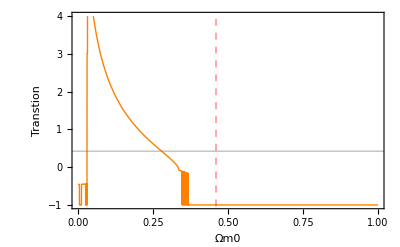
{2.979,-Graphics-}

```mathematica
Show[plztrICCPL[0,-0.5,-0.2,Orange,{0,1}],GridLines->{{{0.46,Directive[Red,Dashed]}},{{0.426,Gray}}}]//Quiet//Timing
```

```mathematica
ξICCPLffunc[0.2,1-0.2,-1,0.1,0.426]//Timing//Quiet
```

{0.484,-1.57483}

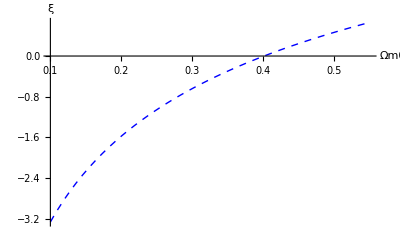
{47.159,-Graphics-}

```mathematica
pltfitξvΩm0QuintomSum[-1,0.1,{Blue,Dashed},{0.1,0.55}]//Quiet//Timing
```

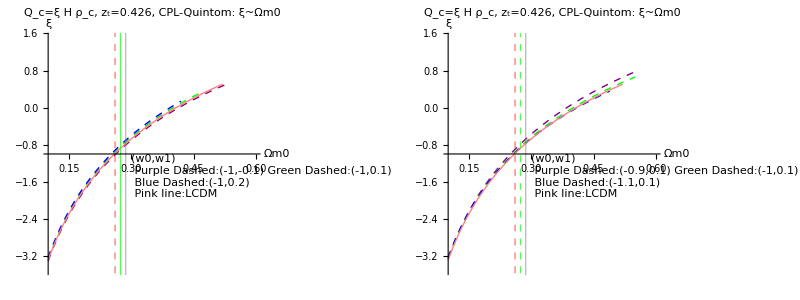

```mathematica
pltξvΩm0ICCPLQuintomSum=Grid[{{Show[pltfitξvΩm0QuintomSum[-1,-0.1,{Purple,Dashed},{0.1,0.538}],pltfitξvΩm0QuintomSum[-1,0.1,{Green,Dashed},{0.1,0.471}],pltfitξvΩm0QuintomSum[-1,0.2,{Blue,Dashed},{0.1,0.42}],pltfitξvΩm0QuintomSum[-1,0,Pink,{0.1,0.52}],GridLines->{{{0.261,Directive[Red,Dashed]},{0.274,Green},{0.287,Gray}},{}},AxesOrigin->{0.1,-1},PlotRange->{{0.1,0.6},{-3.5,1.5}},Frame->False,AxesLabel->{"Ωm0","ξ"},PlotLabel->"Q_c=ξ H ρ_c, z_t=0.426, CPL-Quintom: ξ~Ωm0",Epilog->Inset[Framed[Style["(w0,w1)\n Purple Dashed:(-1,-0.1) Green Dashed:(-1,0.1)\n Blue Dashed:(-1,0.2)\n Pink line:LCDM",10],Background->None,FrameStyle->None],{0.3,-1},{Left,Top}],ImageSize->400],Show[pltfitξvΩm0QuintomSum[-0.9,0.1,{Purple,Dashed},{0.1,0.55}],pltfitξvΩm0QuintomSum[-1,0.1,{Green,Dashed},{0.1,0.55}],pltfitξvΩm0QuintomSum[-1.1,0.1,{Blue,Dashed},{0.1,0.489}],pltfitξvΩm0QuintomSum[-1,0,Pink,{0.1,0.52}],GridLines->{{{0.261,Directive[Red,Dashed]},{0.274,Directive[Green,Dashed]},{0.287,Gray}},{}},AxesOrigin->{0.1,-1},PlotRange->{{0.1,0.6},{-3.5,1.5}},Frame->False,AxesLabel->{"Ωm0","ξ"},PlotLabel->"Q_c=ξ H ρ_c, z_t=0.426, CPL-Quintom: ξ~Ωm0",Epilog->Inset[Framed[Style["(w0,w1)\n Purple Dashed:(-0.9,0.1) Green Dashed:(-1,0.1)\n Blue Dashed:(-1.1,0.1)\n Pink line:LCDM",10],Background->None,FrameStyle->None],{0.3,-1},{Left,Top}],ImageSize->400]}}]//Quiet
```

```mathematica
(*
tabw0vw1ICCPLfull=Table[{ztrICCPL[0.274,1-0.274,0,w0ICCPLtemp,w1ICCPLtemp],ξICCPLffunc[0.274,1-0.274,w0ICCPLtemp,w1ICCPLtemp,0.426],w0ICCPLtemp,w1ICCPLtemp},{w0ICCPLtemp,-1.8,-0.5,0.05},{w1ICCPLtemp,-1,1,0.01}];//Quiet//Timing
*)
```

```mathematica
tabw0vw1ICCPL2=Table[{w0ICCPLtemp,eosICCPLw1/.FindRoot[{ξICCffunc[0.274,1-0.274-0,w0ICCPLtemp,eosICCPLw1]==0},{eosICCPLw1,-0.5}]},{w0ICCPLtemp,-1.8,-0.5,0.01}];//Quiet//Timing
```

{170.478,Null}

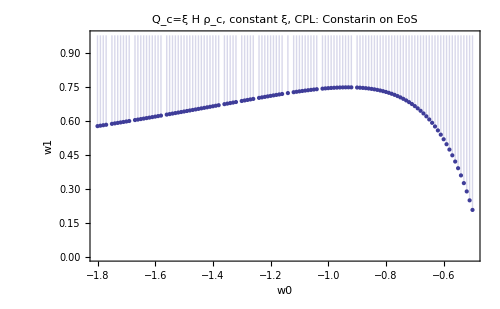

```mathematica
pltw0vw1ConsICCPL=ListPlot[tabw0vw1ICCPL2,FrameLabel->{"w0","w1"},Filling->Top,Frame->True,PlotLabel->"Q_c=ξ H ρ_c, constant ξ, CPL: Constarin on EoS",ImageSize->500]
```

```mathematica
(*
tabw0vw1ICCPL1=Table[{eosICCPLw0/.FindRoot[{ξICCPLffunc[0.274,1-0.274,eosICCPLw0,w1ICCPLtemp,0.426]==0},{eosICCPLw0,-0.5}],w1ICCPLtemp},{w1ICCPLtemp,-0.5,0.5,0.05}];//Quiet//Timing
*)
```

#### Quintessence

Choose some Quintessence parameters.
(-0.9,-0.05) (-0.8,-0.05)(-0.8,-0.1)

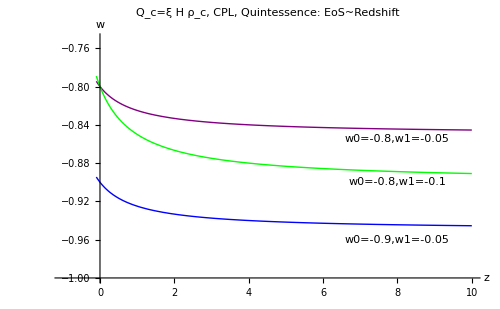

```mathematica
plEoSICCPLQuintessenceSum=Grid[{{Show[pltICCPLEoSfunc[-0.9,-0.05,Blue],pltICCPLEoSfunc[-0.8,-0.05,Purple],pltICCPLEoSfunc[-0.8,-0.1,Green],PlotRange->{{-0.99,10},{-1.0,-0.75}},AxesOrigin->{0,-1},Epilog->{Inset[Framed[Style["w0=-0.9,w1=-0.05",10,Blue],Background->None,FrameStyle->None],{8,-0.96},{0,0}],Inset[Framed[Style["w0=-0.8,w1=-0.05",10,Purple],Background->None,FrameStyle->None],{8,-0.855},{0,0}],Inset[Framed[Style["w0=-0.8,w1=-0.1",10,Green],Background->None,FrameStyle->None],{8,-0.9},{0,0}]},PlotLabel->"Q_c=ξ H ρ_c, CPL, Quintessence: EoS~Redshift",ImageSize->500]}}]
```

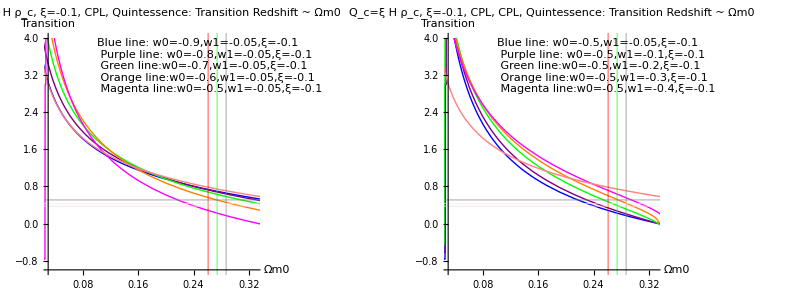

```mathematica
plztrICCPLQuintessenceSum=Grid[{{Show[{Plot[ztrICCPL[Ωm0ICCPL,1-Ωm0ICCPL,-0.1,-0.9,-0.05],{Ωm0ICCPL,0.01,1},PlotRange->{{0,1},{-1,4}},PlotStyle->Blue,AxesOrigin->{0,-1},PerformanceGoal->"Quality"],Plot[ztrICCPL[Ωm0ICCPL,1-Ωm0ICCPL,-0.1,-0.8,-0.05],{Ωm0ICCPL,0.01,1},PlotRange->{{0,1},{-1,4}},PlotStyle->Purple,AxesOrigin->{0,-1},PerformanceGoal->"Quality"],Plot[ztrICCPL[Ωm0ICCPL,1-Ωm0ICCPL,-0.1,-0.7,-0.05],{Ωm0ICCPL,0.01,0.94},PlotRange->{{0,1},{-1,4}},PlotStyle->Green,AxesOrigin->{0,-1},PerformanceGoal->"Quality"],Plot[ztrICCPL[Ωm0ICCPL,1-Ωm0ICCPL,-0.1,-0.6,-0.05],{Ωm0ICCPL,0.01,0.94},PlotRange->{{0,1},{-1,4}},PlotStyle->Orange,AxesOrigin->{0,-1},PerformanceGoal->"Quality"],Plot[ztrICCPL[Ωm0ICCPL,1-Ωm0ICCPL,-0.1,-0.5,-0.05],{Ωm0ICCPL,0.01,0.94},PlotRange->{{0,1},{-1,4}},PlotStyle->Magenta,AxesOrigin->{0,-1},PerformanceGoal->"Quality"],Plot[ztr[Ωm0ICCPL,1-Ωm0ICCPL],{Ωm0ICCPL,0,1},PlotRange->{{0.01,0.94},{-1,4}},PlotStyle->Pink,AxesOrigin->{0,-1}]},GridLines->{{{0.261,Red},{0.274,Green},{0.287,Gray}},{{0.376,LightRed},{0.426,LightBlue},{0.508,Gray}}},AxesOrigin->{0.03,-1},PlotRange->{{0.03,0.33},Automatic},Frame->False,AxesLabel->{"Ωm0","Transition"},Epilog->Inset[Framed[Style["Blue line: w0=-0.9,w1=-0.05,ξ=-0.1\n Purple line: w0=-0.8,w1=-0.05,ξ=-0.1\n Green line:w0=-0.7,w1=-0.05,ξ=-0.1\n Orange line:w0=-0.6,w1=-0.05,ξ=-0.1\n Magenta line:w0=-0.5,w1=-0.05,ξ=-0.1",10],Background->LightGreen,FrameStyle->None],{0.1,4},{Left,Top}],PlotLabel->"Q_c=ξ H ρ_c, ξ=-0.1, CPL, Quintessence: Transition Redshift ~ Ωm0",ImageSize->400],Show[{Plot[ztrICCPL[Ωm0ICCPL,1-Ωm0ICCPL,-0.1,-0.5,-0.05],{Ωm0ICCPL,0.01,1},PlotRange->{{0,1},{-1,4}},PlotStyle->Blue,AxesOrigin->{0,-1},PerformanceGoal->"Quality"],Plot[ztrICCPL[Ωm0ICCPL,1-Ωm0ICCPL,-0.1,-0.5,-0.1],{Ωm0ICCPL,0.01,1},PlotRange->{{0,1},{-1,4}},PlotStyle->Purple,AxesOrigin->{0,-1},PerformanceGoal->"Quality"],Plot[ztrICCPL[Ωm0ICCPL,1-Ωm0ICCPL,-0.1,-0.5,-0.2],{Ωm0ICCPL,0.01,0.94},PlotRange->{{0,1},{-1,4}},PlotStyle->Green,AxesOrigin->{0,-1},PerformanceGoal->"Quality"],Plot[ztrICCPL[Ωm0ICCPL,1-Ωm0ICCPL,-0.1,-0.5,-0.3],{Ωm0ICCPL,0.01,0.94},PlotRange->{{0,1},{-1,4}},PlotStyle->Orange,AxesOrigin->{0,-1},PerformanceGoal->"Quality"],Plot[ztrICCPL[Ωm0ICCPL,1-Ωm0ICCPL,-0.1,-0.5,-0.4],{Ωm0ICCPL,0.01,0.94},PlotRange->{{0,1},{-1,4}},PlotStyle->Magenta,AxesOrigin->{0,-1},PerformanceGoal->"Quality"],Plot[ztr[Ωm0ICCPL,1-Ωm0ICCPL],{Ωm0ICCPL,0,1},PlotRange->{{0.01,0.94},{-1,4}},PlotStyle->Pink,AxesOrigin->{0,-1}]},GridLines->{{{0.261,Red},{0.274,Green},{0.287,Gray}},{{0.376,LightRed},{0.426,LightBlue},{0.508,Gray}}},AxesOrigin->{0.03,-1},PlotRange->{{0.03,0.33},Automatic},Frame->False,AxesLabel->{"Ωm0","Transition"},Epilog->Inset[Framed[Style["Blue line: w0=-0.5,w1=-0.05,ξ=-0.1\n Purple line: w0=-0.5,w1=-0.1,ξ=-0.1\n Green line:w0=-0.5,w1=-0.2,ξ=-0.1\n Orange line:w0=-0.5,w1=-0.3,ξ=-0.1\n Magenta line:w0=-0.5,w1=-0.4,ξ=-0.1",10],Background->LightGreen,FrameStyle->None],{0.1,4},{Left,Top}],PlotLabel->"Q_c=ξ H ρ_c, ξ=-0.1, CPL, CPL, Quintessence: Transition Redshift ~ Ωm0",ImageSize->400]}}]
```

As for the effect of EoS, we can split it to w0 effect and w1 effect.

Choose some values of w0 and w1 causually.

```mathematica
ξvwExamICCPLQuintessence={Block[{w0ICCPL=-0.9,w1ICCPL=-0.05},{{w0ICCPL,w1ICCPL},ξICCPLfc[w0ICCPL,w1ICCPL],ξICCPLf1[w0ICCPL,w1ICCPL],ξICCPLf2[w0ICCPL,w1ICCPL]}],Block[{w0ICCPL=-0.8,w1ICCPL=-0.05},{{w0ICCPL,w1ICCPL},ξICCPLfc[w0ICCPL,w1ICCPL],ξICCPLf1[w0ICCPL,w1ICCPL],ξICCPLf2[w0ICCPL,w1ICCPL]}],Block[{w0ICCPL=-0.8,w1ICCPL=-0.1},{{w0ICCPL,w1ICCPL},ξICCPLfc[w0ICCPL,w1ICCPL],ξICCPLf1[w0ICCPL,w1ICCPL],ξICCPLf2[w0ICCPL,w1ICCPL]}]}
```

{{{-0.9,-0.05},-0.853591,-1.24197,-0.448612},{{-0.8,-0.05},-0.765204,-1.1341,-0.384235},{{-0.8,-0.1},-0.794865,-1.16484,-0.412217}}

```mathematica
tabξvwExamICCPLQuintessence=Grid[Prepend[Prepend[ξvwExamICCPLQuintessence,{"{w0,w1}","Center","Lower","Upper"}],{"ξ results for Q_c=ξ H ρ_d, CPL,Quintessence.",SpanFromLeft}],Frame->All,Background->{{LightGray,None},{LightGreen,LightGray,None}},Alignment->Center,ItemSize->8]
```

ξ results for Q_c=ξ H ρ_d, CPL,Quintessence. |  |  | 
{w0,w1} | Center | Lower | Upper
{-0.9,-0.05} | -0.853591 | -1.24197 | -0.448612
{-0.8,-0.05} | -0.765204 | -1.1341 | -0.384235
{-0.8,-0.1} | -0.794865 | -1.16484 | -0.412217

```mathematica
pltfitξICCPLQuintessenceSum=Grid[{{pltfitξICCPLfunc[-0.9,-0.05],pltfitξICCPLfunc[-0.8,-0.05],pltfitξICCPLfunc[-0.8,-0.1]}}]
```

-Graphics- | -Graphics- | -Graphics-

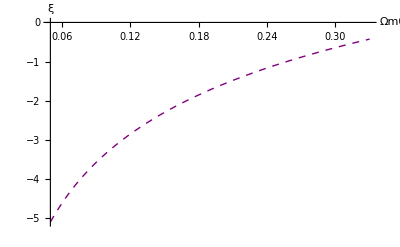
{37.051,-Graphics-}

```mathematica
pltfitξvΩm0QuintomSum[-0.9,-0.05,{Purple,Dashed},{0.05,0.33}]//Timing//Quiet
```

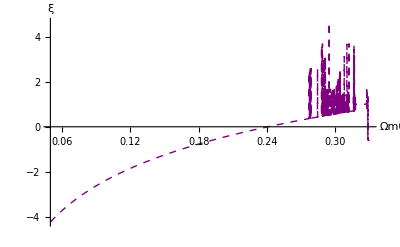
{378.646,-Graphics-}

```mathematica
pltfitξvΩm0QuintomSum[-0.5,-0.05,{Purple,Dashed},{0.05,0.33}]//Timing//Quiet
```

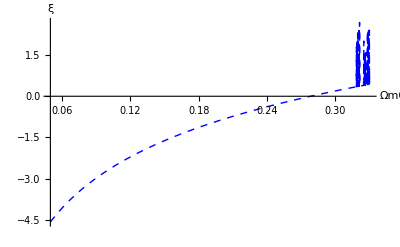
{111.12,-Graphics-}

```mathematica
pltfitξvΩm0QuintomSum[-0.5,-0.2,{Blue,Dashed},{0.05,0.33}]//Timing//Quiet
```

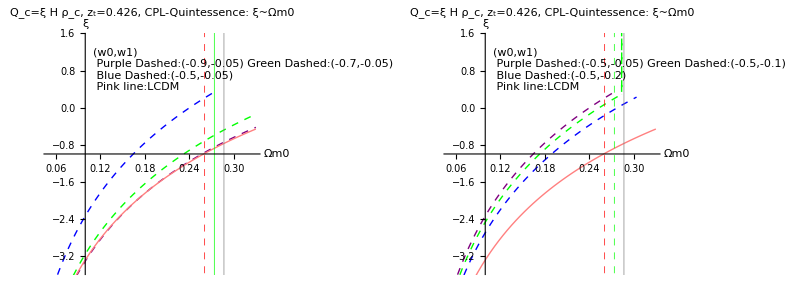

```mathematica
pltξvΩm0ICCPLQuintessenceSum=Grid[{{Show[pltfitξvΩm0QuintomSum[-0.9,-0.05,{Purple,Dashed},{0.05,0.33}],pltfitξvΩm0QuintomSum[-0.7,-0.05,{Green,Dashed},{0.05,0.33}],pltfitξvΩm0QuintomSum[-0.5,-0.05,{Blue,Dashed},{0.05,0.276}],pltfitξvΩm0QuintomSum[-1,0,Pink,{0.05,0.33}],GridLines->{{{0.261,Directive[Red,Dashed]},{0.274,Green},{0.287,Gray}},{}},AxesOrigin->{0.1,-1},PlotRange->{{0.05,0.33},{-3.5,1.5}},Frame->False,AxesLabel->{"Ωm0","ξ"},PlotLabel->"Q_c=ξ H ρ_c, z_t=0.426, CPL-Quintessence: ξ~Ωm0",Epilog->Inset[Framed[Style["(w0,w1)\n Purple Dashed:(-0.9,-0.05) Green Dashed:(-0.7,-0.05)\n Blue Dashed:(-0.5,-0.05)\n Pink line:LCDM",10],Background->None,FrameStyle->None],{0.11,1.3},{Left,Top}],ImageSize->400],Show[pltfitξvΩm0QuintomSum[-0.5,-0.05,{Purple,Dashed},{0.05,0.276}],pltfitξvΩm0QuintomSum[-0.5,-0.1,{Green,Dashed},{0.05,0.284}],pltfitξvΩm0QuintomSum[-0.5,-0.2,{Blue,Dashed},{0.05,0.304}],pltfitξvΩm0QuintomSum[-1,0,Pink,{0.05,0.33}],GridLines->{{{0.261,Directive[Red,Dashed]},{0.274,Directive[Green,Dashed]},{0.287,Gray}},{}},AxesOrigin->{0.1,-1},PlotRange->{{0.05,0.33},{-3.5,1.5}},Frame->False,AxesLabel->{"Ωm0","ξ"},PlotLabel->"Q_c=ξ H ρ_c, z_t=0.426, CPL-Quintessence: ξ~Ωm0",Epilog->Inset[Framed[Style["(w0,w1)\n Purple Dashed:(-0.5,-0.05) Green Dashed:(-0.5,-0.1)\n Blue Dashed:(-0.5,-0.2)\n Pink line:LCDM",10],Background->None,FrameStyle->None],{0.11,1.3},{Left,Top}],ImageSize->400]}}]//Quiet
```

#### Phantom

Some parameters that give us a phantom mode
(-1.1,0.05) (-1.2,0.05) (-1.2,0.1)

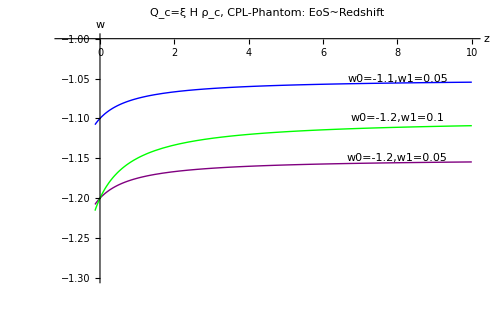

```mathematica
plEoSICCPLPhantomSum=Grid[{{Show[pltICCPLEoSfunc[-1.1,0.05,Blue],pltICCPLEoSfunc[-1.2,0.05,Purple],pltICCPLEoSfunc[-1.2,0.1,Green],PlotRange->{{-0.99,10},{-1.3,-1}},AxesOrigin->{0,-1},Epilog->{Inset[Framed[Style["w0=-1.1,w1=0.05",10,Blue],Background->None,FrameStyle->None],{8,-1.05},{0,0}],Inset[Framed[Style["w0=-1.2,w1=0.05",10,Purple],Background->None,FrameStyle->None],{8,-1.15},{0,0}],Inset[Framed[Style["w0=-1.2,w1=0.1",10,Green],Background->None,FrameStyle->None],{8,-1.1},{0,0}]},PlotLabel->"Q_c=ξ H ρ_c, CPL-Phantom: EoS~Redshift",ImageSize->500]}}]
```

```mathematica
plztrICCPLPhantomSum=Grid[{{Show[{plztrICCPL[-0.1,-1.1,0.05,Blue,{0,1}],plztrICCPL[-0.1,-1.2,0.05,Purple,{0,1}],plztrICCPL[-0.1,-1.2,0.1,Green,{0,1}],Plot[ztr[Ωm0ICCPL,1-Ωm0ICCPL],{Ωm0ICCPL,0,1},PlotRange->{{0,1},{-1,4}},PlotStyle->Pink,AxesOrigin->{0,-1}]},Graphics[{Gray,Rectangle[Scaled[{0.261,.2752}],Scaled[{0.287,.3016}]]},Frame->True],AxesOrigin->{0,-1},Frame->False,AxesLabel->{"Ωm0","Transition"},Epilog->Inset[Framed[Style["Blue line: w0=-1.1,w1=0.05,ξ=-0.1\n Purple line: w0=-1.2,w1=0.05,ξ=-0.1\n Green line:w0=-1.2,w1=0.1,ξ=-0.1",10],Background->LightGreen,FrameStyle->None],{0.35,3.5},{0,0}],PlotLabel->"Q_c=ξ H ρ_c, CPL-Phantom: Transition ~ Ωm0",ImageSize->500]}}]
```

-Graphics-

As for the effect of EoS, we can split it to w0 effect and w1 effect.

Choose some values of w0 and w1 causually.

```mathematica
ξvwExamICCPLPhantom={Block[{w0ICCPL=-1.1,w1ICCPL=0.05},{{w0ICCPL,w1ICCPL},ξICCPLfc[w0ICCPL,w1ICCPL],ξICCPLf1[w0ICCPL,w1ICCPL],ξICCPLf2[w0ICCPL,w1ICCPL]}],Block[{w0ICCPL=-1.2,w1ICCPL=0.05},{{w0ICCPL,w1ICCPL},ξICCPLfc[w0ICCPL,w1ICCPL],ξICCPLf1[w0ICCPL,w1ICCPL],ξICCPLf2[w0ICCPL,w1ICCPL]}],Block[{w0ICCPL=-1.2,w1ICCPL=0.1},{{w0ICCPL,w1ICCPL},ξICCPLfc[w0ICCPL,w1ICCPL],ξICCPLf1[w0ICCPL,w1ICCPL],ξICCPLf2[w0ICCPL,w1ICCPL]}]}
```

{{{-1.1,0.05},-0.878139,-1.28773,-0.447379},{{-1.2,0.05},-0.870255,-1.28596,-0.431951},{{-1.2,0.1},-0.861665,-1.27697,-0.424022}}

```mathematica
tabξvwExamICCPLPhantom=Grid[Prepend[Prepend[ξvwExamICCPLPhantom,{"{w0,w1}","Center","Lower","Upper"}],{"ξ results for Q_c=ξ H ρ_d, CPL,Phantom.",SpanFromLeft}],Frame->All,Background->{{LightGray,None},{LightGreen,LightGray,None}},Alignment->Center,ItemSize->8]
```

ξ results for Q_c=ξ H ρ_d, CPL,Phantom. |  |  | 
{w0,w1} | Center | Lower | Upper
{-1.1,0.05} | -0.878139 | -1.28773 | -0.447379
{-1.2,0.05} | -0.870255 | -1.28596 | -0.431951
{-1.2,0.1} | -0.861665 | -1.27697 | -0.424022

```mathematica
pltfitξICCPLPhantomSum=Grid[{{pltfitξICCPLfunc[-1.1,0.05],pltfitξICCPLfunc[-1.2,0.05],pltfitξICCPLfunc[-1.2,0.1]}}]
```

-Graphics- | -Graphics- | -Graphics-

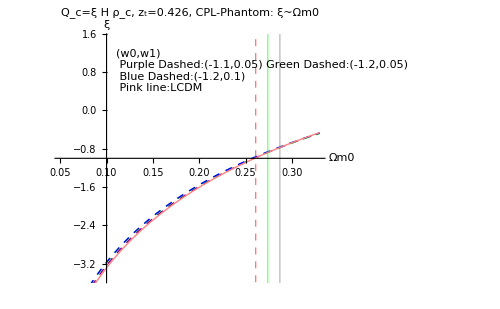

```mathematica
pltξvΩm0ICCPLPhantomSum=Show[pltfitξvΩm0QuintomSum[-1.1,0.05,{Purple,Dashed},{0.05,0.33}],pltfitξvΩm0QuintomSum[-1.2,0.05,{Green,Dashed},{0.05,0.33}],pltfitξvΩm0QuintomSum[-1.2,0.1,{Blue,Dashed},{0.05,0.33}],pltfitξvΩm0QuintomSum[-1,0,Pink,{0.05,0.33}],GridLines->{{{0.261,Directive[Red,Dashed]},{0.274,Green},{0.287,Gray}},{}},AxesOrigin->{0.1,-1},PlotRange->{{0.05,0.33},{-3.5,1.5}},Frame->False,AxesLabel->{"Ωm0","ξ"},PlotLabel->"Q_c=ξ H ρ_c, z_t=0.426, CPL-Phantom: ξ~Ωm0",Epilog->Inset[Framed[Style["(w0,w1)\n Purple Dashed:(-1.1,0.05) Green Dashed:(-1.2,0.05)\n Blue Dashed:(-1.2,0.1)\n Pink line:LCDM",10],Background->None,FrameStyle->None],{0.11,1.3},{Left,Top}],ImageSize->500]//Quiet
```

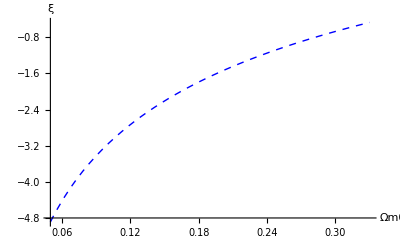
{37.628,-Graphics-}

```mathematica
pltfitξvΩm0QuintomSum[-1.2,0.1,{Blue,Dashed},{0.05,0.33}]//Timing//Quiet
```

### Take the form Q_c=ξ H ρ_d. I2 model

Hubble function without curvature

```mathematica
hubbleI2CC[H0_,Ωd0_,Ωm0_,w_,ξ_,z_]:=H0 √(Ωm+Ωd);
```

Conventions:
parameters : H0, Ωm0, Ωd0, w, ξ, z.

### Constant ξ + Constant w. I2CC model

#### Definations

Fraction energy density

```mathematica
ΩmI2CC[Ωm0I2CC_,Ωd0I2CC_,wI2CC_,ξI2CC_,z_]:=(Ωm0I2CC +ξI2CC/(ξI2CC+3wI2CC))(1+z)^3+-ξI2CC/(ξI2CC+3wI2CC)ΩdI2CC[Ωd0I2CC,wI2CC,ξI2CC,z]
```

```mathematica
ΩdI2CC[Ωd0I2CC_,wI2CC_,ξI2CC_,z_]:=Ωd0I2CC (1+z)^(3(1+wI2CC)+ξI2CC)
```

Hubble function

```mathematica
hubbleI2CC[H0I2CC_,Ωm0I2CC_,Ωd0I2CC_,wI2CC_,ξI2CC_,z_]=H0I2CC √(ΩmI2CC[Ωm0I2CC,Ωd0I2CC,wI2CC,ξI2CC,z]+ΩdI2CC[Ωd0I2CC,wI2CC,ξI2CC,z])
```

H0I2CC √((1+z)^(3 (1+wI2CC)+ξI2CC) Ωd0I2CC-((1+z)^(3 (1+wI2CC)+ξI2CC) ξI2CC Ωd0I2CC)/(3 wI2CC+ξI2CC)+(1+z)^3 (ξI2CC/(3 wI2CC+ξI2CC)+Ωm0I2CC))

Deceleration parameter

```mathematica
qI2CC[H0I2CC_,Ωm0I2CC_,Ωd0I2CC_,wI2CC_,ξI2CC_,z_]=-1+(1+z)/hubbleI2CC[H0I2CC,Ωm0I2CC,Ωd0I2CC,wI2CC,ξI2CC,z] D[hubbleI2CC[H0I2CC,Ωm0I2CC,Ωd0I2CC,wI2CC,ξI2CC,z],z];
```

```mathematica
qI2CC[H0I2CC,Ωm0I2CC,Ωd0I2CC,wI2CC,ξI2CC,z]//FullSimplify
```

(ξI2CC+3 wI2CC (1+z)^(3 wI2CC+ξI2CC) (1+3 wI2CC+ξI2CC) Ωd0I2CC+3 wI2CC Ωm0I2CC+ξI2CC Ωm0I2CC)/(2 (ξI2CC (1+Ωm0I2CC)+3 wI2CC ((1+z)^(3 wI2CC+ξI2CC) Ωd0I2CC+Ωm0I2CC)))

```mathematica
Limit[qI2CC[H0I2CC,Ωm0I2CC,Ωd0I2CC,wI2CC,ξI2CC,z]//FullSimplify,z->Infinity,Assumptions->(3 wI2CC+ξI2CC)<0]
```

1/2

At z-> Infinity limit, deceleration parameter→ 1/2, with 3 wICC+ξICC<0. This is different from LCDM model.

#### Plots, showcase, manipulate toys

```mathematica
pldecI2CC[Ωm0I2CC_,wI2CC_,ξI2CC_,color_]:=Plot[qI2CC[H0w,Ωm0I2CC,1-Ωm0I2CC,wI2CC,ξI2CC,z],{z,-1,10},PlotRange->{{-1.05,10},{-1.05,1}},PlotStyle->color,AxesOrigin->{-1,0},AxesLabel->{z,q}];
```

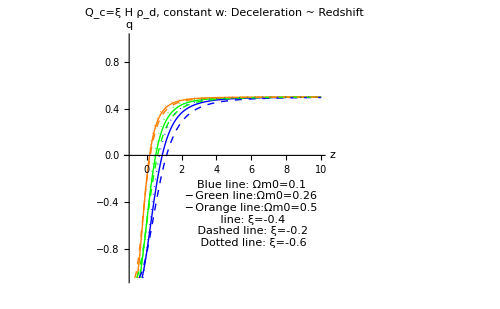

```mathematica
pldecI2CCShowSum=Show[{pldecI2CC[0.1,-1,-0.4,Blue],pldecI2CC[0.26,-1,-0.4,Green],pldecI2CC[0.5,-1,-0.4,Orange],pldecI2CC[0.1,-1,-0.2,Directive[Blue,Dashed]],pldecI2CC[0.26,-1,-0.2,Directive[Green,Dashed]],pldecI2CC[0.5,-1,-0.2,Directive[Orange,Dashed]],pldecI2CC[0.1,-1,-0.6,Directive[Blue,Dotted]],pldecI2CC[0.26,-1,-0.6,Directive[Green,Dotted]],pldecI2CC[0.5,-1,-0.6,Directive[Orange,Dotted]]},Epilog->Inset[Framed[Style["Blue line: Ωm0=0.1\n─ Green line:Ωm0=0.26\n─ Orange line:Ωm0=0.5\n line: ξ=-0.4\n Dashed line: ξ=-0.2\n Dotted line: ξ=-0.6",10],Background->LightGreen,FrameStyle->None],{6,-0.5}],PlotLabel->"Q_c=ξ H ρ_d, constant w: Deceleration ~ Redshift",ImageSize->500]
```

z->Infinity is a degenerate limit. For constant ξ and constant w models, this limit is determined by the interaction strength ξ . This might be useful if more complicated models are investigated and no large deviations are shown. [Nota]

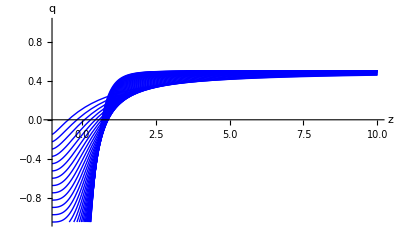
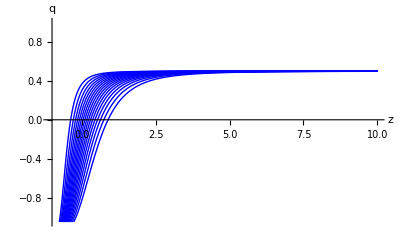
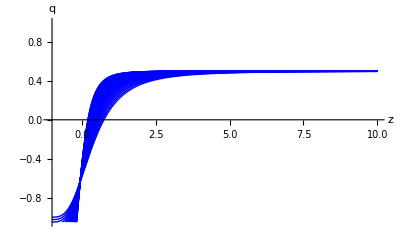
Varying EoS | Varying Ωm0 | Varying ξ
-Graphics- | -Graphics- | -Graphics-

```mathematica
varyingI2CCShowSum=Grid[{{"Varying EoS","Varying Ωm0","Varying ξ"},Table[{Show[Table[pldecI2CC[0.1,wI2CC,-0.4,Blue],{wI2CC,-2,-0.3,0.05}]],Show[Table[pldecI2CC[Ωm0I2CC,-1,-0.4,Blue],{Ωm0I2CC,0.1,0.9,0.05}]],Show[Table[pldecI2CC[0.27,-1,ξI2CC,Blue],{ξI2CC,-2,0,0.05}]]}]},Frame->All]
```

Use movable slides to check how do the parameters affect the deceleration parameter. Just a toy.

```mathematica
pldecI2CCManSum=Manipulate[Show[{pldecI2CC[Ωm0I2CC,wI2CC,ξI2CC,Orange],pldec[Ωm0I2CC,{Pink,Thick}]},PlotLabel->"Q_c=ξ H ρ_d, constant w: Deceleration ~ Redshift"],{{Ωm0I2CC,0.26,"Matter Fraction"},0,1,Appearance->"Open"},{{ξI2CC,-0.4,"Interaction"},-1,0,Appearance->"Open"},{{wI2CC,-1,"Equation of State"},-1.5,-0.5,Appearance->"Open"},Delimiter,Style["Pink is the deceleration parameter for LCDM.",Medium],Style["Orange is for interacting model with Q_c=ξ H ρ_d",Medium],ControlPlacement->{Right,Right,Right},SaveDefinitions->True]
```

#### Transition redshift definations and equations.

Find out the expression for transition redshift

```mathematica
ΩmI2CC[Ωm0I2CC_,Ωd0I2CC_,wI2CC_,ξI2CC_,z_]:=(Ωm0I2CC +ξI2CC/(ξI2CC+3wI2CC))(1+z)^3+-ξI2CC/(ξI2CC+3wI2CC)ΩdI2CC[Ωd0I2CC,wI2CC,ξI2CC,z]
```

```mathematica
ΩdI2CC[Ωd0I2CC_,wI2CC_,ξI2CC_,z_]:=Ωd0I2CC (1+z)^(3(1+wI2CC)+ξI2CC)
```

```mathematica
(3wI2CC+1)ΩdI2CC[Ωd0I2CC,wI2CC,ξI2CC,z]+ΩmI2CC[Ωm0I2CC,Ωd0I2CC,wI2CC,ξI2CC,z]==0//Simplify
```

1/(3 wI2CC+ξI2CC)(1+z) (ξI2CC (1+3 wI2CC (1+z)^(3 wI2CC+ξI2CC) Ωd0I2CC+Ωm0I2CC)+3 wI2CC ((1+3 wI2CC) (1+z)^(3 wI2CC+ξI2CC) Ωd0I2CC+Ωm0I2CC))==0

```mathematica
ztrI2CC[Ωm0I2CC_,Ωd0I2CC_,wI2CC_,ξI2CC_]=-1+(((3wI2CC+ξI2CC)Ωm0I2CC+ξI2CC Ωd0I2CC)/(-3wI2CC(3wI2CC+ξI2CC+1)Ωd0I2CC))^(1/(3wI2CC+ξI2CC))
```

-1+3^(-1/(3 wI2CC+ξI2CC)) (-(ξI2CC Ωd0I2CC+(3 wI2CC+ξI2CC) Ωm0I2CC)/(wI2CC (1+3 wI2CC+ξI2CC) Ωd0I2CC))^(1/(3 wI2CC+ξI2CC))

```mathematica
ztrI2CC[0.27,0.73,-1,-0.4]
```

0.540312

The first solution is trivil. So the second one is taken.

Define rICC=Ωm0ICC/Ωd0ICC

```mathematica
ztrrI2CC[rI2CC_,wI2CC_,ξI2CC_]=-1+(((3wI2CC+ξI2CC)rI2CC+ξI2CC)/(-3wI2CC(3wI2CC+ξI2CC+1)))^(1/(3 wI2CC+ξI2CC));
```

#### Visualiztion of transition redshift

Check the behavior of this transition redshift.

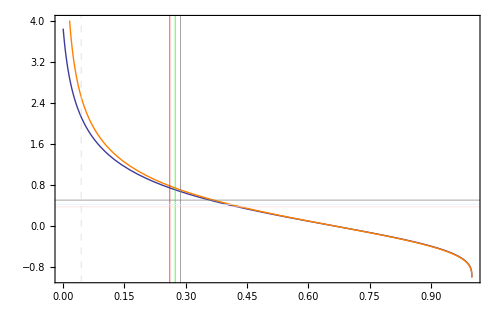

```mathematica
pldecrI2CC=Plot[{ztrI2CC[Ωm0I2CC,1-Ωm0I2CC,-1,-0.05],ztr[Ωm0I2CC,1-Ωm0I2CC]},{Ωm0I2CC,0,1},PlotRange->{{0,1},{-1,4}},PlotStyle->{Thick,Orange},AxesOrigin->{0,-1},Frame->True,GridLines->{{{0.044,Dashed},{0.261,Red},{0.274,Green},{0.287,Gray}},{{0.376,LightRed},{0.426,LightBlue},{0.508,Gray}}},PlotLegend->{"Q=-0.05 H ρ_c","LCDM"},LegendPosition->{0.0,-0.05},LegendShadow->None,ImageSize->500]
```

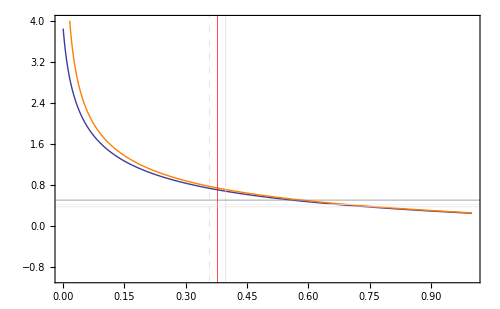

```mathematica
pldecrrI2CC=Plot[{ztrrI2CC[rI2CC,-1,-0.05],ztrr[rI2CC]},{rI2CC,0,1},PlotRange->{{0,1},{-1,4}},PlotStyle->{Thick,Orange},AxesOrigin->{0,-1},Frame->True,GridLines->{{{0.358,Dashed},{0.378,Directive[Red]},0.398},{{0.376,LightRed},{0.426,LightBlue},{0.508,Gray}}},PlotLegend->{"Q=-0.05 H ρ_c","LCDM"},LegendPosition->{0.0,-0.05},LegendShadow->None,ImageSize->500]
```

```mathematica
plztrI2CC[wI2CC_,ξI2CC_,color_]:=Plot[ztrI2CC[Ωm0I2CC,1-Ωm0I2CC,wI2CC,ξI2CC],{Ωm0I2CC,0,1},PlotRange->{{0,1},{-1,4}},PlotStyle->color,AxesOrigin->{0,-1},AxesLabel->{"Ωm0","z_t"}];
```

The following figure:

Orange for w=-1
Blue for w=-0.9

line: ξ=0.2
Dashed: ξ=0.1
Dotted: ξ=-0.1
DotDashed: ξ=-0.2

Pink line:w=1, ξ=0

```mathematica
plztrvsΩm0I2CCSum=Grid[{{Show[{plztrI2CC[-1,0.2,Orange],plztrI2CC[-1,0.1,{Orange,Dashed}],plztrI2CC[-1,-0.1,{Orange,Dotted}],plztrI2CC[-1,-0.2,{Orange,DotDashed}],Plot[ztr[Ωm0I2CC,1-Ωm0I2CC],{Ωm0I2CC,0,1},PlotRange->{{0,1},{-1,4}},PlotStyle->Pink,AxesOrigin->{0,-1}]},Graphics[{Gray,Rectangle[Scaled[{0.261,.2752}],Scaled[{0.287,.3016}]]},Frame->True],FrameLabel->{"Ωm0","Transition"},GridLines->{{},{{0,Dashed}}},PlotLabel->"Q_c=ξ H ρ_d, constant w: Transition ~ Ωm0",ImageSize->400],
Show[{plztrI2CC[-0.7,0.2,Blue],plztrI2CC[-0.7,0.1,{Blue,Dashed}],plztrI2CC[-0.7,-0.1,{Blue,Dotted}],plztrI2CC[-0.7,-0.2,{Blue,DotDashed}],Plot[ztr[Ωm0I2CC,1-Ωm0I2CC],{Ωm0I2CC,0,1},PlotRange->{{0,1},{-1,4}},PlotStyle->Pink,AxesOrigin->{0,-1}]},Graphics[{Gray,Rectangle[Scaled[{0.261,.2752}],Scaled[{0.287,.3016}]]},Frame->True],FrameLabel->{"Ωm0","Transition"},GridLines->{{},{{0,Dashed}}},PlotLabel->"Q_c=ξ H ρ_d, constant w: Transition ~ Ωm0",ImageSize->400]
}}]
```

-Graphics-

```mathematica
plztrI2CCManSum=Manipulate[Show[{plztrI2CC[wI2CC,ξI2CC,Orange],Plot[ztr[Ωm0I2CC,1-Ωm0I2CC],{Ωm0I2CC,0,1},PlotRange->{{0,1},{-1,4}},PlotStyle->Pink,AxesOrigin->{0,-1}]},Graphics[{Gray,Rectangle[Scaled[{0.261,.2752}],Scaled[{0.287,.3016}]]},Frame->True],FrameLabel->{"Ωm0","Transition"},GridLines->{{},{{0,Dashed}}},PlotLabel->"Q_c=ξ H ρ_d, constant w: Transition ~ Ωm0"],{{ξI2CC,-0.4,"Interaction"},-1,0,Appearance->"Open"},{{wI2CC,-1.02,"Equation of state"},-2,-0.3,Appearance->"Open"},Delimiter,Style["Pink is the transition redshift vs Ωm0 for LCDM.",Medium],Style["Orange is for interacting model with Q=ξ H ρ_d,",Medium],Style["where ξ is constant and EoS is constant",Medium],ControlPlacement->{Right,Right,Right},SaveDefinitions->True]
```

#### Find out the allowed region of coupling constant.

To find out the region of ξ, set w=-1 and Ωd0=1-Ωm0. Let the ztr-Ωm0 line cross points (0.287,0.508) and (0.261, 0.376).

```mathematica
ztrI2CC[0.287,1-0.287,-1,ξI2CC1]==0.508
```

-1+0.467508^(1/(-3+ξI2CC1)) ((0.287 (-3+ξI2CC1)+0.713 ξI2CC1)/(-2+ξI2CC1))^(1/(-3+ξI2CC1))==0.508

```mathematica
ξI2CCffunc[Ωm0I2CC_,Ωd0I2CC_,wI2CC_,data_]:=ξI2CC/.FindRoot[ztrI2CC[Ωm0I2CC,Ωd0I2CC,wI2CC,ξI2CC]==data,{ξI2CC,-0.6}]
```

```mathematica
ξI2CCf2[Ωm0I2CC_,Ωd0I2CC_,wI2CC_]:=ξI2CC/.FindRoot[ztrI2CC[Ωm0I2CC,Ωd0I2CC,wI2CC,ξI2CC]==0.508,{ξI2CC,-0.6}]
```

```mathematica
ξI2CCf1[Ωm0I2CC_,Ωd0I2CC_,wI2CC_]:=ξI2CC/.FindRoot[ztrI2CC[Ωm0I2CC,Ωd0I2CC,wI2CC,ξI2CC]==0.376,{ξI2CC,-0.6}]
```

Cross the Center of best fit. (0.274,0.426)

```mathematica
ξI2CCfc[Ωm0I2CC_,Ωd0I2CC_,wI2CC_]:=ξI2CC/.FindRoot[ztrI2CC[Ωm0I2CC,Ωd0I2CC,wI2CC,ξI2CC]==0.426,{ξI2CC,-0.6}]
```

According to the data of transition redshift.

```mathematica
ξI2CCf2[wI2CC_]:=ξI2CCffunc[0.287,1-0.287,wI2CC,0.508]
```

```mathematica
ξI2CCf1[wI2CC_]:=ξI2CCffunc[0.261,1-0.261,wI2CC,0.376]
```

```mathematica
ξI2CCfc[wI2CC_]:=ξI2CCffunc[0.274,1-0.274,wI2CC,0.426]
```

An example

```mathematica
{ξI2CCf1[-1],ξI2CCfc[-1],ξI2CCf2[-1]}
```

{-1.07368,-0.760999,-0.409217}

To summarize, taken the case that the universe is flat, and choose the parameters to be {w=-1}, the region for interaction constant ξ should be (-1.07,-0.41) with a center at -0.76, i.e., -0.76_-0.31^(+0.35) .

```mathematica
ztrrI2CC[0.358,-1,ξI2CC]==0.376
```

-1+3^(-1/(-3+ξI2CC)) ((0.358 (-3+ξI2CC)+ξI2CC)/(-2+ξI2CC))^(1/(-3+ξI2CC))==0.376

```mathematica
ξI2CCrffunc[rI2CC_,wI2CC_,data_]:=ξI2CC/.FindRoot[ztrrI2CC[rI2CC,wI2CC,ξI2CC]==data,{ξI2CC,-0.6}]
```

```mathematica
ξI2CCrf2[wI2CC_]:=ξI2CCrffunc[0.398, wI2CC, 0.508]
```

```mathematica
ξI2CCrf1[wI2CC_]:=ξI2CCrffunc[0.358, wI2CC, 0.376]
```

Center

```mathematica
ξI2CCrfc[wI2CC_]:=ξI2CCrffunc[0.378, wI2CC, 0.426]
```

A example is ( w=-1 )

```mathematica
{ξI2CCrf1[-1],ξI2CCrfc[-1],ξI2CCrf2[-1]}
```

{-1.05903,-0.759371,-0.420298}

To summarize, taken the case that the universe is flat, and choose the parameters to be {w=-1}, the region for interation cosntant ξ should be ( -1.06,-0.42) with a center at -0.76, i.e., -0.76_-0.30^(+0.34) .

This is a bit different from the result we got from Ωm0~ transition redshift plane. One possible reason is the second method doesn’t assume a flat universe, while the first one supposes the universe is flat.

In arXiv:0801.4233, a CPL parameterization of EoS and three-year WMAP data, SN Ia data, BAO gives a result of ξ~-0.04

Explicit report of ξ~Ωm0 result.

```mathematica
perI2CC=0.05;
tabξI2CCSum=Grid[{{"For Ωm0∈0.274"(1±perI2CC) Style["Table of ξ for different Ωm0~Transition combination",Bold],SpanFromLeft,SpanFromLeft},{Style["Ωm0Transition",Small,Bold],0.426,0.376,0.508},{0.274(1-perI2CC),ξI2CCffunc[0.274(1-perI2CC),1-0.274(1-perI2CC)-0,-1,0.426],ξI2CCffunc[0.274(1-perI2CC),1-0.274(1-perI2CC)-0,-1,0.376],ξI2CCffunc[0.274(1-perI2CC),1-0.274(1-perI2CC)-0,-1,0.508]},
{0.274,ξI2CCffunc[0.274,1-0.274-0,-1,0.426],ξI2CCffunc[0.274,1-0.274-0,-1,0.376],ξI2CCffunc[0.274,1-0.274-0,-1,0.508]},
{0.274(1+perI2CC),ξI2CCffunc[0.274(1+perI2CC),1-0.274(1+perI2CC)-0,-1,0.426],ξI2CCffunc[0.274(1+perI2CC),1-0.274(1+perI2CC)-0,-1,0.376],ξI2CCffunc[0.274(1+perI2CC),1-0.274(1+perI2CC)-0,-1,0.508]}},Frame->All,Background->{{LightGray,None},{LightGreen,LightGray,None}},Alignment->Center,ItemSize->8]
```

For Ωm0∈0.274 (1±0.05) Table of ξ for different Ωm0~Transition combination |  |  | 
Ωm0Transition | 0.426 | 0.376 | 0.508
0.2603 | -0.832284 | -1.07758 | -0.53584
0.274 | -0.760999 | -1.00068 | -0.471298
0.2877 | -0.688664 | -0.922602 | -0.40585

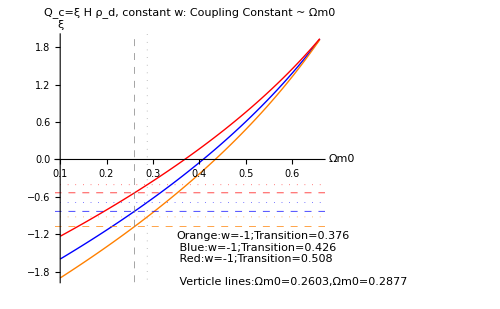

```mathematica
pltξvΩm0I2CCSum=Plot[{ξI2CCffunc[Ωm0ICC,1-Ωm0ICC-0,-1,0.426],ξI2CCffunc[Ωm0ICC,1-Ωm0ICC-0,-1,0.376],ξI2CCffunc[Ωm0ICC,1-Ωm0ICC-0,-1,0.508]},{Ωm0ICC,0.1,0.66},PlotStyle->{Blue,Orange,Red},AxesLabel->{"Ωm0","ξ"},GridLines->{{{0.2603,Directive[Gray,Dashed]},{0.2877,Directive[Gray,Dotted]}},{{-1.0776,Directive[Orange,Dashed]},{-0.8323,Directive[Blue,Dashed]},{-0.5358,Directive[Red,Dashed]},{-0.9226,Directive[Orange,Dotted]},{-0.6887,Directive[Blue,Dotted]},{-0.4059,Directive[Red,Dotted]}}},Epilog->Inset[Framed[Style["Orange:w=-1;Transition=0.376\n Blue:w=-1;Transition=0.426\n Red:w=-1;Transition=0.508\n \n Verticle lines:Ωm0=0.2603,Ωm0=0.2877",11],Background->LightGreen,FrameStyle->None],{0.35,-1.15},{Left,Top}],PlotLabel->"Q_c=ξ H ρ_d, constant w: Coupling Constant ~ Ωm0",ImageSize->500]
```

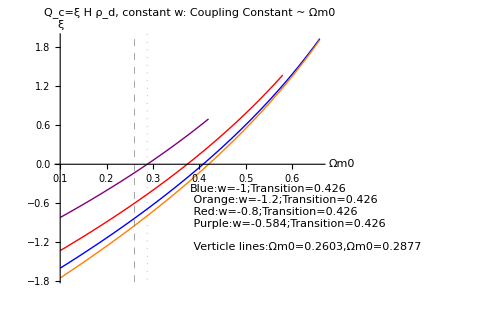

```mathematica
pltξvΩm0I2CCSum2=Show[{Plot[{ξI2CCffunc[Ωm0I2CC,1-Ωm0I2CC-0,-1,0.426],ξI2CCffunc[Ωm0I2CC,1-Ωm0I2CC-0,-1.2,0.426]},{Ωm0I2CC,0.1,0.66},PlotStyle->{Blue,Orange},AxesLabel->{"Ωm0","ξ"}],Plot[ξI2CCffunc[Ωm0I2CC,1-Ωm0I2CC-0,-0.8,0.426],{Ωm0I2CC,0.1,0.58},PlotStyle->Red,AxesLabel->{"Ωm0","ξ"}],Plot[ξI2CCffunc[Ωm0I2CC,1-Ωm0I2CC-0,eosI2CC1/.FindRoot[{ξI2CCffunc[0.2877,1-0.2877-0,eosI2CC1,0.426]==0},{eosI2CC1,-0.5}],0.426],{Ωm0I2CC,0.1,0.42},PlotStyle->Purple,AxesLabel->{"Ωm0","ξ"}]},GridLines->{{{0.2603,Directive[Gray,Dashed]},{0.2877,Directive[Gray,Dotted]}},{}},Epilog->Inset[Framed[Style["Blue:w=-1;Transition=0.426\n Orange:w=-1.2;Transition=0.426\n Red:w=-0.8;Transition=0.426\n Purple:w=-0.584;Transition=0.426\n \n Verticle lines:Ωm0=0.2603,Ωm0=0.2877",11],Background->LightGreen,FrameStyle->None],{0.38,-0.3},{Left,Top}],PlotLabel->"Q_c=ξ H ρ_d, constant w: Coupling Constant ~ Ωm0",ImageSize->500]//Quiet
```

Different plot ranges are chosen because for very large Ωm0, it is impossible to choose a parameter so that the transition redshift is

```mathematica
tabξvΩm0I2CCSum21=Grid[{{"Q_c=ξ H ρ_d, constant w: ξ when transition redshift is 0.426",SpanFromLeft},{"⋱","w=-0.4506","w=-0.4507"},{"Ωm0=0.2603",ξI2CCffunc[0.2603,1-0.2603-0,-0.4506,0.426],ξI2CCffunc[0.2603,1-0.2603-0,-0.4507,0.426]}},Frame->All,Background->{{LightGray,None},{LightGreen,LightGray,None}},ItemSize->13]//Quiet
tabξvΩm0I2CCSum22=Grid[{{"Q_c=ξ H ρ_d, constant w: EoS value when ξ=0",SpanFromLeft},{"⋱","Transition 0.426"},{"Ωm0=0.2877",eosI2CC1/.FindRoot[{ξI2CCffunc[0.2877,1-0.2877-0,eosI2CC1,0.426]==0},{eosI2CC1,-0.5}]}},Frame->All,ItemSize->13,Background->{{LightGray,None},{LightGreen,LightGray,None}}]//Quiet
```

Q_c=ξ H ρ_d, constant w: ξ when transition redshift is 0.426 |  | 
⋱ | w=-0.4506 | w=-0.4507
Ωm0=0.2603 | -17.5369 | 0.351603

Q_c=ξ H ρ_d, constant w: EoS value when ξ=0 | 
⋱ | Transition 0.426
Ωm0=0.2877 | -0.58406

So we give the result that w ∈ (-0.58406, -0.4507) if we constrain Ωm0 = 0.2603 and transition redshift 0.426.

Fitting result of ξ with different EoS.

```mathematica
fitξI2CCManSum=Manipulate[numPlot["(",{ξI2CCf1[wI2CC],ξI2CCfc[wI2CC],ξI2CCf2[wI2CC]},")",{-1.5,1}],{{wI2CC,-1,"Equation of State"},-3,-0.47,Appearance->"Open"},Delimiter,Style["This is the fitting result from transition redshift data.\n Q_c=ξ H ρ_d",Bold],Delimiter,"The parenthesis shows the upper and lower value \n while the verticle line show the center value.",Style["\n The three numbers are left value, center value, right value respectively."],Delimiter,Delimiter,Style["Slide to see how do the two parameters affect the coupling constant results."],ControlPlacement->{Bottom,Bottom},SaveDefinitions->True]
```

Coupling constant ξ vs EoS

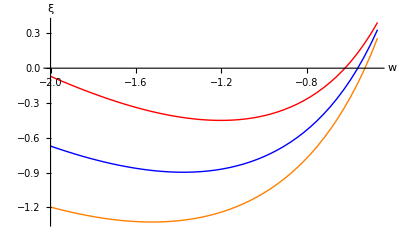

```mathematica
pltξvwI2CC=Plot[{ξI2CCfc[wI2CC],ξI2CCf1[wI2CC],ξI2CCf2[wI2CC]},{wI2CC,-2,-0.47},PlotStyle->{Blue,Orange,Red},AxesLabel->{"w","ξ"}]
```

Choose the values from Reference 3. w = -1.087 ± 0.096,

```mathematica
ξvwExamI2CC={Block[{wI2CC=-1.087-0.096},{wI2CC,ξI2CCfc[wI2CC],ξI2CCf1[wI2CC],ξI2CCf2[wI2CC]}],Block[{wI2CC=-1.087},{wI2CC,ξI2CCfc[wI2CC],ξI2CCf1[wI2CC],ξI2CCf2[wI2CC]}],Block[{wI2CC=-1.087+0.096},{wI2CC,ξI2CCfc[wI2CC],ξI2CCf1[wI2CC],ξI2CCf2[wI2CC]}]}
```

{{-1.183,-0.864289,-1.22984,-0.449552},{-1.087,-0.820486,-1.15946,-0.437339},{-0.991,-0.753634,-1.06346,-0.405262}}

```mathematica
tabξvwExamI2CC=Grid[Prepend[Prepend[ξvwExamI2CC,{"w","Center","Lower","Upper"}],{"Q_c=ξ H ρ_d,Constant w. (Data used:Data From, 2)",SpanFromLeft}],Frame->All,Background->{{LightGray,None},{LightGreen,LightGray,None}},Alignment->Center,ItemSize->8]
```

Q_c=ξ H ρ_d,Constant w. (Data used:Data From, 2) |  |  | 
w | Center | Lower | Upper
-1.183 | -0.864289 | -1.22984 | -0.449552
-1.087 | -0.820486 | -1.15946 | -0.437339
-0.991 | -0.753634 | -1.06346 | -0.405262

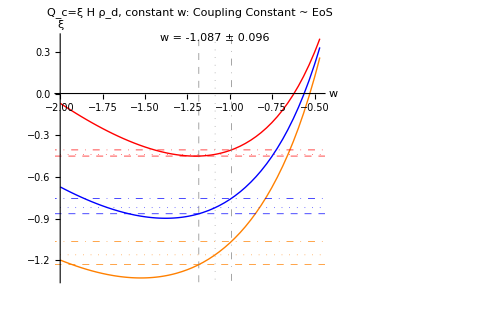

```mathematica
pltξvwExamI2CC=Show[pltξvwI2CC,GridLines->{{{ξvwExamI2CC[[1,1]],Directive[Gray,Dashed]},{ξvwExamI2CC[[2,1]],Directive[Gray,Dotted]},{ξvwExamI2CC[[3,1]],Directive[Gray,DotDashed]}},{{ξvwExamI2CC[[1,3]],Directive[Orange,Dashed]},{ξvwExamI2CC[[1,2]],Directive[Blue,Dashed]},{ξvwExamI2CC[[1,4]],Directive[Red,Dashed]},{ξvwExamI2CC[[2,3]],Directive[Orange,Dotted]},{ξvwExamI2CC[[2,2]],Directive[Blue,Dotted]},{ξvwExamI2CC[[2,4]],Directive[Red,Dotted]},{ξvwExamI2CC[[3,3]],Directive[Orange,DotDashed]},{ξvwExamI2CC[[3,2]],Directive[Blue,DotDashed]},{ξvwExamI2CC[[3,4]],Directive[Red,DotDashed]}}},Epilog->{Inset[Framed[Style["w = -1.087 ± 0.096",10],Background->LightBlue,FrameStyle->None],{-1.087,0.4},{0,Top}],Inset[Framed[Style["Orange:Ωm0=0.261;Transition=0.376\n Blue:Ωm0=0.274;Transition=0.426\n Red:Ωm0=0.287;Transition=0.508",11],Background->LightGreen,FrameStyle->None],{-1.95,0.44},{Left,Top}]},PlotLabel->"Q_c=ξ H ρ_d, constant w: Coupling Constant ~ EoS",ImageSize->500]
```

Or more casually, use w=-1±0.05

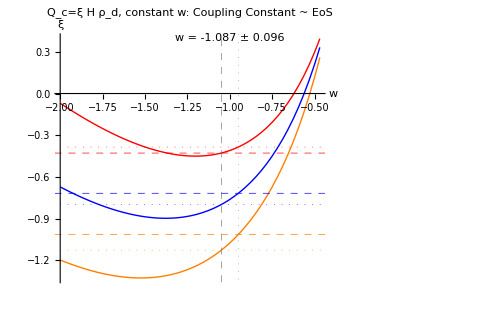

```mathematica
pltξvwExam1I2CC=Show[pltξvwI2CC,GridLines->{{{-1.05,Directive[Gray,Dashed]},{-0.95,Directive[Gray,Dotted]}},{{-1.013,Directive[Orange,Dashed]},{-0.717,Directive[Blue,Dashed]},{-0.428,Directive[Red,Dashed]},{-1.126,Directive[Orange,Dotted]},{-0.798,Directive[Blue,Dotted]},{-0.385,Directive[Red,Dotted]}}},Epilog->{Inset[Framed[Style["w = -1.087 ± 0.096",10],Background->LightBlue,FrameStyle->None],{-1,0.4},{0,Top}],Inset[Framed[Style["Orange:Ωm0=0.261;Transition=0.376\n Blue:Ωm0=0.274;Transition=0.426\n Red:Ωm0=0.287;Transition=0.508",11],Background->LightGreen,FrameStyle->None],{-1.9,0.44},{Left,Top}]},PlotLabel->"Q_c=ξ H ρ_d, constant w: Coupling Constant ~ EoS",ImageSize->500]
```

If we use transition redshift data only,

```mathematica
fitξ2I2CCManSum=Manipulate[numPlot["(",{ξI2CCffunc[Ωm0I2CC,1-Ωm0I2CC-Ωk0I2CC,wI2CC,0.376],ξI2CCffunc[Ωm0I2CC,1-Ωm0I2CC-Ωk0I2CC,wI2CC,0.426],ξI2CCffunc[Ωm0I2CC,1-Ωm0I2CC-Ωk0I2CC,wI2CC,0.508]},")",{-2.5,1}],{{Ωm0I2CC,0.274,"Matter Fraction"},0.1,0.66,Appearance->"Open"},{{Ωk0I2CC,0,"Curvature"},-0.1,0.1,Appearance->"Open"},{{wI2CC,-1,"Equation of State"},-2,-0.47,Appearance->"Open"},Delimiter,Style["Q_c=ξ H ρ_d, constant w, constant ζ.",Bold],Delimiter,Style["This is the fitting result of ξ from only transition redshift data.\n without the knowledge of Ωm0. "],Delimiter,Style["Slide to check how do EoS change this curve."],ControlPlacement->{Right},SaveDefinitions->True]
```

```mathematica
pltξvΩm0I2CCManSum=Manipulate[Plot[{ξI2CCffunc[Ωm0I2CC,1-Ωm0I2CC-Ωk0I2CC,wI2CC,0.426],ξI2CCffunc[Ωm0I2CC,1-Ωm0I2CC-Ωk0I2CC,wI2CC,0.376],ξI2CCffunc[Ωm0I2CC,1-Ωm0I2CC-Ωk0I2CC,wI2CC,0.508]},{Ωm0I2CC,0.1,(tmpe/.FindRoot[ztrI2CC[tmpe,1-tmpe-Ωk0I2CC,wI2CC,0.1]==0,{tmpe,0.1}])-0.001},PlotStyle->{Blue,Orange,Red},AxesLabel->{"Ωm0","ξ"},PlotLabel->"Q_c=ξ H ρ_d, constant w, constant ξ"],{{Ωk0I2CC,0,"Curvature"},-0.1,0.1,Appearance->"Open"},{{wI2CC,-1,"Equation of State"},-2,-0.47,Appearance->"Open"},Delimiter,Style["Blue line is the center of ξ\n The other lines are the upper and lower value"],Delimiter,Style["Slide to check how do matter change this curve."],ControlPlacement->{Right},SaveDefinitions->True]
```

#### Check consistancy

```mathematica
{ξI2CCffunc[0.263623,1-0.263623,-1,0.376],ξI2CCffunc[0.274310595065312,1-0.274310595065312,-1,0.426],ξI2CCffunc[0.28469241773962806,1-0.28469241773962806,-1,0.508]}
```

{-1.05903,-0.759371,-0.420298}

### Constant ξ + CPL w. I2CPL model.

#### Definations

CPL EoS w=w0+w1 z/(1+z)

In the following calculation, some complex numbers will occur. But

Prepare

```mathematica
hubblecmpintI2CCPL[w0_,w1_,ξI2CCPL_,z_?NumberQ]:=Integrate[Exp[3 w1/(1+tmp)-3w1](1+tmp)^(3(w0+w1)+ξI2CCPL-1),{tmp,0,z},Assumptions->{tmp∈Reals&&z∈Reals&&z>-1}]
```

```mathematica
hubblecmpintI2CCPLtest[w0_,w1_,ξI2CCPL_,z_?NumberQ]:=NIntegrate[Exp[3 w1/(1+tmp)-3w1](1+tmp)^(3(w0+w1)+ξI2CCPL-1),{tmp,0,z}]
```

```mathematica
hubblecmpintI2CCPL[-1,0.1,0.1,10]//Timing
Re[%]
hubblecmpintI2CCPLtest[-1,0.1,0.1,10]//Timing
```

{0.967,0.353978-2.63192×10^-15 ⅈ}

{0.967,0.353978}

{0.,0.353978}

Matter density

```mathematica
ΩmI2CCPL[Ωd0I2CCPL_,Ωm0I2CCPL_,w0I2CCPL_,w1I2CCPL_,ξI2CCPL_,z_]=Ωm0I2CCPL (1+z)^3-ξI2CCPL Ωm0I2CCPL (1+z)^3 hubblecmpintI2CCPL[w0I2CCPL,w1I2CCPL,ξI2CCPL,z];
```

```mathematica
ΩmI2CCPLtest[Ωd0I2CCPL_,Ωm0I2CCPL_,w0I2CCPL_,w1I2CCPL_,ξI2CCPL_,z_?NumberQ]=Ωm0I2CCPL (1+z)^3-ξI2CCPL Ωm0I2CCPL (1+z)^3 hubblecmpintI2CCPLtest[w0I2CCPL,w1I2CCPL,ξI2CCPL,z];
```

```mathematica
ΩdI2CCPL[Ωd0I2CCPL_,w0I2CCPL_,w1I2CCPL_,ξI2CCPL_,z_]:=Ωd0I2CCPL Exp[-3z w1I2CCPL/(1+z)](1+z)^(3(1+w0I2CCPL+w1I2CCPL)+ξI2CCPL)
```

Hubble function.

```mathematica
hubbleI2CCPL[H0I2CCPL_,Ωd0I2CCPL_,Ωm0I2CCPL_,w0I2CCPL_,w1I2CCPL_,ξI2CCPL_,z_]=H0I2CCPL√(ΩmI2CCPL[Ωd0I2CCPL,Ωm0I2CCPL,w0I2CCPL,w1I2CCPL,ξI2CCPL,z]+ΩdI2CCPL[Ωd0I2CCPL,w0I2CCPL,w1I2CCPL,ξI2CCPL,z]);
```

```mathematica
hubbleI2CCPLtest[H0I2CCPL_,Ωd0I2CCPL_,Ωm0I2CCPL_,w0I2CCPL_,w1I2CCPL_,ξI2CCPL_,z_?NumberQ]=H0I2CCPL√(ΩmI2CCPLtest[Ωd0I2CCPL,Ωm0I2CCPL,w0I2CCPL,w1I2CCPL,ξI2CCPL,z]+ΩdI2CCPL[Ωd0I2CCPL,w0I2CCPL,w1I2CCPL,ξI2CCPL,z]);
```

```mathematica
hubbleDI2CCPL[H0I2CCPL_,Ωd0I2CCPL_,Ωm0I2CCPL_,w0I2CCPL_,w1I2CCPL_,ξI2CCPL_,z_]=D[hubbleI2CCPL[H0I2CCPL,Ωd0I2CCPL,Ωm0I2CCPL,w0I2CCPL,w1I2CCPL,ξI2CCPL,z],z];
```

```mathematica
hubbleDI2CCPLtest[H0I2CCPL_,Ωd0I2CCPL_,Ωm0I2CCPL_,w0I2CCPL_,w1I2CCPL_,ξI2CCPL_,z_]=(hubbleI2CCPLtest[H0I2CCPL,Ωd0I2CCPL,Ωm0I2CCPL,w0I2CCPL,w1I2CCPL,ξI2CCPL,z+0.001]-hubbleI2CCPLtest[H0I2CCPL,Ωd0I2CCPL,Ωm0I2CCPL,w0I2CCPL,w1I2CCPL,ξI2CCPL,z-0.001])/0.002;
```

```mathematica
hubbleI2CCPL[H0w,0.7,0.3,-1,0.1,0.1,10]//Timing
Re[%]
hubbleI2CCPLtest[H0w,0.7,0.3,-1,0.1,0.1,10]//Timing
hubbleDI2CCPL[H0w,0.7,0.3,-1,0.1,0.1,10]//Timing
Re[%]
hubbleDI2CCPLtest[H0w,0.7,0.3,-1,0.1,0.1,10]//Timing
```

{0.733,1395.93+1.89755×10^-13 ⅈ}

{0.733,1395.93}

{0.016,1395.93}

{45.989,189.745+2.59585×10^-14 ⅈ}

{45.989,189.745}

{0.015,189.745}

Check whether this hubble function is reasonable.

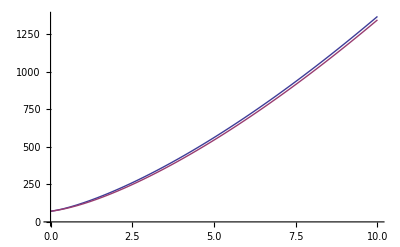

```mathematica
Plot[{hubbleI2CCPLtest[H0w,0.73,0.27,-1,0.6,-0.02,z],hubble[Ωm0w,Ωd0w,0,z]},{z,0,10}]
```

Deceleration parameter

```mathematica
qI2CCPL[H0I2CCPL_,Ωd0I2CCPL_,Ωm0I2CCPL_,w0I2CCPL_,w1I2CCPL_,ξI2CCPL_,z_]=-1+(1+z)/hubbleI2CCPLtest[H0I2CCPL,Ωd0I2CCPL,Ωm0I2CCPL,w0I2CCPL,w1I2CCPL,ξI2CCPL,z]hubbleDI2CCPLtest[H0I2CCPL,Ωd0I2CCPL,Ωm0I2CCPL,w0I2CCPL,w1I2CCPL,ξI2CCPL,z];
```

```mathematica
qI2CCPL[H0w,0.7,0.3,-1,0.1,0.1,10]//Timing
```

{0.032,0.495197}

#### Equation of State

```mathematica
plEoSI2CCPLMan=plEoSICCPLMan
```

```mathematica
plEoSPhaseI2CCPL=plEoSPhaseICCPL
```

-Graphics-

#### Plot deceleration parameter and

```mathematica
pldecI2CCPL[Ωm0I2CCPL_,ξI2CCPL_,w0I2CCPL_,w1I2CCPL_,color_]:=Plot[qI2CCPL[H0w,1-Ωm0I2CCPL,Ωm0I2CCPL,w0I2CCPL,w1I2CCPL,ξI2CCPL,z],{z,-1,20},PlotRange->{{-1.05,20},{-1.05,1}},PlotStyle->color,AxesOrigin->{-1,0},AxesLabel->{z,q}];
```

```mathematica
discretepldecI2CCPL[Ωm0I2CCPL_,ξI2CCPL_,w0I2CCPL_,w1I2CCPL_,color_]:=DiscretePlot[qI2CCPL[H0w,1-Ωm0I2CCPL,Ωm0I2CCPL,w0I2CCPL,w1I2CCPL,ξI2CCPL,z],{z,-1,10,1},PlotStyle->color,AxesOrigin->{-1,0},AxesLabel->{z,q}]
```

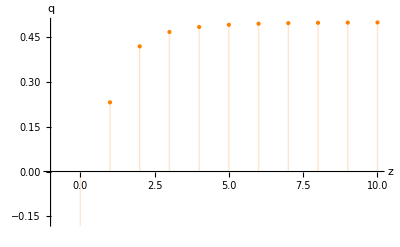
{0.53,-Graphics-}

```mathematica
discretepldecI2CCPL[0.3,-0.4,-1,0.1,Orange]//Timing//Quiet
```

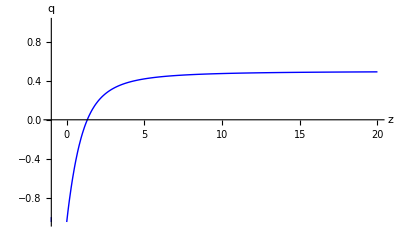
{9.766,-Graphics-}

```mathematica
pldecI2CCPL[0.1,-0.4,-1.02,0.60,Blue]//Timing//Quiet
```

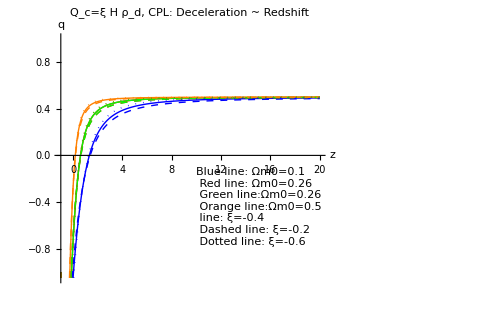

```mathematica
pldecI2CCPLShowSum=Show[{pldecI2CCPL[0.1,-0.4,-1.02,0.60,Blue],pldecI2CCPL[0.26,-0.4,-1.02,0.60,Red],pldecI2CCPL[0.26,-0.4,-1.02,0.60,Green],pldecI2CCPL[0.5,-0.4,-1.02,0.60,Orange],pldecI2CCPL[0.1,-0.2,-1.02,0.60,Directive[Blue,Dashed]],pldecI2CCPL[0.26,-0.2,-1.02,0.60,Directive[Red,Dashed]],pldecI2CCPL[0.26,-0.2,-1.02,0.60,Directive[Green,Dashed]],pldecI2CCPL[0.5,-0.2,-1.02,0.60,Directive[Orange,Dashed]],pldecI2CCPL[0.1,-0.6,-1.02,0.60,Directive[Blue,Dotted]],pldecI2CCPL[0.26,-0.6,-1.02,0.60,Directive[Red,Dotted]],pldecI2CCPL[0.26,-0.6,-1.02,0.60,Directive[Green,Dotted]],pldecI2CCPL[0.5,-0.6,-1.02,0.60,Directive[Orange,Dotted]]},Epilog->Inset[Framed[Style["Blue line: Ωm0=0.1\n Red line: Ωm0=0.26\n Green line:Ωm0=0.26\n Orange line:Ωm0=0.5\n line: ξ=-0.4\n Dashed line: ξ=-0.2\n Dotted line: ξ=-0.6",10],Background->LightGreen,FrameStyle->None],{10,-0.1},{Left,Top}],PlotLabel->"Q_c=ξ H ρ_d, CPL: Deceleration ~ Redshift",ImageSize->500]//Quiet
```

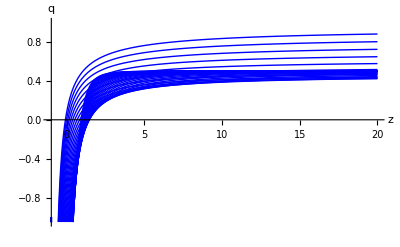
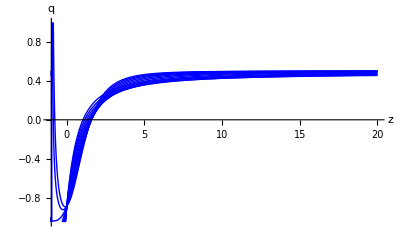
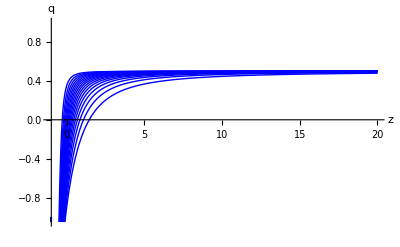
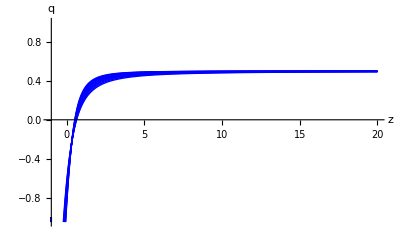
Q_c=ξ H ρ_d, CPL |  |  | 
Varying CPL w0 | Varying CPL w1 | Varying Ωm0 | Varying ξ
-Graphics- | -Graphics- | -Graphics- | -Graphics-

```mathematica
varyingI2CCPLShowSum=Grid[{{"Q_c=ξ H ρ_d, CPL",SpanFromLeft},{"Varying CPL w0","Varying CPL w1","Varying Ωm0","Varying ξ"},{Show[Table[pldecI2CCPL[0.1,-0.02,w0I2CCPL,0.6,Blue],{w0I2CCPL,-2,-0.3,0.05}]],Show[Table[pldecI2CCPL[0.1,-0.02,-1.02,w1I2CCPL,Blue],{w1I2CCPL,-0.2,1,0.1}]],Show[Table[pldecI2CCPL[Ωm0I2CCPL,-0.02,-1.02,0.6,Blue],{Ωm0I2CCPL,0.1,0.9,0.05}]],Show[Table[pldecI2CCPL[0.27,ξI2CCPL,-1.02,0.6,Blue],{ξI2CCPL,-1,0,0.1}]]}},Frame->All,Background->{{None},{LightGreen,None}}]//Quiet
```

```mathematica
(* Do not run the following if not needed. *)
(*
pldecI2CCPLManSum=Manipulate[Show[{pldecI2CCPL[Ωm0I2CCPL,ξI2CCPL,w0I2CCPL,w1I2CCPL,Orange],pldec[Ωm0I2CCPL,{Pink,Thick}]},PlotLabel->"Q_c=ξ H ρ_d,CPL: Deceleration ~ Redshift"],{{Ωm0I2CCPL,0.26,"Matter Fraction"},0,1,Appearance->"Open"},{{ξI2CCPL,-0.4,"Interaction"},-1,0,Appearance->"Open"},{{w0I2CCPL,-1.02,"CPL EoS w0"},-2,-0.3,Appearance->"Open"},{{w1I2CCPL,0.6,"CPL EoS w1"},-0.2,1,Appearance->"Open"},Delimiter,Style["Pink is the deceleration parameter for LCDM.",Medium],Style["Orange is for interacting CPL model with Q=ξ H ρ_d",Medium],ControlPlacement->{Right,Right,Right},SaveDefinitions->True]//Quiet
*)
```

#### Transition Redshift

Find out the expression for transition redshift

```mathematica
ztrI2CCPL[Ωm0I2CCPL_,Ωd0I2CCPL_,ξI2CCPL_,w0I2CCPL_,w1I2CCPL_]:=z/.FindRoot[(1+3(w0I2CCPL+w1I2CCPL z/(1+z)))ΩdI2CCPL[Ωd0I2CCPL,w0I2CCPL,w1I2CCPL,ξI2CCPL,z]+ΩmI2CCPLtest[Ωd0I2CCPL,Ωm0I2CCPL,w0I2CCPL,w1I2CCPL,ξI2CCPL,z]==0,{z,3}];
```

```mathematica
ztrI2CCPL[0.3,1-0.3,0,-1,0.1]//Timing
```

{0.203,0.655139}

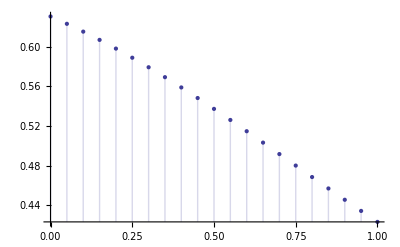

```mathematica
DiscretePlot[{ztrI2CCPL[0.3,1-0.3,-0.1,-1,tmp]},{tmp,0,1,0.05}]//Quiet
```

The following is just used for test.

```mathematica
(*
(*This is a test of how well are the findroot results.*)
Plot[{plottestfunctiontemp[temp,1-temp,-0.1,-0.9,-0.05,ztrICCPLtest2[temp,1-temp,-0.1,-0.9,-0.05]],plottestfunctiontemp[temp,1-temp,-0.1,-0.9,-0.05,ztrICCPLtest[temp,1-temp,-0.1,-0.9,-0.05]],plottestfunctiontemp[temp,1-temp,-0.1,-0.9,-0.05,ztrICCPL[temp,1-temp,-0.1,-0.9,-0.05]]},{temp,0,1},PlotStyle->{Red,Orange,Blue}]
*)
```

Define rICC=Ωm0ICC/Ωd0ICC

```mathematica
ΩmrI2CCPL[rI2CCPL_,w0I2CCPL_,w1I2CCPL_,ξI2CCPL_,z_]=rI2CCPL (1+z)^3-ξI2CCPL rI2CCPL (1+z)^3 Re[hubblecmpintI2CCPLtest[w0I2CCPL,w1I2CCPL,ξI2CCPL,z]];
```

```mathematica
ΩdrI2CCPL[rI2CCPL_,w0I2CCPL_,w1I2CCPL_,ξI2CCPL_,z_]:= Exp[-3 w1I2CCPL] Exp[3 w1I2CCPL/(1+z)](1+z)^(3(1+w0I2CCPL+w1I2CCPL)+ξI2CCPL);
```

```mathematica
ztrrI2CCPL[rI2CCPL_,ξI2CCPL_,w0I2CCPL_,w1I2CCPL_]:=z/.FindRoot[(1+3(w0I2CCPL+w1I2CCPL z/(1+z)))ΩdrI2CCPL[rI2CCPL,w0I2CCPL,w1I2CCPL,ξI2CCPL,z]+ΩmrI2CCPL[rI2CCPL,w0I2CCPL,w1I2CCPL,ξI2CCPL,z]==0,{z,3}];
```

Test this.

```mathematica
ztrrI2CCPL[0.5,-0.02,-1,0.6]//Timing
```

{0.202,0.468557}

#### Visualization

Check the behavior of this transition redshift.

```mathematica
ztrI2CCPL[0.1,1-0.1,-0.02,-1,0.2]//Timing
```

{0.188,1.59839}

```mathematica
ztrI2CCPL[0.25,1-0.25,-0.02,-1,0.2]//Timing
ztrI2CCPL[0.25,1-0.25,0.02,-1,0.2]//Timing
```

{0.218,0.772156}

{0.218,0.793023}

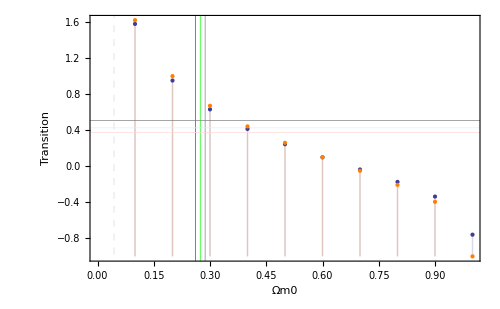

```mathematica
discretepldecΩm0I2CCPL=DiscretePlot[{ztrI2CCPL[Ωm0I2CCPL,1-Ωm0I2CCPL,-0.02,-1.02,0.2],ztr[Ωm0I2CCPL,1-Ωm0I2CCPL]},{Ωm0I2CCPL,0,1,0.1},PlotStyle->{Thick,Orange},AxesOrigin->{0,-1},Frame->True,GridLines->{{{0.044,Dashed},{0.261,Red},{0.274,Green},{0.287,Gray}},{{0.376,LightRed},{0.426,LightBlue},{0.508,Gray}}},ImageSize->500,FrameLabel->{"Ωm0","Transition"}]//Quiet
```

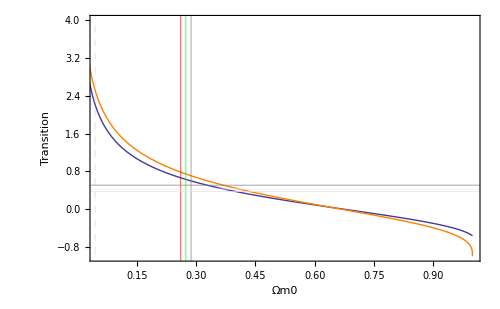

```mathematica
pldecΩm0I2CCPL=Plot[{ztrI2CCPL[Ωm0I2CCPL,1-Ωm0I2CCPL,-0.2,-1.02,0.2],ztr[Ωm0I2CCPL,1-Ωm0I2CCPL]},{Ωm0I2CCPL,0,1},PlotRange->{{0.05,1},{-1,4}},PlotStyle->{Thick,Orange},AxesOrigin->{0.05,-1},Frame->True,GridLines->{{{0.044,Dashed},{0.261,Red},{0.274,Green},{0.287,Gray}},{{0.376,LightRed},{0.426,LightBlue},{0.508,Gray}}},PlotLegend->{"Q=-0.02 H ρ_d","LCDM"},LegendPosition->{0.0,-0.05},LegendShadow->None,ImageSize->500,FrameLabel->{"Ωm0","Transition"}]//Quiet
```

```mathematica
plztrI2CCPL[ξI2CCPL_,w0I2CCPL_,w1I2CCPL_,color_,{ranges_:0,rangee_:1}]:=Plot[ztrI2CCPL[Ωm0I2CCPL,1-Ωm0I2CCPL,ξI2CCPL,w0I2CCPL,w1I2CCPL],{Ωm0I2CCPL,0,1},PlotRange->{{ranges,rangee},{-1,4}},PlotStyle->color,AxesOrigin->{0,-1},Frame->True,FrameLabel->{"Ωm0","Transtion"}];
```

```mathematica
(* Do not evaluate this cell if not necessary. *)
(*
plztrI2CCPLManSum=Manipulate[Show[{plztrI2CCPL[ξI2CCPL,w0I2CCPL,w1I2CCPL,Orange,{0,1}],Plot[ztr[Ωm0I2CCPL,1-Ωm0I2CCPL],{Ωm0I2CCPL,0,1},PlotRange->{{0,1},{-1,4}},PlotStyle->Pink,AxesOrigin->{0,-1}]},Graphics[{Gray,Rectangle[Scaled[{0.261,.2752}],Scaled[{0.287,.3016}]]},Frame->True],GridLines->{{},{{0,Dashed}}},FrameLabel->{"Ωm0","Transition"},PlotLabel->"Q_c=ξ H ρ_d, CPL: Transition ~ Ωm0"],{{ξI2CCPL,-0.4,"Interaction"},-1,0,Appearance->"Open"},{{w0I2CCPL,-1.02,"CPL EoS w0"},-2,-0.3,Appearance->"Open"},{{w1I2CCPL,0.6,"CPL EoS w1"},-0.2,1,Appearance->"Open"},Delimiter,Style["Orange is for interacting CPL model with Q=ξ H ρ_m",Medium],ControlPlacement->{Right,Right,Right},SaveDefinitions->True]//Quiet
*)
```

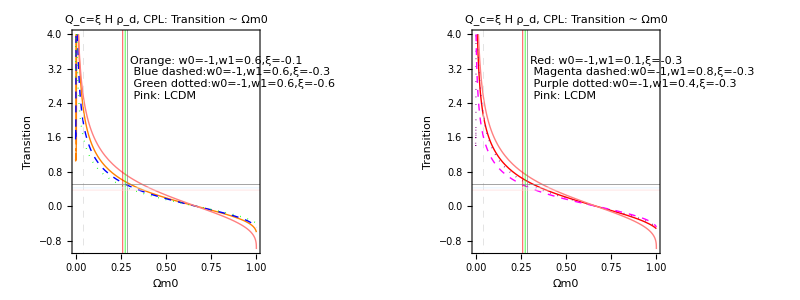

```mathematica
plztrExamI2CCPLSum=Grid[{{Show[{plztrI2CCPL[-0.1,-1,0.6,Orange,{0,1}],plztrI2CCPL[-0.3,-1,0.6,{Blue,Dashed},{0,1}],plztrI2CCPL[-0.6,-1,0.6,{Green,Dotted},{0,1}],Plot[ztr[Ωm0I2CCPL,1-Ωm0I2CCPL],{Ωm0I2CCPL,0,1},PlotRange->{{0,1},{-1,4}},PlotStyle->Pink,AxesOrigin->{0,-1}]},GridLines->{{{0.044,Dashed},{0.261,Red},{0.274,Green},{0.287,Gray}},{{0.376,LightRed},{0.426,LightBlue},{0.508,Gray}}},GridLines->{{},{{0,Dashed}}},Epilog->Inset[Framed[Style["Orange: w0=-1,w1=0.6,ξ=-0.1\n Blue dashed:w0=-1,w1=0.6,ξ=-0.3\n Green dotted:w0=-1,w1=0.6,ξ=-0.6\n Pink: LCDM",10],Background->LightGreen,FrameStyle->None],{0.3,3.5},{Left,Top}],FrameLabel->{"Ωm0","Transition"},PlotLabel->"Q_c=ξ H ρ_d, CPL: Transition ~ Ωm0",ImageSize->400],Show[{plztrI2CCPL[-0.3,-1,0.1,Red,{0,1}],plztrI2CCPL[-0.3,-1,0.4,{Purple,Dotted},{0,1}],plztrI2CCPL[-0.3,-1,0.8,{Magenta,Dashed},{0,1}],Plot[ztr[Ωm0I2CCPL,1-Ωm0I2CCPL],{Ωm0I2CCPL,0,1},PlotRange->{{0,1},{-1,4}},PlotStyle->Pink,AxesOrigin->{0,-1}]},GridLines->{{{0.044,Dashed},{0.261,Red},{0.274,Green},{0.287,Gray}},{{0.376,LightRed},{0.426,LightBlue},{0.508,Gray}}},GridLines->{{},{{0,Dashed}}},Epilog->Inset[Framed[Style["Red: w0=-1,w1=0.1,ξ=-0.3\n Magenta dashed:w0=-1,w1=0.8,ξ=-0.3\n Purple dotted:w0=-1,w1=0.4,ξ=-0.3\n Pink: LCDM",10],Background->LightGreen,FrameStyle->None],{0.3,3.5},{Left,Top}],FrameLabel->{"Ωm0","Transition"},PlotLabel->"Q_c=ξ H ρ_d, CPL: Transition ~ Ωm0",ImageSize->400]}}]//Quiet
```

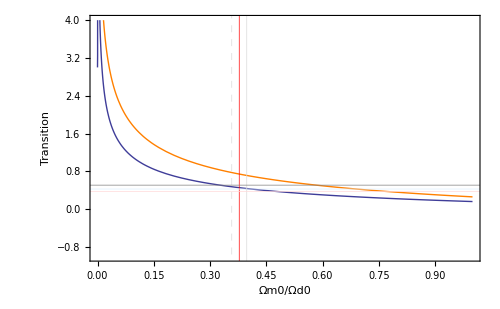

```mathematica
pldecrI2CCPL=Plot[{ztrrI2CCPL[rI2CCPL,-0.6,-1.02,0.6],ztrr[rI2CCPL]},{rI2CCPL,0,1},PlotRange->{{0,1},{-1,4}},PlotStyle->{Thick,Orange},AxesOrigin->{0,-1},Frame->True,GridLines->{{{0.358,Dashed},{0.378,Directive[Red]},0.398},{{0.376,LightRed},{0.426,LightBlue},{0.508,Gray}}},PlotLegend->{"CPL,Q=-0.6 H ρ_d","LCDM"},LegendPosition->{0.0,-0.05},LegendShadow->None,ImageSize->500,FrameLabel->{"Ωm0/Ωd0","Transition"}]//Quiet
```

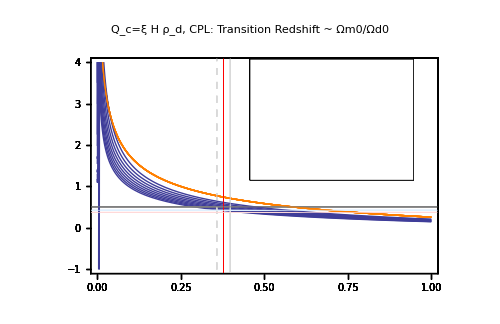

```mathematica
pltransrI2CCPLDense=Show[Table[Plot[{ztrrI2CCPL[rI2CCPL,ξI2CCPL,-1.02,0.6],ztrr[rI2CCPL]},{rI2CCPL,0,1},PlotRange->{{0,1},{-1,4}},PlotStyle->{Thick,Orange},AxesOrigin->{0,-1},Frame->True,GridLines->{{{0.358,Dashed},{0.378,Directive[Red]},0.398},{{0.376,LightRed},{0.426,LightBlue},{0.508,Gray}}},PlotLegend->{"CPL,Q=ξ H ρ_d,\n with ξ∈(-0.8,0) step=0.1","LCDM"},LegendPosition->{0.0,-0.05},LegendShadow->None],{ξI2CCPL,-0.8,0,0.1}],ImageSize->500,FrameLabel->{"Ωm0/Ωd0","Transition"},PlotLabel->"Q_c=ξ H ρ_d, CPL: Transition Redshift ~ Ωm0/Ωd0",ImageSize->500]//Quiet
```

#### Find out allowed region of coupling constant

To find out the region of ξ, set w=-1 and Ωd0=1-Ωm0. Let the ztr-Ωm0 line cross points (0.287,0.508) and (0.261, 0.376).

```mathematica
Off[FindRoot::nlnum]
Off[ReplaceAll::reps]
ztrI2CCPL[Ωm0I2CCPL,Ωd0I2CCPL,ξI2CCPL,w0I2CCPL,w1I2CCPL]
On[FindRoot::nlnum]
On[ReplaceAll::reps]
```

NIntegrate::inumr: The integrand ⅇ^-3\ w1I2CCPL + 3\ w1I2CCPL/1 + tmp\ (1 + tmp)^-1 + 3\ (w0I2CCPL + w1I2CCPL) + ξI2CCPL has evaluated to non-numerical values for all sampling points in the region with boundaries {{0, 3.}}.

NIntegrate::inumr: The integrand ⅇ^-3.\ w1I2CCPL + 3.\ w1I2CCPL/1.  + tmp\ (1.  + tmp)^-1. + 3.\ (w0I2CCPL + w1I2CCPL) + ξI2CCPL
 has evaluated to non-numerical values for all sampling points in the region with boundaries {{0., 3.}}.

General::stop: Further output of NIntegrate :: inumr will be suppressed during this calculation.

z/.FindRoot[(1+3 (w0I2CCPL+(w1I2CCPL z)/(1+z))) ΩdI2CCPL[Ωd0I2CCPL,w0I2CCPL,w1I2CCPL,ξI2CCPL,z]+ΩmI2CCPLtest[Ωd0I2CCPL,Ωm0I2CCPL,w0I2CCPL,w1I2CCPL,ξI2CCPL,z]==0,{z,3}]

```mathematica
(* ztrICCPL[0.287,1-0.287,ξICCPL1,-1.02,0.6]==0.508 *)
```

```mathematica
ξI2CCPLffunc[Ωm0I2CCPL_,Ωd0I2CCPL_,w0I2CCPL_,w1I2CCPL_,data_]:=ξI2CCPL/.FindRoot[ztrI2CCPL[Ωm0I2CCPL,Ωd0I2CCPL,ξI2CCPL,w0I2CCPL,w1I2CCPL]==data,{ξI2CCPL,-0.6}]
```

```mathematica
ξI2CCPLf2[Ωm0I2CCPL_,Ωd0I2CCPL_,w0I2CCPL_,w1I2CCPL_]:=ξI2CCPL/.FindRoot[ztrI2CCPL[Ωm0I2CCPL,Ωd0I2CCPL,ξI2CCPL,w0I2CCPL,w1I2CCPL]==0.508,{ξI2CCPL,-0.6}]
```

```mathematica
ξI2CCPLf1[Ωm0I2CCPL_,Ωd0I2CCPL_,w0I2CCPL_,w1I2CCPL_]:=ξI2CCPL/.FindRoot[ztrI2CCPL[Ωm0I2CCPL,Ωd0I2CCPL,ξI2CCPL,w0I2CCPL,w1I2CCPL]==0.376,{ξI2CCPL,-0.6}]
```

Cross the Center of best fit. (0.274,0.426)

```mathematica
ξI2CCPLfc[Ωm0I2CCPL_,Ωd0I2CCPL_,w0I2CCPL_,w1I2CCPL_]:=ξI2CCPL/.FindRoot[ztrI2CCPL[Ωm0I2CCPL,Ωd0I2CCPL,ξI2CCPL,w0I2CCPL,w1I2CCPL]==0.426,{ξI2CCPL,-0.6}]
```

According to the data of transition redshift.

```mathematica
ξI2CCPLf2[w0I2CCPL_,w1I2CCPL_]:=ξI2CCPLffunc[0.287,1-0.287,w0I2CCPL,w1I2CCPL,0.508]
```

```mathematica
ξI2CCPLf1[w0I2CCPL_,w1I2CCPL_]:=ξI2CCPLffunc[0.261,1-0.261,w0I2CCPL,w1I2CCPL,0.376]
```

```mathematica
ξI2CCPLfc[w0I2CCPL_,w1I2CCPL_]:=ξI2CCPLffunc[0.274,1-0.274,w0I2CCPL,w1I2CCPL,0.426]
```

An example

```mathematica
Off[FindRoot::nlnum]
Off[ReplaceAll::reps]
{ξI2CCPLf1[-1.02,0.6],ξI2CCPLfc[-1.02,0.6],ξI2CCPLf2[-1.02,0.6]}
On[FindRoot::nlnum]
On[ReplaceAll::reps]
```

NIntegrate::inumr: The integrand ⅇ^-1.8 + 1.8/1 + tmp\ (1 + tmp)^-2.26 + ξI2CCPL has evaluated to non-numerical values for all sampling points in the region with boundaries {{0, 3.}}.

NIntegrate::inumr: The integrand ⅇ^-1.8 + 1.8/1.  + tmp\ (1.  + tmp)^-2.26 + ξI2CCPL
 has evaluated to non-numerical values for all sampling points in the region with boundaries {{0., 3.}}.

General::stop: Further output of NIntegrate :: inumr will be suppressed during this calculation.

{-1.24538,-0.758365,-0.251702}

```mathematica
ξI2CCPLrffunc[rI2CCPL_,w0I2CCPL_,w1I2CCPL_,data_]:=ξI2CCPL/.FindRoot[ztrrI2CCPL[rI2CCPL,ξI2CCPL,w0I2CCPL,w1I2CCPL]==data,{ξI2CCPL,-0.6}]
```

```mathematica
ξI2CCPLrf2[rI2CCPL_,w0I2CCPL_,w1I2CCPL_]:=ξI2CCPL/.FindRoot[ztrrI2CCPL[rI2CCPL,ξI2CCPL,w0I2CCPL,w1I2CCPL]==0.508,{ξI2CCPL,-0.6}]
```

```mathematica
ξI2CCPLrf1[rI2CCPL_,w0I2CCPL_,w1I2CCPL_]:=ξI2CCPL/.FindRoot[ztrrI2CCPL[rI2CCPL,ξI2CCPL,w0I2CCPL,w1I2CCPL]==0.376,{ξI2CCPL,-0.6}]
```

Cross the Center of best fit. (0.358,0.426)

```mathematica
ξI2CCPLrfc[rI2CCPL_,w0I2CCPL_,w1I2CCPL_]:=ξI2CCPL/.FindRoot[ztrrI2CCPL[rI2CCPL,ξI2CCPL,w0I2CCPL,w1I2CCPL]==0.426,{ξI2CCPL,-0.6}]
```

According to the data of transition redshift.

```mathematica
ξI2CCPLrf2[w0I2CCPL_,w1I2CCPL_]:=ξI2CCPLrffunc[0.398,w0I2CCPL,w1I2CCPL,0.508]
```

```mathematica
ξI2CCPLrf1[w0I2CCPL_,w1I2CCPL_]:=ξI2CCPLrffunc[0.358,w0I2CCPL,w1I2CCPL,0.376]
```

```mathematica
ξI2CCPLrfc[w0I2CCPL_,w1I2CCPL_]:=ξI2CCPLrffunc[0.378,w0I2CCPL,w1I2CCPL,0.426]
```

An example

```mathematica
Off[FindRoot::nlnum]
Off[ReplaceAll::reps]
{ξI2CCPLrf1[-1.02,0.6],ξI2CCPLrfc[-1.02,0.6],ξI2CCPLrf2[-1.02,0.6]}
On[FindRoot::nlnum]
On[ReplaceAll::reps]
```

NIntegrate::inumr: The integrand ⅇ^-1.8 + 1.8/1 + tmp\ (1 + tmp)^-2.26 + ξI2CCPL has evaluated to non-numerical values for all sampling points in the region with boundaries {{0, 3.}}.

NIntegrate::inumr: The integrand ⅇ^-1.8 + 1.8/1.  + tmp\ (1.  + tmp)^-2.26 + ξI2CCPL
 has evaluated to non-numerical values for all sampling points in the region with boundaries {{0., 3.}}.

General::stop: Further output of NIntegrate :: inumr will be suppressed during this calculation.

{-1.21472,-0.755302,-0.269941}

```mathematica
(* Do not evaluate it unless it is necessary. *)
(*
Off[FindRoot::nlnum]
Off[ReplaceAll::reps]
fitξI2CCPLManSum=Manipulate[Grid[{{numPlot["(",{ξI2CCPLf1[w0I2CCPL,w1I2CCPL],ξI2CCPLfc[w0I2CCPL,w1I2CCPL],ξI2CCPLf2[w0I2CCPL,w1I2CCPL]},")",{-1.5,1}],Plot[w0I2CCPL+w1I2CCPL temp/(temp+1),{temp,-0.9,10}]}}],{{w0I2CCPL,-1.02,"Equation of State w0"},-2,-0.47,Appearance->"Open"},{{w1I2CCPL,0.6,"Equation of State w1"},-1,1,Appearance->"Open"},Delimiter,Style["This is the fitting result from transition redshift data.",Bold],Delimiter,"The parenthesis shows the upper and lower value \n while the verticle line show the center value.",Style["\n The three numbers are left value, center value, right value respectively."],Delimiter,Delimiter,Style["Slide to see how do the two parameters affect the coupling constant results."],ControlPlacement->{Bottom,Bottom},SaveDefinitions->True]
*)
```

```mathematica
(*
On[FindRoot::nlnum]
On[ReplaceAll::reps]
*)
```

#### Quintom Case

The transition redshift. Six groups of parameters.
(-1, 0.1)  (-1, 0.2)  (-0.9,0.1)
(-1, -0.1)  (-1, -0.2)  (-1.1,-0.1)
In two plots, 
(-1, 0.1)  (-1, 0.2)  (-1, -0.1)  (-1, -0.2) 
(-1, 0.1)   (-0.9,0.1)  (-1, -0.1)   (-1.1,-0.1)

```mathematica
pltI2CCPLEoSfunc[w0I2CCPL_,w1I2CCPL_,color_]:=Plot[{w0I2CCPL+w1I2CCPL z/(1+z)},{z,-0.99,10},PlotStyle->color,AxesLabel->{"z","w"}];
```

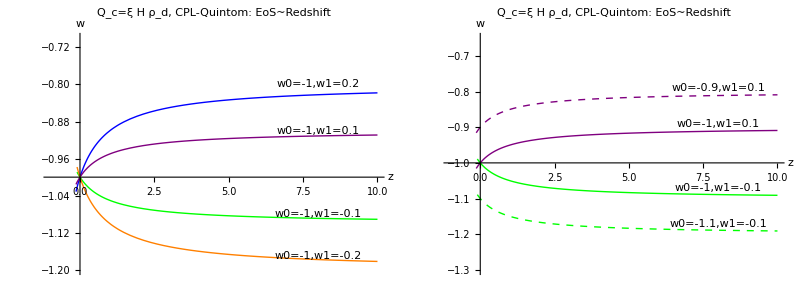

```mathematica
plEoSI2CCPLQuintomSum=Grid[{{Show[pltI2CCPLEoSfunc[-1,0.2,Blue],pltI2CCPLEoSfunc[-1,0.1,Purple],pltI2CCPLEoSfunc[-1,-0.1,Green],pltI2CCPLEoSfunc[-1,-0.2,Orange],PlotRange->{{-0.99,10},{-1.2,-0.7}},AxesOrigin->{0,-1},ImageSize->400,PlotLabel->"Q_c=ξ H ρ_d, CPL-Quintom: EoS~Redshift",Epilog->{Inset[Framed[Style["w0=-1,w1=0.2",10,Blue],Background->None,FrameStyle->None],{8,-0.80},{0,0}],Inset[Framed[Style["w0=-1,w1=0.1",10,Purple],Background->None,FrameStyle->None],{8,-0.9},{0,0}],Inset[Framed[Style["w0=-1,w1=-0.1",10,Green],Background->None,FrameStyle->None],{8,-1.08},{0,0}],Inset[Framed[Style["w0=-1,w1=-0.2",10,Orange],Background->None,FrameStyle->None],{8,-1.17},{0,0}]}],Show[pltI2CCPLEoSfunc[-1,0.1,Purple],pltI2CCPLEoSfunc[-0.9,0.1,{Purple,Dashed}],pltI2CCPLEoSfunc[-1,-0.1,Green],pltI2CCPLEoSfunc[-1.1,-0.1,{Green,Dashed}],PlotRange->{{-1,10},{-1.3,-0.65}},AxesOrigin->{0,-1},ImageSize->400,PlotLabel->"Q_c=ξ H ρ_d, CPL-Quintom: EoS~Redshift",Epilog->{Inset[Framed[Style["w0=-0.9,w1=0.1",10,Purple],Background->None,FrameStyle->None],{8,-0.79},{0,0}],Inset[Framed[Style["w0=-1,w1=0.1",10,Bold,Purple],Background->None,FrameStyle->None],{8,-0.89},{0,0}],Inset[Framed[Style["w0=-1,w1=-0.1",10,Bold,Green],Background->None,FrameStyle->None],{8,-1.07},{0,0}],Inset[Framed[Style["w0=-1.1,w1=-0.1",10,Green],Background->None,FrameStyle->None],{8,-1.17},{0,0}]}]}}]
```

“Purple line:(-1,0.1)─ Blue line: (-1,0.2) Green line:(-1,-0.1)\n─ Pink line:LCDM”
“Purple Dashed:(-0.9,0.1)  Green Dashed:(-1.1,0.1)”

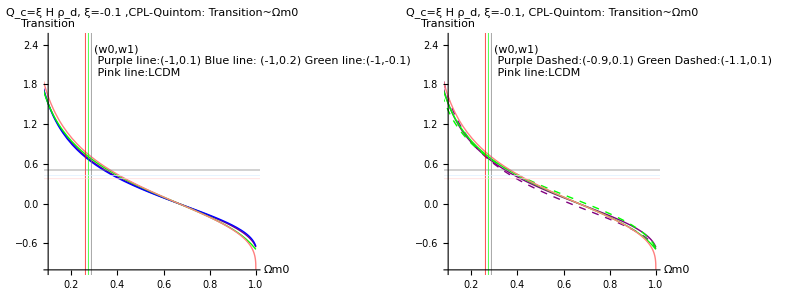

```mathematica
plztrI2CCPLQuintomSum=Grid[{{Show[{plztrI2CCPL[-0.1,-1,0.1,Purple,{0.1,1}],plztrI2CCPL[-0.1,-1,0.2,Blue,{0.1,1}],plztrI2CCPL[-0.1,-1,-0.1,Green,{0.1,1}],Plot[ztr[Ωm0I2CCPL,1-Ωm0I2CCPL],{Ωm0I2CCPL,0,1},PlotRange->{{0.1,1},{-1,3}},PlotStyle->Pink,AxesOrigin->{0.1,-1}]},GridLines->{{{0.261,Red},{0.274,Green},{0.287,Gray}},{{0.376,LightRed},{0.426,LightBlue},{0.508,Gray}}},AxesOrigin->{0.1,-1},PlotRange->{{0.1,1},{-1,2.5}},Frame->False,AxesLabel->{"Ωm0","Transition"},PlotLabel->"Q_c=ξ H ρ_d, ξ=-0.1 ,CPL-Quintom: Transition~Ωm0",Epilog->Inset[Framed[Style["(w0,w1)\n Purple line:(-1,0.1) Blue line: (-1,0.2) Green line:(-1,-0.1)\n Pink line:LCDM",10],Background->None,FrameStyle->None],{0.3,2.4},{Left,Top}],ImageSize->400],Show[{plztrI2CCPL[-0.1,-1,0.1,Purple,{0.1,1}],plztrI2CCPL[-0.1,-0.9,0.1,{Purple,Dashed},{0.1,1}],plztrI2CCPL[-0.1,-1,-0.1,Green,{0.1,1}],plztrI2CCPL[-0.1,-1.1,-0.1,{Green,Dashed},{0.1,1}],Plot[ztr[Ωm0I2CCPL,1-Ωm0I2CCPL],{Ωm0I2CCPL,0,1},PlotRange->{{0.1,1},{-1,3}},PlotStyle->Pink,AxesOrigin->{0.1,-1}]},GridLines->{{{0.261,Red},{0.274,Green},{0.287,Gray}},{{0.376,LightRed},{0.426,LightBlue},{0.508,Gray}}},AxesOrigin->{0.1,-1},PlotRange->{{0.1,1},{-1,2.5}},Frame->False,AxesLabel->{"Ωm0","Transition"},PlotLabel->"Q_c=ξ H ρ_d, ξ=-0.1, CPL-Quintom: Transition~Ωm0",Epilog->Inset[Framed[Style["(w0,w1)\n Purple Dashed:(-0.9,0.1) Green Dashed:(-1.1,0.1)\n Pink line:LCDM",10],Background->None,FrameStyle->None],{0.3,2.4},{Left,Top}],ImageSize->400]}}]//Quiet
```

As for the effect of EoS, we can split it to w0 effect and w1 effect.

First construct the plot function.

```mathematica
(*
pltξvw0I2CCPL[w1I2CCPL_,w0I2CCPLs_,w0I2CCPLe_]:=Plot[{ξI2CCPLfc[w0I2CCPL,w1I2CCPL],ξI2CCPLf1[w0I2CCPL,w1I2CCPL],ξI2CCPLf2[w0I2CCPL,w1I2CCPL]},{w0I2CCPL,w0I2CCPLs,w0I2CCPLe}]
*)
```

Choose the values from Reference 3. w0 = -1.087 ± 0.096,

```mathematica
ξvwExamI2CCPLQuintom={Block[{w0I2CCPL=-1,w1I2CCPL=-0.1},{{w0I2CCPL,w1I2CCPL},ξI2CCPLfc[w0I2CCPL,w1I2CCPL],ξI2CCPLf1[w0I2CCPL,w1I2CCPL],ξI2CCPLf2[w0I2CCPL,w1I2CCPL]}],Block[{w0I2CCPL=-1,w1I2CCPL=0},{{w0I2CCPL,w1I2CCPL},ξI2CCPLfc[w0I2CCPL,w1I2CCPL],ξI2CCPLf1[w0I2CCPL,w1I2CCPL],ξI2CCPLf2[w0I2CCPL,w1I2CCPL]}],Block[{w0I2CCPL=-1,w1I2CCPL=0.1},{{w0I2CCPL,w1I2CCPL},ξI2CCPLfc[w0I2CCPL,w1I2CCPL],ξI2CCPLf1[w0I2CCPL,w1I2CCPL],ξI2CCPLf2[w0I2CCPL,w1I2CCPL]}],Block[{w0I2CCPL=-0.9,w1I2CCPL=0.1},{{w0I2CCPL,w1I2CCPL},ξI2CCPLfc[w0I2CCPL,w1I2CCPL],ξI2CCPLf1[w0I2CCPL,w1I2CCPL],ξI2CCPLf2[w0I2CCPL,w1I2CCPL]}],Block[{w0I2CCPL=-1.1,w1I2CCPL=-0.1},{{w0I2CCPL,w1I2CCPL},ξI2CCPLfc[w0I2CCPL,w1I2CCPL],ξI2CCPLf1[w0I2CCPL,w1I2CCPL],ξI2CCPLf2[w0I2CCPL,w1I2CCPL]}]}
```

NIntegrate::inumr: The integrand ⅇ^0.3  - 0.3/1 + tmp\ (1 + tmp)^-4.3 + ξI2CCPL
 has evaluated to non-numerical values for all sampling points in the region with boundaries {{0, 3.}}.

NIntegrate::inumr: The integrand ⅇ^0.3  - 0.3/1.  + tmp\ (1.  + tmp)^-4.3 + ξI2CCPL
 has evaluated to non-numerical values for all sampling points in the region with boundaries {{0., 3.}}.

General::stop: Further output of NIntegrate :: inumr will be suppressed during this calculation.

FindRoot::nlnum: The function value {17.536  - 2.02294\ 4.^-0.3 + ξI2CCPL - 17.536\ ξI2CCPL\ NIntegrate[Exp[0.3  + Times[« 2 »]]\ (1.  + tmp)^-4.3 + ξI2CCPL, {tmp, 0., 3.}]}
 is not a list of numbers with dimensions {1} at {z} = {3.}.

ReplaceAll::reps: {FindRoot[(1 + 3\ Plus[« 2 »])\ ΩdI2CCPL[0.726, -1, -0.1, ξI2CCPL, z] + ΩmI2CCPLtest[0.726, 0.274, -1, -0.1, ξI2CCPL, z] == 0, {z, 3}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

FindRoot::nlnum: The function value {16.704  - 2.05916\ 4.^-0.3 + ξI2CCPL - 16.704\ ξI2CCPL\ NIntegrate[Exp[0.3  + Times[« 2 »]]\ (1.  + tmp)^-4.3 + ξI2CCPL, {tmp, 0., 3.}]}
 is not a list of numbers with dimensions {1} at {z} = {3.}.

ReplaceAll::reps: {FindRoot[(1 + 3\ Plus[« 2 »])\ ΩdI2CCPL[0.739, -1, -0.1, ξI2CCPL, z] + ΩmI2CCPLtest[0.739, 0.261, -1, -0.1, ξI2CCPL, z] == 0, {z, 3}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

FindRoot::nlnum: The function value {18.368  - 1.98672\ 4.^-0.3 + ξI2CCPL - 18.368\ ξI2CCPL\ NIntegrate[Exp[0.3  + Times[« 2 »]]\ (1.  + tmp)^-4.3 + ξI2CCPL, {tmp, 0., 3.}]}
 is not a list of numbers with dimensions {1} at {z} = {3.}.

General::stop: Further output of FindRoot :: nlnum will be suppressed during this calculation.

ReplaceAll::reps: {FindRoot[(1 + 3\ Plus[« 2 »])\ ΩdI2CCPL[0.713, -1, -0.1, ξI2CCPL, z] + ΩmI2CCPLtest[0.713, 0.287, -1, -0.1, ξI2CCPL, z] == 0, {z, 3}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

{{{-1,-0.1},-1.21004,-1.73137,-0.653393},{{-1,0},-1.15265,-1.66715,-0.605615},{{-1,0.1},-1.09155,-1.59939,-0.553918},{{-0.9,0.1},-0.94736,-1.40905,-0.463859},{{-1.1,-0.1},-1.28331,-1.84354,-0.680925}}

```mathematica
tabξvwExamI2CCPLQuintom=Grid[Prepend[Prepend[ξvwExamI2CCPLQuintom,{"{w0,w1}","Center","Lower","Upper"}],{"ξ results for Q_c=ξ H ρ_d, CPL,Quintom.",SpanFromLeft}],Frame->All,Background->{{LightGray,None},{LightGreen,LightGray,None}},Alignment->Center,ItemSize->8]
```

ξ results for Q_c=ξ H ρ_d, CPL,Quintom. |  |  | 
{w0,w1} | Center | Lower | Upper
{-1,-0.1} | -1.21004 | -1.73137 | -0.653393
{-1,0} | -1.15265 | -1.66715 | -0.605615
{-1,0.1} | -1.09155 | -1.59939 | -0.553918
{-0.9,0.1} | -0.94736 | -1.40905 | -0.463859
{-1.1,-0.1} | -1.28331 | -1.84354 | -0.680925

```mathematica
pltfitξI2CCPLfunc[w0I2CCPL_,w1I2CCPL_]:=Grid[{{numPlot["(",{ξI2CCPLf1[w0I2CCPL,w1I2CCPL],ξI2CCPLfc[w0I2CCPL,w1I2CCPL],ξI2CCPLf2[w0I2CCPL,w1I2CCPL]},")",{-2,1}]},{Plot[w0I2CCPL+w1I2CCPL temp/(temp+1),{temp,-0.9,10},Epilog->Inset[Framed[Style[{w0I2CCPL,w1I2CCPL},10],Background->LightYellow],{Center,Center},{Center,Center}]]}}];
```

```mathematica
pltfitξI2CCPLQuintomSum=Grid[{{pltfitξI2CCPLfunc[-1,0.1],pltfitξI2CCPLfunc[-1,0.2],pltfitξI2CCPLfunc[-1,-0.1]},{pltfitξI2CCPLfunc[-0.9,0.1],pltfitξI2CCPLfunc[-1.1,-0.1]}}]
```

NIntegrate::inumr: The integrand ⅇ^-0.3 + 0.3/1 + tmp\ (1 + tmp)^-3.7 + ξI2CCPL has evaluated to non-numerical values for all sampling points in the region with boundaries {{0, 3.}}.

NIntegrate::inumr: The integrand ⅇ^-0.3 + 0.3/1.  + tmp\ (1.  + tmp)^-3.7 + ξI2CCPL
 has evaluated to non-numerical values for all sampling points in the region with boundaries {{0., 3.}}.

General::stop: Further output of NIntegrate :: inumr will be suppressed during this calculation.

FindRoot::nlnum: The function value {16.704  - 1.04743\ 4.^0.3  + ξI2CCPL - 16.704\ ξI2CCPL\ NIntegrate[Exp[-0.3 + Times[« 2 »]]\ (1.  + tmp)^-3.7 + ξI2CCPL, {tmp, 0., 3.}]}
 is not a list of numbers with dimensions {1} at {z} = {3.}.

ReplaceAll::reps: {FindRoot[(1 + 3\ Plus[« 2 »])\ ΩdI2CCPL[0.739, -1, 0.1, ξI2CCPL, z] + ΩmI2CCPLtest[0.739, 0.261, -1, 0.1, ξI2CCPL, z] == 0, {z, 3}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

FindRoot::nlnum: The function value {17.536  - 1.02901\ 4.^0.3  + ξI2CCPL - 17.536\ ξI2CCPL\ NIntegrate[Exp[-0.3 + Times[« 2 »]]\ (1.  + tmp)^-3.7 + ξI2CCPL, {tmp, 0., 3.}]}
 is not a list of numbers with dimensions {1} at {z} = {3.}.

ReplaceAll::reps: {FindRoot[(1 + 3\ Plus[« 2 »])\ ΩdI2CCPL[0.726, -1, 0.1, ξI2CCPL, z] + ΩmI2CCPLtest[0.726, 0.274, -1, 0.1, ξI2CCPL, z] == 0, {z, 3}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

FindRoot::nlnum: The function value {18.368  - 1.01058\ 4.^0.3  + ξI2CCPL - 18.368\ ξI2CCPL\ NIntegrate[Exp[-0.3 + Times[« 2 »]]\ (1.  + tmp)^-3.7 + ξI2CCPL, {tmp, 0., 3.}]}
 is not a list of numbers with dimensions {1} at {z} = {3.}.

General::stop: Further output of FindRoot :: nlnum will be suppressed during this calculation.

ReplaceAll::reps: {FindRoot[(1 + 3\ Plus[« 2 »])\ ΩdI2CCPL[0.713, -1, 0.1, ξI2CCPL, z] + ΩmI2CCPLtest[0.713, 0.287, -1, 0.1, ξI2CCPL, z] == 0, {z, 3}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- |

```mathematica
pltfitξvΩm0I2CCPLQuintomSum[w0I2CCPL_,w1I2CCPL_,color_,{Ωm0start_,Ωm0end_}]:=Plot[ξI2CCPLffunc[Ωm0I2CCPL,1-Ωm0I2CCPL,w0I2CCPL,w1I2CCPL,0.426],{Ωm0I2CCPL,Ωm0start,Ωm0end},PlotStyle->color,AxesLabel->{"Ωm0","ξ"}];
```

```mathematica
ξI2CCPLffunc[0.2,1-0.2,-1,0.1,0.426]//Timing//Quiet
```

{3.728,-1.9741}

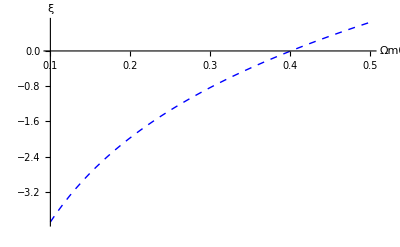
{551.042,-Graphics-}

```mathematica
pltfitξvΩm0I2CCPLQuintomSum[-1,0.1,{Blue,Dashed},{0.1,0.5}]//Quiet//Timing
```

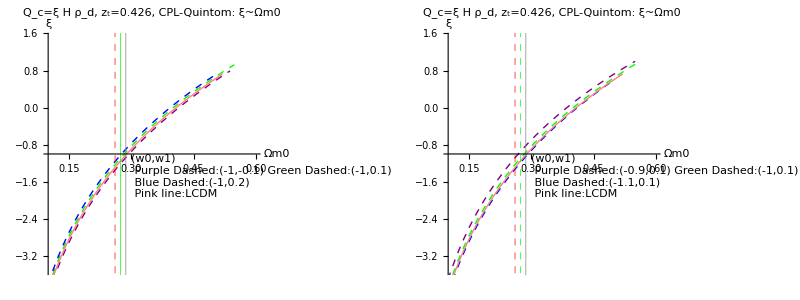

```mathematica
pltξvΩm0I2CCPLQuintomSum=Grid[{{Show[pltfitξvΩm0I2CCPLQuintomSum[-1,-0.1,{Purple,Dashed},{0.1,0.538}],pltfitξvΩm0I2CCPLQuintomSum[-1,0.1,{Green,Dashed},{0.1,0.548}],pltfitξvΩm0I2CCPLQuintomSum[-1,0.2,{Blue,Dashed},{0.1,0.51}],pltfitξvΩm0I2CCPLQuintomSum[-1,0,Pink,{0.1,0.52}],GridLines->{{{0.261,Directive[Red,Dashed]},{0.274,Green},{0.287,Gray}},{}},AxesOrigin->{0.1,-1},PlotRange->{{0.1,0.6},{-3.5,1.5}},Frame->False,AxesLabel->{"Ωm0","ξ"},PlotLabel->"Q_c=ξ H ρ_d, z_t=0.426, CPL-Quintom: ξ~Ωm0",Epilog->Inset[Framed[Style["(w0,w1)\n Purple Dashed:(-1,-0.1) Green Dashed:(-1,0.1)\n Blue Dashed:(-1,0.2)\n Pink line:LCDM",10],Background->None,FrameStyle->None],{0.3,-1},{Left,Top}],ImageSize->400],Show[pltfitξvΩm0I2CCPLQuintomSum[-0.9,0.1,{Purple,Dashed},{0.1,0.55}],pltfitξvΩm0I2CCPLQuintomSum[-1,0.1,{Green,Dashed},{0.1,0.55}],pltfitξvΩm0I2CCPLQuintomSum[-1.1,0.1,{Blue,Dashed},{0.1,0.489}],pltfitξvΩm0I2CCPLQuintomSum[-1,0,Pink,{0.1,0.52}],GridLines->{{{0.261,Directive[Red,Dashed]},{0.274,Directive[Green,Dashed]},{0.287,Gray}},{}},AxesOrigin->{0.1,-1},PlotRange->{{0.1,0.6},{-3.5,1.5}},Frame->False,AxesLabel->{"Ωm0","ξ"},PlotLabel->"Q_c=ξ H ρ_d, z_t=0.426, CPL-Quintom: ξ~Ωm0",Epilog->Inset[Framed[Style["(w0,w1)\n Purple Dashed:(-0.9,0.1) Green Dashed:(-1,0.1)\n Blue Dashed:(-1.1,0.1)\n Pink line:LCDM",10],Background->None,FrameStyle->None],{0.3,-1},{Left,Top}],ImageSize->400]}}]//Quiet
```

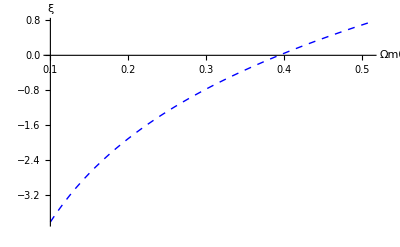
{612.974,-Graphics-}

```mathematica
pltfitξvΩm0I2CCPLQuintomSum[-1,0.2,{Blue,Dashed},{0.1,0.51}]//Timing//Quiet
```

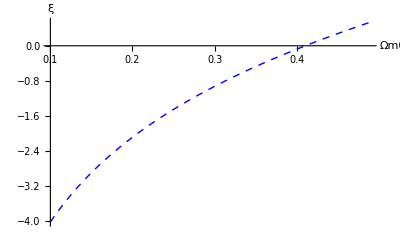
{393.341,-Graphics-}

```mathematica
pltfitξvΩm0I2CCPLQuintomSum[-1.1,0.1,{Blue,Dashed},{0.1,0.489}]//Timing//Quiet
```

```mathematica
tabw0vw1I2CCPL2=Table[{w0I2CCPLtemp,eosI2CCPLw1/.FindRoot[{ξI2CCffunc[0.274,1-0.274-0,w0I2CCPLtemp,eosI2CCPLw1]==0},{eosI2CCPLw1,-0.5}]},{w0I2CCPLtemp,-1.8,-0.5,0.01}];//Quiet//Timing
```

{175.907,Null}

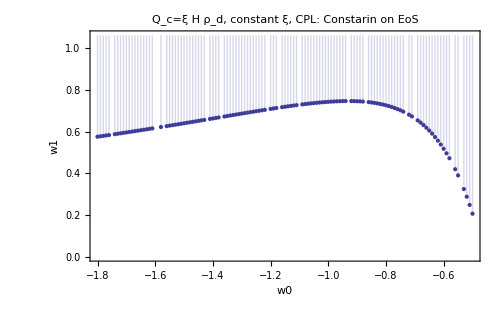

```mathematica
pltw0vw1ConsI2CCPL=ListPlot[tabw0vw1I2CCPL2,FrameLabel->{"w0","w1"},Filling->Top,Frame->True,PlotLabel->"Q_c=ξ H ρ_d, constant ξ, CPL: Constarin on EoS",ImageSize->500]
```

#### Quintessence

Choose some Quintessence parameters.
(-0.9,-0.05) (-0.8,-0.05)(-0.8,-0.1)

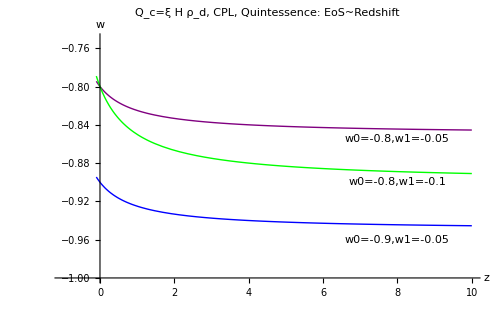

```mathematica
plEoSI2CCPLQuintessenceSum=Grid[{{Show[pltI2CCPLEoSfunc[-0.9,-0.05,Blue],pltI2CCPLEoSfunc[-0.8,-0.05,Purple],pltI2CCPLEoSfunc[-0.8,-0.1,Green],PlotRange->{{-0.99,10},{-1.0,-0.75}},AxesOrigin->{0,-1},Epilog->{Inset[Framed[Style["w0=-0.9,w1=-0.05",10,Blue],Background->None,FrameStyle->None],{8,-0.96},{0,0}],Inset[Framed[Style["w0=-0.8,w1=-0.05",10,Purple],Background->None,FrameStyle->None],{8,-0.855},{0,0}],Inset[Framed[Style["w0=-0.8,w1=-0.1",10,Green],Background->None,FrameStyle->None],{8,-0.9},{0,0}]},PlotLabel->"Q_c=ξ H ρ_d, CPL, Quintessence: EoS~Redshift",ImageSize->500]}}]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {-1.0027}. NIntegrate obtained 6.12819×10^93 - 1.20272×10^94\ ⅈ and 1.34985×10^94 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {-1.00216}. NIntegrate obtained 3.93838313043837×10^3757 - 7.72951210650262×10^3757\ ⅈ and 9.16137714372885×10^3757 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {-1.00205}. NIntegrate obtained 7.25839576488893×10^2124 - 1.42454037812851×10^2125\ ⅈ and 1.68843149227054×10^2125 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

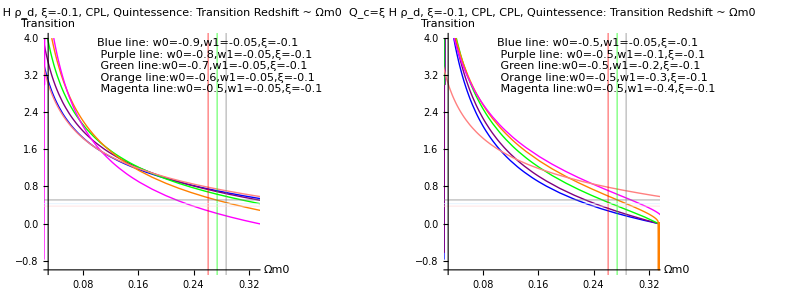

```mathematica
plztrI2CCPLQuintessenceSum=Grid[{{Show[{Plot[ztrI2CCPL[Ωm0I2CCPL,1-Ωm0I2CCPL,-0.1,-0.9,-0.05],{Ωm0I2CCPL,0.01,1},PlotRange->{{0,1},{-1,4}},PlotStyle->Blue,AxesOrigin->{0,-1},PerformanceGoal->"Quality"],Plot[ztrI2CCPL[Ωm0I2CCPL,1-Ωm0I2CCPL,-0.1,-0.8,-0.05],{Ωm0I2CCPL,0.01,1},PlotRange->{{0,1},{-1,4}},PlotStyle->Purple,AxesOrigin->{0,-1},PerformanceGoal->"Quality"],Plot[ztrI2CCPL[Ωm0I2CCPL,1-Ωm0I2CCPL,-0.1,-0.7,-0.05],{Ωm0I2CCPL,0.01,0.94},PlotRange->{{0,1},{-1,4}},PlotStyle->Green,AxesOrigin->{0,-1},PerformanceGoal->"Quality"],Plot[ztrI2CCPL[Ωm0I2CCPL,1-Ωm0I2CCPL,-0.1,-0.6,-0.05],{Ωm0I2CCPL,0.01,0.94},PlotRange->{{0,1},{-1,4}},PlotStyle->Orange,AxesOrigin->{0,-1},PerformanceGoal->"Quality"],Plot[ztrI2CCPL[Ωm0I2CCPL,1-Ωm0I2CCPL,-0.1,-0.5,-0.05],{Ωm0I2CCPL,0.01,0.94},PlotRange->{{0,1},{-1,4}},PlotStyle->Magenta,AxesOrigin->{0,-1},PerformanceGoal->"Quality"],Plot[ztr[Ωm0I2CCPL,1-Ωm0I2CCPL],{Ωm0I2CCPL,0,1},PlotRange->{{0.01,0.94},{-1,4}},PlotStyle->Pink,AxesOrigin->{0,-1}]},GridLines->{{{0.261,Red},{0.274,Green},{0.287,Gray}},{{0.376,LightRed},{0.426,LightBlue},{0.508,Gray}}},AxesOrigin->{0.03,-1},PlotRange->{{0.03,0.33},Automatic},Frame->False,AxesLabel->{"Ωm0","Transition"},Epilog->Inset[Framed[Style["Blue line: w0=-0.9,w1=-0.05,ξ=-0.1\n Purple line: w0=-0.8,w1=-0.05,ξ=-0.1\n Green line:w0=-0.7,w1=-0.05,ξ=-0.1\n Orange line:w0=-0.6,w1=-0.05,ξ=-0.1\n Magenta line:w0=-0.5,w1=-0.05,ξ=-0.1",10],Background->LightGreen,FrameStyle->None],{0.1,4},{Left,Top}],PlotLabel->"Q_c=ξ H ρ_d, ξ=-0.1, CPL, Quintessence: Transition Redshift ~ Ωm0",ImageSize->400],Show[{Plot[ztrI2CCPL[Ωm0I2CCPL,1-Ωm0I2CCPL,-0.1,-0.5,-0.05],{Ωm0I2CCPL,0.01,1},PlotRange->{{0,1},{-1,4}},PlotStyle->Blue,AxesOrigin->{0,-1},PerformanceGoal->"Quality"],Plot[ztrI2CCPL[Ωm0I2CCPL,1-Ωm0I2CCPL,-0.1,-0.5,-0.1],{Ωm0I2CCPL,0.01,1},PlotRange->{{0,1},{-1,4}},PlotStyle->Purple,AxesOrigin->{0,-1},PerformanceGoal->"Quality"],Plot[ztrI2CCPL[Ωm0I2CCPL,1-Ωm0I2CCPL,-0.1,-0.5,-0.2],{Ωm0I2CCPL,0.01,0.94},PlotRange->{{0,1},{-1,4}},PlotStyle->Green,AxesOrigin->{0,-1},PerformanceGoal->"Quality"],Plot[ztrI2CCPL[Ωm0I2CCPL,1-Ωm0I2CCPL,-0.1,-0.5,-0.3],{Ωm0I2CCPL,0.01,0.94},PlotRange->{{0,1},{-1,4}},PlotStyle->Orange,AxesOrigin->{0,-1},PerformanceGoal->"Quality"],Plot[ztrI2CCPL[Ωm0I2CCPL,1-Ωm0I2CCPL,-0.1,-0.5,-0.4],{Ωm0I2CCPL,0.01,0.94},PlotRange->{{0,1},{-1,4}},PlotStyle->Magenta,AxesOrigin->{0,-1},PerformanceGoal->"Quality"],Plot[ztr[Ωm0I2CCPL,1-Ωm0I2CCPL],{Ωm0I2CCPL,0,1},PlotRange->{{0.01,0.94},{-1,4}},PlotStyle->Pink,AxesOrigin->{0,-1}]},GridLines->{{{0.261,Red},{0.274,Green},{0.287,Gray}},{{0.376,LightRed},{0.426,LightBlue},{0.508,Gray}}},AxesOrigin->{0.03,-1},PlotRange->{{0.03,0.33},Automatic},Frame->False,AxesLabel->{"Ωm0","Transition"},Epilog->Inset[Framed[Style["Blue line: w0=-0.5,w1=-0.05,ξ=-0.1\n Purple line: w0=-0.5,w1=-0.1,ξ=-0.1\n Green line:w0=-0.5,w1=-0.2,ξ=-0.1\n Orange line:w0=-0.5,w1=-0.3,ξ=-0.1\n Magenta line:w0=-0.5,w1=-0.4,ξ=-0.1",10],Background->LightGreen,FrameStyle->None],{0.1,4},{Left,Top}],PlotLabel->"Q_c=ξ H ρ_d, ξ=-0.1, CPL, CPL, Quintessence: Transition Redshift ~ Ωm0",ImageSize->400]}}]
```

As for the effect of EoS, we can split it to w0 effect and w1 effect.

Choose some values of w0 and w1 causually.

```mathematica
ξvwExamI2CCPLQuintessence={Block[{w0I2CCPL=-0.9,w1I2CCPL=-0.05},{{w0I2CCPL,w1I2CCPL},ξI2CCPLfc[w0I2CCPL,w1I2CCPL],ξI2CCPLf1[w0I2CCPL,w1I2CCPL],ξI2CCPLf2[w0I2CCPL,w1I2CCPL]}],Block[{w0I2CCPL=-0.8,w1I2CCPL=-0.05},{{w0I2CCPL,w1I2CCPL},ξI2CCPLfc[w0I2CCPL,w1I2CCPL],ξI2CCPLf1[w0I2CCPL,w1I2CCPL],ξI2CCPLf2[w0I2CCPL,w1I2CCPL]}],Block[{w0I2CCPL=-0.8,w1I2CCPL=-0.1},{{w0I2CCPL,w1I2CCPL},ξI2CCPLfc[w0I2CCPL,w1I2CCPL],ξI2CCPLf1[w0I2CCPL,w1I2CCPL],ξI2CCPLf2[w0I2CCPL,w1I2CCPL]}]}
```

NIntegrate::inumr: The integrand ⅇ^0.15  - 0.15/1 + tmp\ (1 + tmp)^-3.85 + ξI2CCPL
 has evaluated to non-numerical values for all sampling points in the region with boundaries {{0, 3.}}.

NIntegrate::inumr: The integrand ⅇ^0.15  - 0.15/1.  + tmp\ (1.  + tmp)^-3.85 + ξI2CCPL
 has evaluated to non-numerical values for all sampling points in the region with boundaries {{0., 3.}}.

General::stop: Further output of NIntegrate :: inumr will be suppressed during this calculation.

FindRoot::nlnum: The function value {17.536  - 1.47256\ 4.^0.15  + ξI2CCPL - 17.536\ ξI2CCPL\ NIntegrate[Exp[0.15  + Times[« 2 »]]\ (1.  + tmp)^-3.85 + ξI2CCPL, {tmp, 0., 3.}]}
 is not a list of numbers with dimensions {1} at {z} = {3.}.

ReplaceAll::reps: {FindRoot[(1 + 3\ Plus[« 2 »])\ ΩdI2CCPL[0.726, -0.9, -0.05, ξI2CCPL, z] + ΩmI2CCPLtest[0.726, 0.274, -0.9, -0.05, ξI2CCPL, z] == 0, {z, 3}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

FindRoot::nlnum: The function value {16.704  - 1.49893\ 4.^0.15  + ξI2CCPL - 16.704\ ξI2CCPL\ NIntegrate[Exp[0.15  + Times[« 2 »]]\ (1.  + tmp)^-3.85 + ξI2CCPL, {tmp, 0., 3.}]}
 is not a list of numbers with dimensions {1} at {z} = {3.}.

ReplaceAll::reps: {FindRoot[(1 + 3\ Plus[« 2 »])\ ΩdI2CCPL[0.739, -0.9, -0.05, ξI2CCPL, z] + ΩmI2CCPLtest[0.739, 0.261, -0.9, -0.05, ξI2CCPL, z] == 0, {z, 3}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

FindRoot::nlnum: The function value {18.368  - 1.44619\ 4.^0.15  + ξI2CCPL - 18.368\ ξI2CCPL\ NIntegrate[Exp[0.15  + Times[« 2 »]]\ (1.  + tmp)^-3.85 + ξI2CCPL, {tmp, 0., 3.}]}
 is not a list of numbers with dimensions {1} at {z} = {3.}.

General::stop: Further output of FindRoot :: nlnum will be suppressed during this calculation.

ReplaceAll::reps: {FindRoot[(1 + 3\ Plus[« 2 »])\ ΩdI2CCPL[0.713, -0.9, -0.05, ξI2CCPL, z] + ΩmI2CCPLtest[0.713, 0.287, -0.9, -0.05, ξI2CCPL, z] == 0, {z, 3}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

{{{-0.9,-0.05},-1.05994,-1.53267,-0.561052},{{-0.8,-0.05},-0.881934,-1.30148,-0.445082},{{-0.8,-0.1},-0.926183,-1.35,-0.483467}}

```mathematica
tabξvwExamI2CCPLQuintessence=Grid[Prepend[Prepend[ξvwExamI2CCPLQuintessence,{"{w0,w1}","Center","Lower","Upper"}],{"ξ results for Q_c=ξ H ρ_d, CPL,Quintessence.",SpanFromLeft}],Frame->All,Background->{{LightGray,None},{LightGreen,LightGray,None}},Alignment->Center,ItemSize->8]
```

ξ results for Q_c=ξ H ρ_d, CPL,Quintessence. |  |  | 
{w0,w1} | Center | Lower | Upper
{-0.9,-0.05} | -1.05994 | -1.53267 | -0.561052
{-0.8,-0.05} | -0.881934 | -1.30148 | -0.445082
{-0.8,-0.1} | -0.926183 | -1.35 | -0.483467

```mathematica
pltfitξI2CCPLQuintessenceSum=Grid[{{pltfitξI2CCPLfunc[-0.9,-0.05],pltfitξI2CCPLfunc[-0.8,-0.05],pltfitξI2CCPLfunc[-0.8,-0.1]}}]
```

NIntegrate::inumr: The integrand ⅇ^0.15  - 0.15/1 + tmp\ (1 + tmp)^-3.85 + ξI2CCPL
 has evaluated to non-numerical values for all sampling points in the region with boundaries {{0, 3.}}.

NIntegrate::inumr: The integrand ⅇ^0.15  - 0.15/1.  + tmp\ (1.  + tmp)^-3.85 + ξI2CCPL
 has evaluated to non-numerical values for all sampling points in the region with boundaries {{0., 3.}}.

General::stop: Further output of NIntegrate :: inumr will be suppressed during this calculation.

FindRoot::nlnum: The function value {16.704  - 1.49893\ 4.^0.15  + ξI2CCPL - 16.704\ ξI2CCPL\ NIntegrate[Exp[0.15  + Times[« 2 »]]\ (1.  + tmp)^-3.85 + ξI2CCPL, {tmp, 0., 3.}]}
 is not a list of numbers with dimensions {1} at {z} = {3.}.

ReplaceAll::reps: {FindRoot[(1 + 3\ Plus[« 2 »])\ ΩdI2CCPL[0.739, -0.9, -0.05, ξI2CCPL, z] + ΩmI2CCPLtest[0.739, 0.261, -0.9, -0.05, ξI2CCPL, z] == 0, {z, 3}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

FindRoot::nlnum: The function value {17.536  - 1.47256\ 4.^0.15  + ξI2CCPL - 17.536\ ξI2CCPL\ NIntegrate[Exp[0.15  + Times[« 2 »]]\ (1.  + tmp)^-3.85 + ξI2CCPL, {tmp, 0., 3.}]}
 is not a list of numbers with dimensions {1} at {z} = {3.}.

ReplaceAll::reps: {FindRoot[(1 + 3\ Plus[« 2 »])\ ΩdI2CCPL[0.726, -0.9, -0.05, ξI2CCPL, z] + ΩmI2CCPLtest[0.726, 0.274, -0.9, -0.05, ξI2CCPL, z] == 0, {z, 3}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

FindRoot::nlnum: The function value {18.368  - 1.44619\ 4.^0.15  + ξI2CCPL - 18.368\ ξI2CCPL\ NIntegrate[Exp[0.15  + Times[« 2 »]]\ (1.  + tmp)^-3.85 + ξI2CCPL, {tmp, 0., 3.}]}
 is not a list of numbers with dimensions {1} at {z} = {3.}.

General::stop: Further output of FindRoot :: nlnum will be suppressed during this calculation.

ReplaceAll::reps: {FindRoot[(1 + 3\ Plus[« 2 »])\ ΩdI2CCPL[0.713, -0.9, -0.05, ξI2CCPL, z] + ΩmI2CCPLtest[0.713, 0.287, -0.9, -0.05, ξI2CCPL, z] == 0, {z, 3}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

-Graphics- | -Graphics- | -Graphics-

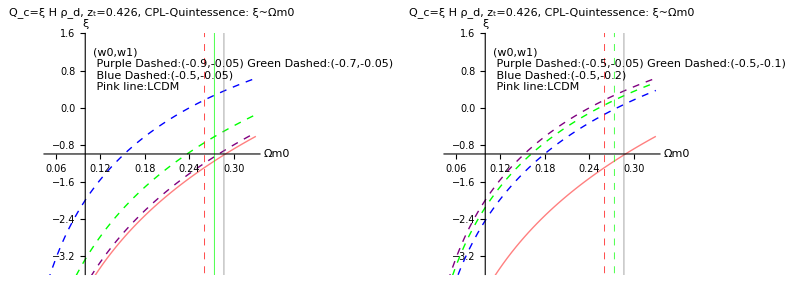

```mathematica
pltξvΩm0I2CCPLQuintessenceSum=Grid[{{Show[pltfitξvΩm0I2CCPLQuintomSum[-0.9,-0.05,{Purple,Dashed},{0.05,0.33}],pltfitξvΩm0I2CCPLQuintomSum[-0.7,-0.05,{Green,Dashed},{0.05,0.33}],pltfitξvΩm0I2CCPLQuintomSum[-0.5,-0.05,{Blue,Dashed},{0.05,0.33}],pltfitξvΩm0I2CCPLQuintomSum[-1,0,Pink,{0.05,0.33}],GridLines->{{{0.261,Directive[Red,Dashed]},{0.274,Green},{0.287,Gray}},{}},AxesOrigin->{0.1,-1},PlotRange->{{0.05,0.33},{-3.5,1.5}},Frame->False,AxesLabel->{"Ωm0","ξ"},PlotLabel->"Q_c=ξ H ρ_d, z_t=0.426, CPL-Quintessence: ξ~Ωm0",Epilog->Inset[Framed[Style["(w0,w1)\n Purple Dashed:(-0.9,-0.05) Green Dashed:(-0.7,-0.05)\n Blue Dashed:(-0.5,-0.05)\n Pink line:LCDM",10],Background->None,FrameStyle->None],{0.11,1.3},{Left,Top}],ImageSize->400],Show[pltfitξvΩm0I2CCPLQuintomSum[-0.5,-0.05,{Purple,Dashed},{0.05,0.33}],pltfitξvΩm0I2CCPLQuintomSum[-0.5,-0.1,{Green,Dashed},{0.05,0.33}],pltfitξvΩm0I2CCPLQuintomSum[-0.5,-0.2,{Blue,Dashed},{0.05,0.33}],pltfitξvΩm0I2CCPLQuintomSum[-1,0,Pink,{0.05,0.33}],GridLines->{{{0.261,Directive[Red,Dashed]},{0.274,Directive[Green,Dashed]},{0.287,Gray}},{}},AxesOrigin->{0.1,-1},PlotRange->{{0.05,0.33},{-3.5,1.5}},Frame->False,AxesLabel->{"Ωm0","ξ"},PlotLabel->"Q_c=ξ H ρ_d, z_t=0.426, CPL-Quintessence: ξ~Ωm0",Epilog->Inset[Framed[Style["(w0,w1)\n Purple Dashed:(-0.5,-0.05) Green Dashed:(-0.5,-0.1)\n Blue Dashed:(-0.5,-0.2)\n Pink line:LCDM",10],Background->None,FrameStyle->None],{0.11,1.3},{Left,Top}],ImageSize->400]}}]//Quiet
```

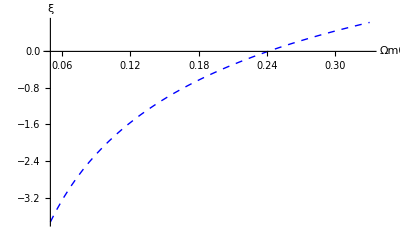
{537.33,-Graphics-}

```mathematica
pltfitξvΩm0I2CCPLQuintomSum[-0.5,-0.05,{Blue,Dashed},{0.05,0.33}]//Timing//Quiet
```

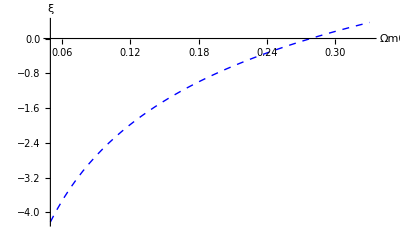
{442.653,-Graphics-}

```mathematica
pltfitξvΩm0I2CCPLQuintomSum[-0.5,-0.2,{Blue,Dashed},{0.05,0.33}]//Timing//Quiet
```

#### Phantom

Some parameters that give us a phantom mode
(-1.1,0.05) (-1.2,0.05) (-1.2,0.1)

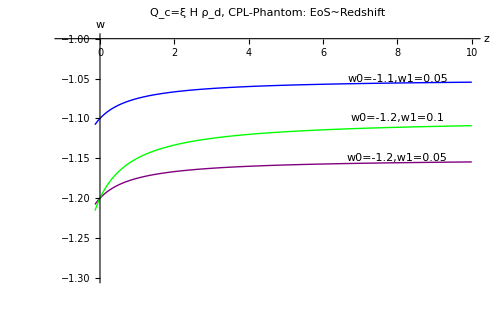

```mathematica
plEoSI2CCPLPhantomSum=Grid[{{Show[pltI2CCPLEoSfunc[-1.1,0.05,Blue],pltI2CCPLEoSfunc[-1.2,0.05,Purple],pltI2CCPLEoSfunc[-1.2,0.1,Green],PlotRange->{{-0.99,10},{-1.3,-1}},AxesOrigin->{0,-1},Epilog->{Inset[Framed[Style["w0=-1.1,w1=0.05",10,Blue],Background->None,FrameStyle->None],{8,-1.05},{0,0}],Inset[Framed[Style["w0=-1.2,w1=0.05",10,Purple],Background->None,FrameStyle->None],{8,-1.15},{0,0}],Inset[Framed[Style["w0=-1.2,w1=0.1",10,Green],Background->None,FrameStyle->None],{8,-1.1},{0,0}]},PlotLabel->"Q_c=ξ H ρ_d, CPL-Phantom: EoS~Redshift",ImageSize->500]}}]
```

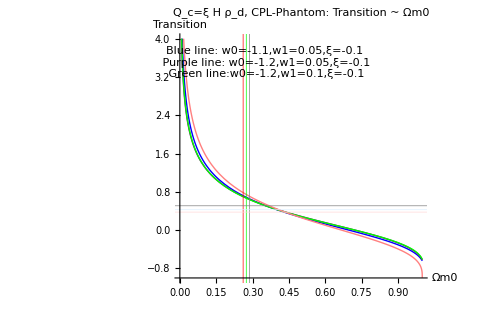

```mathematica
plztrI2CCPLPhantomSum=Grid[{{Show[{plztrI2CCPL[-0.1,-1.1,0.05,Blue,{0,1}],plztrI2CCPL[-0.1,-1.2,0.05,Purple,{0,1}],plztrI2CCPL[-0.1,-1.2,0.1,Green,{0,1}],Plot[ztr[Ωm0I2CCPL,1-Ωm0I2CCPL],{Ωm0I2CCPL,0,1},PlotRange->{{0,1},{-1,4}},PlotStyle->Pink,AxesOrigin->{0,-1}]},GridLines->{{{0.261,Red},{0.274,Green},{0.287,Gray}},{{0.376,LightRed},{0.426,LightBlue},{0.508,Gray}}},AxesOrigin->{0,-1},Frame->False,AxesLabel->{"Ωm0","Transition"},Epilog->Inset[Framed[Style["Blue line: w0=-1.1,w1=0.05,ξ=-0.1\n Purple line: w0=-1.2,w1=0.05,ξ=-0.1\n Green line:w0=-1.2,w1=0.1,ξ=-0.1",10],Background->LightGreen,FrameStyle->None],{0.35,3.5},{0,0}],PlotLabel->"Q_c=ξ H ρ_d, CPL-Phantom: Transition ~ Ωm0",ImageSize->500]}}]
```

As for the effect of EoS, we can split it to w0 effect and w1 effect.

Choose some values of w0 and w1 causually.

```mathematica
ξvwExamI2CCPLPhantom={Block[{w0I2CCPL=-1.1,w1I2CCPL=0.05},{{w0I2CCPL,w1I2CCPL},ξI2CCPLfc[w0I2CCPL,w1I2CCPL],ξI2CCPLf1[w0I2CCPL,w1I2CCPL],ξI2CCPLf2[w0I2CCPL,w1I2CCPL]}],Block[{w0I2CCPL=-1.2,w1I2CCPL=0.05},{{w0I2CCPL,w1I2CCPL},ξI2CCPLfc[w0I2CCPL,w1I2CCPL],ξI2CCPLf1[w0I2CCPL,w1I2CCPL],ξI2CCPLf2[w0I2CCPL,w1I2CCPL]}],Block[{w0I2CCPL=-1.2,w1I2CCPL=0.1},{{w0I2CCPL,w1I2CCPL},ξI2CCPLfc[w0I2CCPL,w1I2CCPL],ξI2CCPLf1[w0I2CCPL,w1I2CCPL],ξI2CCPLf2[w0I2CCPL,w1I2CCPL]}]}
```

NIntegrate::inumr: The integrand ⅇ^-0.15 + 0.15/1 + tmp\ (1 + tmp)^-4.15 + ξI2CCPL has evaluated to non-numerical values for all sampling points in the region with boundaries {{0, 3.}}.

NIntegrate::inumr: The integrand ⅇ^-0.15 + 0.15/1.  + tmp\ (1.  + tmp)^-4.15 + ξI2CCPL
 has evaluated to non-numerical values for all sampling points in the region with boundaries {{0., 3.}}.

General::stop: Further output of NIntegrate :: inumr will be suppressed during this calculation.

FindRoot::nlnum: The function value {17.536  - 1.41914\ 4.^-0.15 + ξI2CCPL - 17.536\ ξI2CCPL\ NIntegrate[Exp[-0.15 + Times[« 2 »]]\ (1.  + tmp)^-4.15 + ξI2CCPL, {tmp, 0., 3.}]}
 is not a list of numbers with dimensions {1} at {z} = {3.}.

ReplaceAll::reps: {FindRoot[(1 + 3\ Plus[« 2 »])\ ΩdI2CCPL[0.726, -1.1, 0.05, ξI2CCPL, z] + ΩmI2CCPLtest[0.726, 0.274, -1.1, 0.05, ξI2CCPL, z] == 0, {z, 3}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

FindRoot::nlnum: The function value {16.704  - 1.44456\ 4.^-0.15 + ξI2CCPL - 16.704\ ξI2CCPL\ NIntegrate[Exp[-0.15 + Times[« 2 »]]\ (1.  + tmp)^-4.15 + ξI2CCPL, {tmp, 0., 3.}]}
 is not a list of numbers with dimensions {1} at {z} = {3.}.

ReplaceAll::reps: {FindRoot[(1 + 3\ Plus[« 2 »])\ ΩdI2CCPL[0.739, -1.1, 0.05, ξI2CCPL, z] + ΩmI2CCPLtest[0.739, 0.261, -1.1, 0.05, ξI2CCPL, z] == 0, {z, 3}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

FindRoot::nlnum: The function value {18.368  - 1.39373\ 4.^-0.15 + ξI2CCPL - 18.368\ ξI2CCPL\ NIntegrate[Exp[-0.15 + Times[« 2 »]]\ (1.  + tmp)^-4.15 + ξI2CCPL, {tmp, 0., 3.}]}
 is not a list of numbers with dimensions {1} at {z} = {3.}.

General::stop: Further output of FindRoot :: nlnum will be suppressed during this calculation.

ReplaceAll::reps: {FindRoot[(1 + 3\ Plus[« 2 »])\ ΩdI2CCPL[0.713, -1.1, 0.05, ξI2CCPL, z] + ΩmI2CCPLtest[0.713, 0.287, -1.1, 0.05, ξI2CCPL, z] == 0, {z, 3}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

{{{-1.1,0.05},-1.21257,-1.76337,-0.623591},{{-1.2,0.05},-1.266,-1.8517,-0.635863},{{-1.2,0.1},-1.24569,-1.82849,-0.619702}}

```mathematica
tabξvwExamI2CCPLPhantom=Grid[Prepend[Prepend[ξvwExamI2CCPLPhantom,{"{w0,w1}","Center","Lower","Upper"}],{"ξ results for Q_c=ξ H ρ_d, CPL,Phantom.",SpanFromLeft}],Frame->All,Background->{{LightGray,None},{LightGreen,LightGray,None}},Alignment->Center,ItemSize->8]
```

ξ results for Q_c=ξ H ρ_d, CPL,Phantom. |  |  | 
{w0,w1} | Center | Lower | Upper
{-1.1,0.05} | -1.21257 | -1.76337 | -0.623591
{-1.2,0.05} | -1.266 | -1.8517 | -0.635863
{-1.2,0.1} | -1.24569 | -1.82849 | -0.619702

```mathematica
pltfitξI2CCPLPhantomSum=Grid[{{pltfitξI2CCPLfunc[-1.1,0.05],pltfitξI2CCPLfunc[-1.2,0.05],pltfitξI2CCPLfunc[-1.2,0.1]}}]
```

NIntegrate::inumr: The integrand ⅇ^-0.15 + 0.15/1 + tmp\ (1 + tmp)^-4.15 + ξI2CCPL has evaluated to non-numerical values for all sampling points in the region with boundaries {{0, 3.}}.

NIntegrate::inumr: The integrand ⅇ^-0.15 + 0.15/1.  + tmp\ (1.  + tmp)^-4.15 + ξI2CCPL
 has evaluated to non-numerical values for all sampling points in the region with boundaries {{0., 3.}}.

General::stop: Further output of NIntegrate :: inumr will be suppressed during this calculation.

FindRoot::nlnum: The function value {16.704  - 1.44456\ 4.^-0.15 + ξI2CCPL - 16.704\ ξI2CCPL\ NIntegrate[Exp[-0.15 + Times[« 2 »]]\ (1.  + tmp)^-4.15 + ξI2CCPL, {tmp, 0., 3.}]}
 is not a list of numbers with dimensions {1} at {z} = {3.}.

ReplaceAll::reps: {FindRoot[(1 + 3\ Plus[« 2 »])\ ΩdI2CCPL[0.739, -1.1, 0.05, ξI2CCPL, z] + ΩmI2CCPLtest[0.739, 0.261, -1.1, 0.05, ξI2CCPL, z] == 0, {z, 3}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

FindRoot::nlnum: The function value {17.536  - 1.41914\ 4.^-0.15 + ξI2CCPL - 17.536\ ξI2CCPL\ NIntegrate[Exp[-0.15 + Times[« 2 »]]\ (1.  + tmp)^-4.15 + ξI2CCPL, {tmp, 0., 3.}]}
 is not a list of numbers with dimensions {1} at {z} = {3.}.

ReplaceAll::reps: {FindRoot[(1 + 3\ Plus[« 2 »])\ ΩdI2CCPL[0.726, -1.1, 0.05, ξI2CCPL, z] + ΩmI2CCPLtest[0.726, 0.274, -1.1, 0.05, ξI2CCPL, z] == 0, {z, 3}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

FindRoot::nlnum: The function value {18.368  - 1.39373\ 4.^-0.15 + ξI2CCPL - 18.368\ ξI2CCPL\ NIntegrate[Exp[-0.15 + Times[« 2 »]]\ (1.  + tmp)^-4.15 + ξI2CCPL, {tmp, 0., 3.}]}
 is not a list of numbers with dimensions {1} at {z} = {3.}.

General::stop: Further output of FindRoot :: nlnum will be suppressed during this calculation.

ReplaceAll::reps: {FindRoot[(1 + 3\ Plus[« 2 »])\ ΩdI2CCPL[0.713, -1.1, 0.05, ξI2CCPL, z] + ΩmI2CCPLtest[0.713, 0.287, -1.1, 0.05, ξI2CCPL, z] == 0, {z, 3}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

-Graphics- | -Graphics- | -Graphics-

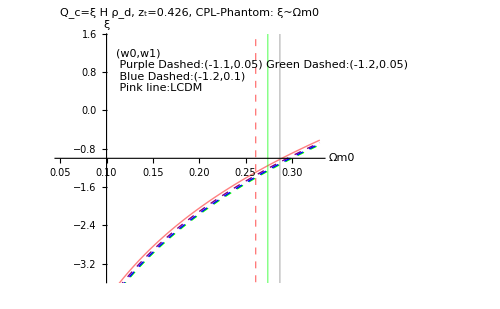

```mathematica
pltξvΩm0I2CCPLPhantomSum=Show[pltfitξvΩm0I2CCPLQuintomSum[-1.1,0.05,{Purple,Dashed},{0.05,0.33}],pltfitξvΩm0I2CCPLQuintomSum[-1.2,0.05,{Green,Dashed},{0.05,0.33}],pltfitξvΩm0I2CCPLQuintomSum[-1.2,0.1,{Blue,Dashed},{0.05,0.33}],pltfitξvΩm0I2CCPLQuintomSum[-1,0,Pink,{0.05,0.33}],GridLines->{{{0.261,Directive[Red,Dashed]},{0.274,Green},{0.287,Gray}},{}},AxesOrigin->{0.1,-1},PlotRange->{{0.05,0.33},{-3.5,1.5}},Frame->False,AxesLabel->{"Ωm0","ξ"},PlotLabel->"Q_c=ξ H ρ_d, z_t=0.426, CPL-Phantom: ξ~Ωm0",Epilog->Inset[Framed[Style["(w0,w1)\n Purple Dashed:(-1.1,0.05) Green Dashed:(-1.2,0.05)\n Blue Dashed:(-1.2,0.1)\n Pink line:LCDM",10],Background->None,FrameStyle->None],{0.11,1.3},{Left,Top}],ImageSize->500]//Quiet
```

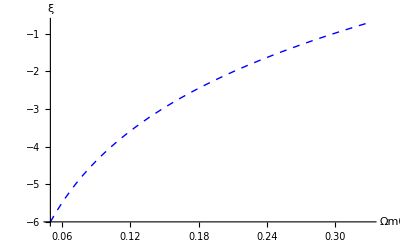
{273.189,-Graphics-}

```mathematica
pltfitξvΩm0I2CCPLQuintomSum[-1.2,0.1,{Blue,Dashed},{0.05,0.33}]//Timing//Quiet
```

## Summary

### Interacting models

#### List of what to make clear

[Quantitively] Fixed Ωm0, the allowed ξ with a changing of EoS.

[Quantitively] Fixed ω, the allowed ξ with a change Ωm0 or r.

[Quantitively] ξ is positive means energy transfer to dark matter, which delays the appearence of dark energy dominated era. What is the result of this method.

[Quantitively] CPL parameterization can be categorized into 3 cases. Check their effects on the fitting. How do different category change the ξ fitting results.

Phantom

Quintessence

Crossing -1, Quintom

[Quantitively] The effect of Ωm0 in different CPL parameterizations.

#### BASIC

Evolution of energy density for Q_c=ξ H ρ_c, constant ξ, constant w, and ξ≠-3w

Ωm=Ωm0 (1+z)^(3-ξ)

Ωd=(Ωd0+ξ/(3w+ξ)Ωm0)(1+z)^(3(1+w))+-ξ/(3w+ξ)Ωm≡Ωd0'(1+z)^(3(1+w))+-ξ/(3w+ξ)Ωm

Evolution of energy density for Q_c=ξ H ρ_d, constant ξ, constant w, and ξ≠-3w

Ωm=(Ωm0+ξ/(ξ+3w)Ωd0)(1+z)^3+-ξ/(ξ+3w)Ωd≡Ωm0'(1+z)^3+-ξ/(ξ+3w)Ωd

Ωd=Ωd0(1+z)^(3(1+w)+ξ)

So in the two cases, coupling constant has two effects:

Amplifies the curve of deceleration parameter.

Energy flow between DE and DM.

### Interacting model Q_c=ξ H ρ_c with constant ξ and constant EoS w.

Derived from (transition redshift, Ωm0) plane, the allowed region for coupling constant ξ is  (-1.28, -0.46) with a center at -0.88, i.e., -0.88_-0.40^(+0.42),  taken the case that the universe is flat, and choose the EoS parameter {w=-1}.
Derived from the (transition redshift, Ωm0/Ωd0) plane, the allowed region of coupling constant ξ is  (-1.25,- 0.47) with a center at -0.88, i.e., -0.88_-0.37^(+0.41) .
There is a bit difference between the two answers. One possible reason is the second method doesn’t assume a flat universe, while the first one supposes the universe is flat.

The full table of fitting results are shown below. The light purple element are the final resuls.

```mathematica
tabξFinaltICC
```

Q_c=ξ H ρ_c, constant ξ, constant w=-1: Results for ξ |  |  | 
Ωm0/Ωd0⋱Transition | z_t=0.376 | z_t=0.426 | z_t=0.508
r=0.358 | -1.25282 | -0.965436 | -0.617444
r=0.378 | -1.15011 | -0.875189 | -0.542347
r=0.398 | -1.05453 | -0.791252 | -0.472561

To check the consistancy of the two methods ( (Transition, Ωm0) plane fitting and (Transition, Ωm0/Ωd0) plane fitting ), we find out the fitting results of coupling constant ξ for a flat universe, i.e., r=Ωm0/(1-Ωm0) in the (Transition, Ωm0) plane, applying the data from (Transition, Ωm0/Ωd0) plane. 
By solving out Ωm0, we get Ωm0=r/(1+r)(this is a monotonic function) in this case. Thus if we use the constrain that r∈(0.358, 0.398) with a center value 0.378, the value of Ωm0 is (0.263623,0.284692), centered at 0.274311. Use this set of value of Ωm0 as the contrain, we have the fitting results in (Transition, Ωm0) plane, which is -0.88_-0.37^(+0.41). This result is exactly the same as the result directly derived from (transition redshift, Ωm0/Ωd0) plane. The same has been done to Q_c=ξ H ρ_d with ξ constant and w constant model, and the result is that the two methods are also consistant.

The plots of deceleration parameter are shown below. At the limit z->Infinity, the deceleration parameter is degenerate for different Ωm0 in this constant ξ and constant w model. 
Theoretically, this limit is determined by the interaction coupling constant ξ, which is (1-ξ)/2, with 3w+ξ<0.

```mathematica
pldecICCShowSum
```

-Graphics-

Check the effect of different parameters on deceleration parameter. 
Interaction ξ changes the value of deceleration parameter at z→ ∞ limit. EoS changes the the whole shape. Matter fraction determines how fast q varies, but just in a small time scale.

```mathematica
varyingICCShowSum
```

Q_c=ξ H ρ_c with constant ξ and w |  | 
Varying EoS | Varying Ωm0 | Varying ξ
-Graphics- | -Graphics- | -Graphics-

A toy to play with is also provied. Slide the bars to view the effects of different parameters on deceleration parameter.

```mathematica
pldecICCManSum
```

It can be inferred from the expression for Ωm and Ωd that if the transition happens before z=0, increasing couling ξ will bring forward the transition and if the it happens after z=0, increasing coupling ξ will delay the emergence of transition. The following figure shows this result.
Gray rectangle is the region given by Riess (References, Data From, 2).

Orange for w=-1
Blue for w=-0.9

Solid line: ξ=0.2
Dashed line: ξ=0.1
Dotted line: ξ=-0.1
DotDashed line: ξ=-0.2

Pink solid line:w=-1, ξ=0

```mathematica
plztrvsΩm0ICCSum
```

-Graphics-

This can also be seen clearly from the following toy. Gray rectangle is the region given by Riess (References, Data From, 2) .

```mathematica
plztrICCManSum
```

The fitting results of coupling constant ξ can also be dynamic.

```mathematica
fitξICCManSum
```

For different constant EoS, the fitting results using Ωm0∈(0.261,0.287) with a center value 0.274 and Transition redshift ∈ (0.376,0.508) with a center value 0.426. When EoS is very small, the line cross zero. But that is not so useful.

Some data points are derived using w = -1.087 ± 0.096 (from Reference, Data From, 3).

```mathematica
tabξvwExamICC
```

ξ results for Q_c=ξ H ρ_c (Fitting data: Data From, 2) |  |  | 
w | Center | Lower | Upper
-1.183 | -0.881565 | -1.29687 | -0.443589
-1.087 | -0.88948 | -1.29859 | -0.459135
-0.991 | -0.875238 | -1.27522 | -0.456176

A plot showing these data points and the curves of ξ ~ w.

```mathematica
pltξvwExamICC
```

-Graphics-

Or just casually use the following parameters.
( -1 within 5%: (-1.05,-0.95))
w=-1  (-1.279,-0.457) center:-0.878
w=-1.05  (-1.293,-0.461) center:-0.887
w=-0.95  (-1.255,-0.447) center:-0.860

The following graph show how do ξ changes with EoS. The grid lines are the results of w=-1±0.05. Two verticle lines are -1.05 and -0.95 respectively. Horizontal lines are their intersections with the ξ~w lines. EoS does not monotonically change ξ. And the minima of these line occurs at a larger w with an increasing Ωm0.

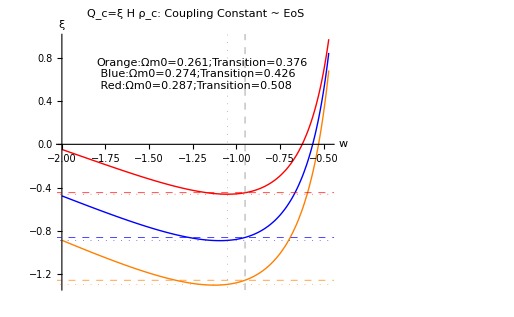

```mathematica
pltξvwExam1ICC
```

Now we assume we do not have the observed Ωm0 data, how do this Ωm0 change the result of ξ. In other words, if the observed Ωm0 data float around some value, then how is the fitting result? We also consider the curvature.
In the figure below, it seems that there is a point where three lines converge. This has something to do with the phenomena that

```mathematica
pltξvΩm0ICCManSum
```

Some data for flat ΛCDM universe. The following data shows how Ωm0 change our results for ξ if we already have transition redshift data {0.426|0.376,0.508}.

If Ωm0 varies 5 percent from 0.274,

```mathematica
tabξICCSum
```

For Ωm0∈0.274 (1±0.05) Table of ξ for different Ωm0~Transition combination |  |  | 
Ωm0Transition | 0.426 | 0.376 | 0.508
0.2603 | -0.994339 | -1.28571 | -0.641508
0.274 | -0.877755 | -1.15303 | -0.544482
0.2877 | -0.767582 | -1.02756 | -0.452892

Monotonic line.

```mathematica
pltξvΩm0ICCSum
```

-Graphics-

Besides Ωm0, we can also find out the effects of Curvature, EoS. Assuming we have a constrain of Transition redshift (0.376,0.508) with a center at 0.426.

```mathematica
fitξ2ICCManSum
```

```mathematica
pltξvΩm0ICCSum2
```

-Graphics-

```mathematica
tabξvΩm0ICCSum21
tabξvΩm0ICCSum22
```

Q_c=ξ H ρ_c, constant w: ξ when transition redshift is 0.426 |  | 
⋱ | w=-0.45064 | w=-0.45063
Ωm0=0.2603 | 0.999886 | -3.64749

Q_c=ξ H ρ_c, constant w:EoS value when ξ=0 | 
⋱ | Transition 0.426
Ωm0=0.2877 | -0.58406

So we give the result that w ∈ (-0.58406, -0.3334) if we constrain Ωm0 = 0.2603 and transition redshift 0.426.

### Interacting model Q_c=ξ H ρ_c with constant ξ and CPL parameterized EoS w=w0+w1 z/(1+z).

For a flat universe, choose the parameters {w0=-1.02,w1=0.6}, the region for interation cosntant ξ should be  (-1.04,-0.21) with a center at -0.64, i.e., -0.64_-0.40^(+0.42) ,derived from the (transition redshift, Ωm0) plane, while a result of (-1.01, -0.23) with a center at -0.63, i.e., -0.63_-0.38^(+0.40) , derived from (transition redshift, Ωm0/Ωd0) plane.

Deceleration parameter is shown below. Behaves similiar to the constant ξ constant w situation.

```mathematica
pldecICCPLShowSum
```

-Graphics-

The following plots shows the effect of different parameters. Each plot shows how do the deceleration parameter vs redshift line change under  uniformly distributed w0,w1,Ωm0 or ξ.
w0 moves the line up or down, but not monotonously;
w1 changes the late time behavior;
Ωm0 changes the slope;
ξ has moves the line up or down;

```mathematica
varyingICCPLShowSum
```

Q_c=ξ H ρ_c, CPL |  |  | 
Varying CPL w0 | Varying CPL w1 | Varying Ωm0 | Varying ξ
-Graphics- | -Graphics- | -Graphics- | -Graphics-

A toy to play with the q~z plot. When ξ=0, w0=-1, w1=0, the curve reduced to LCDM curve.

```mathematica
pldecICCPLManSum
```

A plot shows how bad it is to use transition redshift to constrain interacting model. This is a CPL parameterized example. For ξ∈(-0.8,0), the line just stays near the allowed region constrained by Riess’s results (References, Data From, 2).

```mathematica
pltransrICCPLDense
```

-Graphics-

From the manipulate below, we find for w0=-1, there is a point on this transition ~ Ωm0 curve do not change with coupling constant ξ and w1. (Well, what’s the use of that... )

```mathematica
plztrICCPLManSum
```

An explicit proof of this statement.

```mathematica
plztrExamICCPLSum
```

-Graphics-

A manipulate of the fitting results.

```mathematica
fitξICCPLManSum
```

FindRoot::nlnum: The function value {0.261\ 4.^3.  - 1.\ ξICCPL - 12.4244\ (0.122156  + 0.261\ 0.25^-1.26 + ξICCPL\ ξICCPL\ ExpIntegralE[2.26  + Times[« 2 »], 0.45] - 0.261\ ξICCPL\ ExpIntegralE[2.26  + Times[« 2 »], 1.8])}
 is not a list of numbers with dimensions {1} at {z} = {3.}.

ReplaceAll::reps: {FindRoot[(1 + 3\ Plus[« 2 »])\ ΩdICCPL[0.739, 0.261, -1.02, 0.6, ξICCPL, z] + ΩmICCPL[0.261, ξICCPL, z] == 0, {z, 3}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

FindRoot::nlnum: The function value {0.274\ 4.^3.  - 1.\ ξICCPL - 12.4244\ (0.120007  + 0.274\ 0.25^-1.26 + ξICCPL\ ξICCPL\ ExpIntegralE[2.26  + Times[« 2 »], 0.45] - 0.274\ ξICCPL\ ExpIntegralE[2.26  + Times[« 2 »], 1.8])}
 is not a list of numbers with dimensions {1} at {z} = {3.}.

ReplaceAll::reps: {FindRoot[(1 + 3\ Plus[« 2 »])\ ΩdICCPL[0.726, 0.274, -1.02, 0.6, ξICCPL, z] + ΩmICCPL[0.274, ξICCPL, z] == 0, {z, 3}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

FindRoot::nlnum: The function value {0.287\ 4.^3.  - 1.\ ξICCPL - 12.4244\ (0.117858  + 0.287\ 0.25^-1.26 + ξICCPL\ ξICCPL\ ExpIntegralE[2.26  + Times[« 2 »], 0.45] - 0.287\ ξICCPL\ ExpIntegralE[2.26  + Times[« 2 »], 1.8])}
 is not a list of numbers with dimensions {1} at {z} = {3.}.

General::stop: Further output of FindRoot :: nlnum will be suppressed during this calculation.

ReplaceAll::reps: {FindRoot[(1 + 3\ Plus[« 2 »])\ ΩdICCPL[0.713, 0.287, -1.02, 0.6, ξICCPL, z] + ΩmICCPL[0.287, ξICCPL, z] == 0, {z, 3}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

FindRoot::nlnum: The function value {0.261\ 4.^3.  - 1.\ ξICCPL - 12.4244\ (0.122156  + 0.261\ 0.25^-1.26 + ξICCPL\ ξICCPL\ ExpIntegralE[2.26  + Times[« 2 »], 0.45] - 0.261\ ξICCPL\ ExpIntegralE[2.26  + Times[« 2 »], 1.8])}
 is not a list of numbers with dimensions {1} at {z} = {3.}.

ReplaceAll::reps: {FindRoot[(1 + 3\ Plus[« 2 »])\ ΩdICCPL[0.739, 0.261, -1.02, 0.6, ξICCPL, z] + ΩmICCPL[0.261, ξICCPL, z] == 0, {z, 3}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

FindRoot::nlnum: The function value {0.274\ 4.^3.  - 1.\ ξICCPL - 12.4244\ (0.120007  + 0.274\ 0.25^-1.26 + ξICCPL\ ξICCPL\ ExpIntegralE[2.26  + Times[« 2 »], 0.45] - 0.274\ ξICCPL\ ExpIntegralE[2.26  + Times[« 2 »], 1.8])}
 is not a list of numbers with dimensions {1} at {z} = {3.}.

ReplaceAll::reps: {FindRoot[(1 + 3\ Plus[« 2 »])\ ΩdICCPL[0.726, 0.274, -1.02, 0.6, ξICCPL, z] + ΩmICCPL[0.274, ξICCPL, z] == 0, {z, 3}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

FindRoot::nlnum: The function value {0.287\ 4.^3.  - 1.\ ξICCPL - 12.4244\ (0.117858  + 0.287\ 0.25^-1.26 + ξICCPL\ ξICCPL\ ExpIntegralE[2.26  + Times[« 2 »], 0.45] - 0.287\ ξICCPL\ ExpIntegralE[2.26  + Times[« 2 »], 1.8])}
 is not a list of numbers with dimensions {1} at {z} = {3.}.

General::stop: Further output of FindRoot :: nlnum will be suppressed during this calculation.

ReplaceAll::reps: {FindRoot[(1 + 3\ Plus[« 2 »])\ ΩdICCPL[0.713, 0.287, -1.02, 0.6, ξICCPL, z] + ΩmICCPL[0.287, ξICCPL, z] == 0, {z, 3}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

FindRoot::nlnum: The function value {0.261\ 4.^3.  - 1.\ ξICCPL - 12.4244\ (0.122156  + 0.261\ 0.25^-1.26 + ξICCPL\ ξICCPL\ ExpIntegralE[2.26  + Times[« 2 »], 0.45] - 0.261\ ξICCPL\ ExpIntegralE[2.26  + Times[« 2 »], 1.8])}
 is not a list of numbers with dimensions {1} at {z} = {3.}.

ReplaceAll::reps: {FindRoot[(1 + 3\ Plus[« 2 »])\ ΩdICCPL[0.739, 0.261, -1.02, 0.6, ξICCPL, z] + ΩmICCPL[0.261, ξICCPL, z] == 0, {z, 3}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

FindRoot::nlnum: The function value {0.274\ 4.^3.  - 1.\ ξICCPL - 12.4244\ (0.120007  + 0.274\ 0.25^-1.26 + ξICCPL\ ξICCPL\ ExpIntegralE[2.26  + Times[« 2 »], 0.45] - 0.274\ ξICCPL\ ExpIntegralE[2.26  + Times[« 2 »], 1.8])}
 is not a list of numbers with dimensions {1} at {z} = {3.}.

ReplaceAll::reps: {FindRoot[(1 + 3\ Plus[« 2 »])\ ΩdICCPL[0.726, 0.274, -1.02, 0.6, ξICCPL, z] + ΩmICCPL[0.274, ξICCPL, z] == 0, {z, 3}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

FindRoot::nlnum: The function value {0.287\ 4.^3.  - 1.\ ξICCPL - 12.4244\ (0.117858  + 0.287\ 0.25^-1.26 + ξICCPL\ ξICCPL\ ExpIntegralE[2.26  + Times[« 2 »], 0.45] - 0.287\ ξICCPL\ ExpIntegralE[2.26  + Times[« 2 »], 1.8])}
 is not a list of numbers with dimensions {1} at {z} = {3.}.

General::stop: Further output of FindRoot :: nlnum will be suppressed during this calculation.

ReplaceAll::reps: {FindRoot[(1 + 3\ Plus[« 2 »])\ ΩdICCPL[0.713, 0.287, -1.02, 0.6, ξICCPL, z] + ΩmICCPL[0.287, ξICCPL, z] == 0, {z, 3}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

#### Category

For different w0 and w1 in its EoS equation,

```mathematica
plEoSPhaseICCPL
```

-Graphics-

#### Quintom

Color illustrations for the following two figures.
“Purple line:(-1,0.1)─ Blue line: (-1,0.2) Green line:(-1,-0.1)\n─ Pink line:LCDM”
“Purple Dashed:(-0.9,0.1)  Green Dashed:(-1.1,0.1)”

```mathematica
plEoSICCPLQuintomSum
```

-Graphics- | -Graphics-

Plots of Transition redshift vs Ωm0.
Legends are shown on the plots. Hard to distingush from each other.

```mathematica
plztrICCPLQuintomSum
```

-Graphics- | -Graphics-

For different EoS, the fitting results are different. The following table and plots show how do w0 and w1 change the results.

```mathematica
tabξvwExamICCPLQuintom
```

ξ results for Q_c=ξ H ρ_d, CPL,Quintom. |  |  | 
{w0,w1} | Center | Lower | Upper
{-1,-0.1} | -0.907284 | -1.3096 | -0.484861
{-1,0} | -0.877755 | -1.27874 | -0.457448
{-1,0.1} | -0.844859 | -1.24477 | -0.426298
{-0.9,0.1} | -0.785036 | -1.17144 | -0.383258
{-1.1,-0.1} | -0.910565 | -1.3218 | -0.477189

```mathematica
pltfitξICCPLQuintomSum
```

-Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics-
-Graphics-
-Graphics- | -Graphics-
-Graphics- |

#### Quintessence

```mathematica
plEoSICCPLQuintessenceSum
```

-Graphics-

Different from constant w results,

```mathematica
plztrICCPLQuintessenceSum
```

-Graphics- | -Graphics-

Some ξ fitting results are shown below. This shows how do w0 and w1 change ξ results.

```mathematica
tabξvwExamICCPLQuintessence
```

ξ results for Q_c=ξ H ρ_d, CPL,Quintessence. |  |  | 
{w0,w1} | Center | Lower | Upper
{-0.9,-0.05} | -0.853591 | -1.24197 | -0.448612
{-0.8,-0.05} | -0.765204 | -1.1341 | -0.384235
{-0.8,-0.1} | -0.794865 | -1.16484 | -0.412217

```mathematica
pltfitξICCPLQuintessenceSum
```

-Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics-

#### Phantom

```mathematica
plEoSICCPLPhantomSum
```

-Graphics-

```mathematica
plztrICCPLPhantomSum
```

-Graphics-

```mathematica
tabξvwExamICCPLPhantom
```

ξ results for Q_c=ξ H ρ_d, CPL,Phantom. |  |  | 
{w0,w1} | Center | Lower | Upper
{-1.1,0.05} | -0.878139 | -1.28773 | -0.447379
{-1.2,0.05} | -0.870255 | -1.28596 | -0.431951
{-1.2,0.1} | -0.861665 | -1.27697 | -0.424022

```mathematica
pltfitξICCPLPhantomSum
```

-Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics-

### Interacting model Q_c=ξ H ρ_d with constant ξ and constant EoS w.

Derived from (transition redshift, Ωm0) plane, the allowed region for coupling constant ξ is ( -1.06,-0.42) with a center at -0.76, i.e., -0.76_-0.30^(+0.34) ,  taken the case that the universe is flat, and choose the EoS parameter {w=-1}.
Derived from the (transition redshift, Ωm0/Ωd0) plane, the allowed region of coupling constant ξ is (-1.07,-0.41) with a center at -0.76, i.e., -0.76_-0.31^(+0.35).

The plots of deceleration parameter are shown below. At the limit z->Infinity, the deceleration parameter ALL goes to 1/2.
Theoretically, this limit is  1/2 which is not related to any parameters, with 3w+ξ<0.

```mathematica
pldecI2CCShowSum
```

-Graphics-

To check the effect of different parameters, another plot is shown.

```mathematica
varyingI2CCShowSum
```

Varying EoS | Varying Ωm0 | Varying ξ
-Graphics- | -Graphics- | -Graphics-

A toy to play with deceleration vs z curve is also provied

```mathematica
pldecI2CCManSum
```

If the transition happens before z=0, increasing couling ξ will delay the transition.
If the it happens after z=0, increasing coupling ξ will bring forward the emergence of transition.

The following figure shows this result.

Gray rectangle is the region given by Riess.

Orange for w=-1
Blue for w=-0.9

line: ξ=0.2
Dashed: ξ=0.1
Dotted: ξ=-0.1
DotDashed: ξ=-0.2

Pink line:w=1, ξ=0

```mathematica
plztrvsΩm0I2CCSum
```

-Graphics- | -Graphics-

A toy of transition redshift. Gray rectangle is the allowed region of Ωm0~Transition redshift

```mathematica
plztrI2CCManSum
```

The fitting results of coupling constant ξ is

```mathematica
fitξI2CCManSum
```

For different constant EoS, the fitting results using Ωm0∈(0.261,0.287) with a center value 0.274 and Transition redshift ∈ (0.376,0.508) with a center value 0.426. When EoS is very small, the line might cross zero. But that is not so useful.

Some data: ( -1 within 5%: (-1.05,-0.95))
w=-1  (-1.074,-0.409) center:-0.761
w=-1.05  (-1.126,-0.428) center:-0.798
w=-0.95  (-1.013,-0.385) center:-0.717

The following graph show how do ξ changes with EoS. The grid lines are the results of w=-1±0.05. Two verticle lines are -1.05 and -0.95 respectively. Horizontal lines are their intersections with the ξ~w lines.

```mathematica
pltξvwExam1I2CC
```

-Graphics-

Or we can use some fitting results from WMAP etc. Take the example of w=-1.087±0.096.

```mathematica
tabξvwExamI2CC
```

Q_c=ξ H ρ_d,Constant w. (Data used:Data From, 2) |  |  | 
w | Center | Lower | Upper
-1.183 | -0.864289 | -1.22984 | -0.449552
-1.087 | -0.820486 | -1.15946 | -0.437339
-0.991 | -0.753634 | -1.06346 | -0.405262

```mathematica
pltξvwExamI2CC
```

-Graphics-

Now we assume we do not have the observed Ωm0 data, how do this Ωm0 change the result. In other words, if the observed Ωm0 data float around some value, then how is the fitting result? We also consider the curvature.

```mathematica
pltξvΩm0I2CCManSum
```

If Ωm0 varies 0.05 percent from 0.274,

```mathematica
tabξI2CCSum
```

For Ωm0∈0.274 (1±0.05) Table of ξ for different Ωm0~Transition combination |  |  | 
Ωm0Transition | 0.426 | 0.376 | 0.508
0.2603 | -0.832284 | -1.07758 | -0.53584
0.274 | -0.760999 | -1.00068 | -0.471298
0.2877 | -0.688664 | -0.922602 | -0.40585

```mathematica
pltξvΩm0I2CCSum
```

-Graphics-

In addition, we can also find out the effects of Curvature, EoS. Assuming we have a constrain of Transition redshift (0.376,0.508) with a center at 0.426.

```mathematica
fitξ2I2CCManSum
```

### Interacting model Q_c=ξ H ρ_d with constant ξ and CPL parameterization.

```mathematica
pldecI2CCPLShowSum
```

-Graphics-

```mathematica
varyingI2CCPLShowSum
```

Q_c=ξ H ρ_d, CPL |  |  | 
Varying CPL w0 | Varying CPL w1 | Varying Ωm0 | Varying ξ
-Graphics- | -Graphics- | -Graphics- | -Graphics-

```mathematica
plztrExamI2CCPLSum
```

-Graphics- | -Graphics-

#### Quintom

```mathematica
plEoSI2CCPLQuintomSum
```

-Graphics- | -Graphics-

```mathematica
plztrI2CCPLQuintomSum
```

-Graphics- | -Graphics-

```mathematica
tabξvwExamI2CCPLQuintom
```

ξ results for Q_c=ξ H ρ_d, CPL,Quintom. |  |  | 
{w0,w1} | Center | Lower | Upper
{-1,-0.1} | -1.21004 | -1.73137 | -0.653393
{-1,0} | -1.15265 | -1.66715 | -0.605615
{-1,0.1} | -1.09155 | -1.59939 | -0.553918
{-0.9,0.1} | -0.94736 | -1.40905 | -0.463859
{-1.1,-0.1} | -1.28331 | -1.84354 | -0.680925

```mathematica
pltfitξI2CCPLQuintomSum
```

-Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics-
-Graphics-
-Graphics- | -Graphics-
-Graphics- |

#### Quintessence

```mathematica
plEoSI2CCPLQuintessenceSum
```

-Graphics-

```mathematica
plztrI2CCPLQuintessenceSum
```

-Graphics- | -Graphics-

```mathematica
tabξvwExamI2CCPLQuintessence
```

ξ results for Q_c=ξ H ρ_d, CPL,Quintessence. |  |  | 
{w0,w1} | Center | Lower | Upper
{-0.9,-0.05} | -1.05994 | -1.53267 | -0.561052
{-0.8,-0.05} | -0.881934 | -1.30148 | -0.445082
{-0.8,-0.1} | -0.926183 | -1.35 | -0.483467

```mathematica
pltfitξI2CCPLQuintessenceSum
```

-Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics-

#### Phantom

```mathematica
plEoSI2CCPLPhantomSum
```

-Graphics-

```mathematica
plztrI2CCPLPhantomSum
```

-Graphics-

```mathematica
tabξvwExamI2CCPLPhantom
```

ξ results for Q_c=ξ H ρ_d, CPL,Phantom. |  |  | 
{w0,w1} | Center | Lower | Upper
{-1.1,0.05} | -1.21257 | -1.76337 | -0.623591
{-1.2,0.05} | -1.266 | -1.8517 | -0.635863
{-1.2,0.1} | -1.24569 | -1.82849 | -0.619702

```mathematica
pltfitξI2CCPLPhantomSum
```

-Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics-

### References

#### Data From

CPL data

Combining SN1a, BAO 3, WMAP5, H(z)   (From arXiv:0909.0596)

Ωm0=0.269_-0.008^(+0.017), w0=-0.97_-0.07^(+0.12), w1=0.03_-0.75^(+0.26).

LCDM

From WMAP: Ωm0=0.265
arXiv:astro-ph/0611572, Riess et al     : 
arXiv:1205.4688 : Ωm0=0.247 (+0.013, -0.013)  and Transition 0.426 (+0.082, -0.050)

Equation of state

From arXiv:1202.0545v1
w = -1.087±0.096.

## Supplementary

#### Interacting model Q_c=ξ H ρ_c with constant ξ and constant EoS w.

```mathematica
pltξvΩm0ICCSum2
```

-Graphics-

```mathematica
tabξvΩm0ICCSum21
tabξvΩm0ICCSum22
```

Q_c=ξ H ρ_c, constant w: ξ when transition redshift is 0.426 |  | 
⋱ | w=-0.45064 | w=-0.45063
Ωm0=0.2603 | 0.999886 | -3.64749

Q_c=ξ H ρ_c, constant w:EoS value when ξ=0 | 
⋱ | Transition 0.426
Ωm0=0.2877 | -0.58406

So we give the result that w∈(-0.58406, -0.45064) if we constrain Ωm0=0.2603 and transition redshift 0.426.

#### Interacting model Q_c=ξ H ρ_c with constant ξ and CPL parameterized EoS w=w0+w1 z/(1+z).

```mathematica
pltξvΩm0ICCPLQuintomSum
```

-Graphics- | -Graphics-

```mathematica
pltξvΩm0ICCPLQuintessenceSum
```

-Graphics- | -Graphics-

```mathematica
pltξvΩm0ICCPLPhantomSum
```

-Graphics-

```mathematica
pltw0vw1ConsICCPL
```

-Graphics-

#### Interacting model Q_c=ξ H ρ_d with constant ξ and constant EoS w.

```mathematica
pltξvΩm0I2CCSum2
```

-Graphics-

```mathematica
tabξvΩm0I2CCSum21
tabξvΩm0I2CCSum22
```

Q_c=ξ H ρ_d, constant w: ξ when transition redshift is 0.426 |  | 
⋱ | w=-0.4506 | w=-0.4507
Ωm0=0.2603 | -17.5369 | 0.351603

Q_c=ξ H ρ_d, constant w: EoS value when ξ=0 | 
⋱ | Transition 0.426
Ωm0=0.2877 | -0.58406

So we give the result that w ∈ (-0.58406, -0.4507) if we constrain Ωm0 = 0.2603 and transition redshift 0.426.

#### Interacting model Q_c=ξ H ρ_d with constant ξ and CPL parameterization.

```mathematica
pltξvΩm0I2CCPLQuintomSum
```

-Graphics- | -Graphics-

```mathematica
pltξvΩm0I2CCPLQuintessenceSum
```

-Graphics- | -Graphics-

```mathematica
pltξvΩm0I2CCPLPhantomSum
```

-Graphics-

```mathematica
pltw0vw1ConsI2CCPL
```

-Graphics-